# Deference Done Better: Functions Notebook

## Questions? Problems? Suggestions? Email kevindorst0@gmail.com.

## Frame Examples (run before working):

```mathematica
(*3 of these 100 prior frames are p-reflexive. I think (not sure) that none validate Trust *)
priorFrames = {{{1/3,1/9,4/9,1/9},{3/7,0,4/7,0},{0,0,0,1},{3/8,0,1/2,1/8}},{{1/6,1/3,1/2,0},{0,2/5,3/5,0},{0,0,3/4,1/4},{1/4,0,3/4,0}},{{1/4,0,3/4,0},{0,0,0,1},{0,0,0,1},{0,2/7,3/7,2/7}},{{2/5,0,2/5,1/5},{1/3,2/3,0,0},{2/7,4/7,0,1/7},{0,2/3,1/3,0}},{{0,4/11,3/11,4/11},{0,0,1,0},{0,1/2,0,1/2},{1,0,0,0}},{{1/7,4/7,0,2/7},{1/7,0,4/7,2/7},{1/5,4/5,0,0},{1/7,0,4/7,2/7}},{{1/7,2/7,2/7,2/7},{0,0,0,1},{1/7,2/7,2/7,2/7},{1/5,2/5,0,2/5}},{{0,2/5,1/5,2/5},{0,1/2,0,1/2},{0,0,0,1},{3/8,1/4,1/8,1/4}},{{4/13,4/13,4/13,1/13},{4/13,4/13,4/13,1/13},{0,4/9,4/9,1/9},{0,4/9,4/9,1/9}},{{1/6,1/4,1/3,1/4},{0,3/10,2/5,3/10},{0,0,1,0},{2/5,3/5,0,0}},{{1/2,0,1/2,0},{0,0,3/7,4/7},{3/10,0,3/10,2/5},{1/4,1/6,1/4,1/3}},{{0,3/5,2/5,0},{2/11,3/11,2/11,4/11},{0,0,1/3,2/3},{0,0,0,1}},{{4/13,3/13,4/13,2/13},{4/13,3/13,4/13,2/13},{0,3/7,4/7,0},{4/11,3/11,4/11,0}},{{1,0,0,0},{1/2,0,1/2,0},{0,1/2,0,1/2},{0,1,0,0}},{{0,0,1,0},{0,0,1,0},{0,4/7,0,3/7},{1,0,0,0}},{{0,1/3,1/3,1/3},{3/5,0,0,2/5},{1/3,2/9,2/9,2/9},{0,0,0,1}},{{2/5,1/5,0,2/5},{1/2,0,0,1/2},{1/2,0,1/2,0},{2/7,1/7,2/7,2/7}},{{0,0,0,1},{1/3,0,0,2/3},{1/4,3/4,0,0},{0,3/5,0,2/5}},{{0,2/3,1/3,0},{0,0,0,1},{1/7,2/7,1/7,3/7},{1/6,1/3,0,1/2}},{{1,0,0,0},{0,1/5,2/5,2/5},{1,0,0,0},{4/9,1/9,2/9,2/9}},{{0,1/6,2/3,1/6},{2/3,1/6,0,1/6},{2/3,1/6,0,1/6},{2/5,1/10,2/5,1/10}},{{1/5,0,4/5,0},{1,0,0,0},{1,0,0,0},{0,1/5,4/5,0}},{{0,1,0,0},{3/8,1/8,1/8,3/8},{0,1,0,0},{0,0,1/4,3/4}},{{0,1/4,1/2,1/4},{1/2,0,0,1/2},{1/2,0,0,1/2},{1/2,0,0,1/2}},{{2/3,0,1/3,0},{4/11,3/11,2/11,2/11},{4/9,1/3,2/9,0},{4/11,3/11,2/11,2/11}},{{1/3,1/3,2/9,1/9},{3/8,3/8,1/4,0},{1/3,1/3,2/9,1/9},{1/2,0,1/3,1/6}},{{0,3/4,1/4,0},{0,0,1/5,4/5},{1/9,1/3,1/9,4/9},{1/5,0,0,4/5}},{{0,0,1,0},{2/5,3/5,0,0},{2/9,1/3,0,4/9},{1,0,0,0}},{{2/5,1/5,1/5,1/5},{2/3,0,1/3,0},{1/2,1/4,0,1/4},{0,1/3,1/3,1/3}},{{2/11,4/11,1/11,4/11},{2/11,4/11,1/11,4/11},{2/11,4/11,1/11,4/11},{2/11,4/11,1/11,4/11}},{{3/7,1/7,1/7,2/7},{0,1/2,1/2,0},{0,0,0,1},{0,1,0,0}},{{3/13,3/13,3/13,4/13},{1,0,0,0},{3/13,3/13,3/13,4/13},{1/3,1/3,1/3,0}},{{1/4,1/3,1/12,1/3},{0,0,0,1},{0,0,1,0},{3/7,4/7,0,0}},{{3/13,3/13,3/13,4/13},{3/13,3/13,3/13,4/13},{3/13,3/13,3/13,4/13},{3/13,3/13,3/13,4/13}},{{0,1/2,0,1/2},{1,0,0,0},{1,0,0,0},{4/5,1/5,0,0}},{{0,0,0,1},{1/2,1/2,0,0},{2/5,2/5,1/5,0},{0,0,0,1}},{{0,0,1,0},{1/3,0,1/3,1/3},{0,1/3,1/3,1/3},{1/3,1/3,0,1/3}},{{3/7,0,0,4/7},{3/10,1/5,1/10,2/5},{1,0,0,0},{3/10,1/5,1/10,2/5}},{{2/5,3/5,0,0},{0,3/8,1/4,3/8},{1/2,0,1/2,0},{0,1/2,0,1/2}},{{0,1/3,2/3,0},{3/4,0,0,1/4},{3/5,2/5,0,0},{3/10,1/5,2/5,1/10}},{{0,0,1,0},{3/11,0,4/11,4/11},{0,0,1/2,1/2},{0,0,0,1}},{{1/3,0,1/3,1/3},{1/4,1/4,1/4,1/4},{0,0,0,1},{1/4,1/4,1/4,1/4}},{{2/5,1/5,1/10,3/10},{2/5,1/5,1/10,3/10},{0,1/3,1/6,1/2},{0,1,0,0}},{{0,0,0,1},{1/3,1/9,4/9,1/9},{1/3,1/9,4/9,1/9},{1/3,1/9,4/9,1/9}},{{0,1/3,2/3,0},{1/5,1/5,2/5,1/5},{1/5,1/5,2/5,1/5},{1,0,0,0}},{{3/4,0,0,1/4},{3/10,2/5,1/5,1/10},{3/5,0,2/5,0},{3/4,0,0,1/4}},{{1/4,0,3/8,3/8},{0,1/4,0,3/4},{2/9,1/9,1/3,1/3},{1/3,1/6,1/2,0}},{{0,3/10,2/5,3/10},{0,0,0,1},{0,1/2,0,1/2},{0,3/7,4/7,0}},{{3/10,2/5,0,3/10},{1/2,0,1/2,0},{3/7,4/7,0,0},{0,0,1/2,1/2}},{{0,1,0,0},{2/9,2/9,4/9,1/9},{0,0,0,1},{0,0,0,1}},{{2/3,0,0,1/3},{1,0,0,0},{1/2,0,1/2,0},{2/7,2/7,2/7,1/7}},{{2/7,2/7,3/14,3/14},{0,0,1,0},{4/7,0,3/7,0},{1/2,1/2,0,0}},{{0,0,0,1},{1/2,1/3,0,1/6},{3/5,2/5,0,0},{0,0,1,0}},{{1/9,1/3,4/9,1/9},{1/4,3/4,0,0},{0,1,0,0},{0,1,0,0}},{{0,1/2,0,1/2},{3/4,1/4,0,0},{1,0,0,0},{3/7,1/7,2/7,1/7}},{{2/3,0,1/6,1/6},{2/3,0,1/6,1/6},{0,1,0,0},{0,1/2,0,1/2}},{{4/11,3/11,4/11,0},{2/7,3/14,2/7,3/14},{2/7,3/14,2/7,3/14},{4/11,0,4/11,3/11}},{{2/7,1/7,2/7,2/7},{0,1/5,2/5,2/5},{0,1/3,2/3,0},{2/5,1/5,0,2/5}},{{1/7,1/7,2/7,3/7},{1/6,0,1/3,1/2},{0,0,2/5,3/5},{1/7,1/7,2/7,3/7}},{{1/5,0,2/5,2/5},{1/6,1/6,1/3,1/3},{1,0,0,0},{1/6,1/6,1/3,1/3}},{{4/7,0,0,3/7},{0,0,2/5,3/5},{1/3,1/4,1/6,1/4},{1/3,1/4,1/6,1/4}},{{0,0,3/4,1/4},{3/8,1/8,3/8,1/8},{3/8,1/8,3/8,1/8},{0,1/2,0,1/2}},{{2/5,0,3/5,0},{0,1/4,3/8,3/8},{0,0,1,0},{0,0,1,0}},{{3/11,3/11,4/11,1/11},{3/7,3/7,0,1/7},{3/11,3/11,4/11,1/11},{0,1,0,0}},{{0,0,0,1},{1/4,0,1/4,1/2},{0,1/7,2/7,4/7},{0,0,0,1}},{{1/4,3/4,0,0},{1/9,1/3,2/9,1/3},{1/6,1/2,1/3,0},{0,0,0,1}},{{0,1,0,0},{0,0,1,0},{2/7,0,2/7,3/7},{0,3/5,2/5,0}},{{0,0,0,1},{1/6,1/3,1/6,1/3},{1/6,1/3,1/6,1/3},{1/4,0,1/4,1/2}},{{0,0,1,0},{1/5,0,4/5,0},{1/7,1/7,4/7,1/7},{1,0,0,0}},{{1/5,1/5,2/5,1/5},{0,0,0,1},{0,1/2,0,1/2},{0,0,0,1}},{{2/7,3/7,1/7,1/7},{1/3,1/2,1/6,0},{0,3/4,0,1/4},{0,3/4,0,1/4}},{{0,0,2/5,3/5},{1/3,1/4,1/6,1/4},{0,0,2/5,3/5},{4/9,0,2/9,1/3}},{{2/7,0,2/7,3/7},{2/7,3/7,2/7,0},{0,3/8,1/4,3/8},{0,0,1,0}},{{2/5,1/5,1/10,3/10},{0,2/3,1/3,0},{0,1,0,0},{4/5,0,1/5,0}},{{1/6,1/2,1/6,1/6},{0,1,0,0},{1,0,0,0},{1/6,1/2,1/6,1/6}},{{1/4,1/3,1/6,1/4},{0,0,1,0},{3/10,2/5,0,3/10},{0,4/9,2/9,1/3}},{{1/3,0,1/3,1/3},{1/5,2/5,1/5,1/5},{0,0,1/2,1/2},{1/4,1/2,0,1/4}},{{3/7,3/7,1/7,0},{3/4,0,0,1/4},{3/8,3/8,1/8,1/8},{0,1,0,0}},{{3/8,1/4,1/4,1/8},{0,0,1,0},{3/5,0,2/5,0},{3/7,2/7,2/7,0}},{{3/11,4/11,2/11,2/11},{3/5,0,0,2/5},{3/11,4/11,2/11,2/11},{1,0,0,0}},{{1/3,1/9,2/9,1/3},{0,1/6,1/3,1/2},{0,0,1,0},{1/3,1/9,2/9,1/3}},{{0,1,0,0},{1/8,3/8,1/4,1/4},{1/8,3/8,1/4,1/4},{1/8,3/8,1/4,1/4}},{{1/4,3/8,0,3/8},{2/11,3/11,3/11,3/11},{2/5,3/5,0,0},{1/4,3/8,3/8,0}},{{0,1/5,4/5,0},{1/5,1/10,2/5,3/10},{1/5,1/10,2/5,3/10},{0,0,0,1}},{{3/8,3/8,1/4,0},{3/8,3/8,1/4,0},{1,0,0,0},{3/11,3/11,2/11,3/11}},{{3/11,4/11,3/11,1/11},{0,4/7,3/7,0},{0,4/7,3/7,0},{0,0,1,0}},{{1/4,1/4,0,1/2},{0,1/3,2/3,0},{0,1,0,0},{1/6,1/6,1/3,1/3}},{{2/3,1/6,0,1/6},{2/3,1/6,1/6,0},{0,1/2,0,1/2},{4/7,1/7,1/7,1/7}},{{0,0,0,1},{0,0,2/3,1/3},{4/7,1/7,2/7,0},{0,1/3,2/3,0}},{{1/4,3/8,3/8,0},{0,1/2,1/2,0},{2/3,0,0,1/3},{2/9,1/3,1/3,1/9}},{{0,1,0,0},{2/7,3/7,1/7,1/7},{1/3,1/2,0,1/6},{1/2,0,1/4,1/4}},{{1/4,1/2,0,1/4},{1/5,2/5,1/5,1/5},{1/3,0,1/3,1/3},{1/5,2/5,1/5,1/5}},{{0,0,1,0},{0,1/7,2/7,4/7},{0,1,0,0},{2/5,0,1/5,2/5}},{{1/2,0,1/4,1/4},{0,1,0,0},{2/7,4/7,1/7,0},{1/4,1/2,1/8,1/8}},{{4/9,0,1/3,2/9},{1,0,0,0},{2/3,0,0,1/3},{0,1,0,0}},{{0,0,1,0},{1/3,0,1/3,1/3},{1/3,1/3,1/3,0},{0,0,1/2,1/2}},{{0,0,0,1},{0,0,2/3,1/3},{1/2,1/8,1/4,1/8},{1,0,0,0}},{{1/5,4/5,0,0},{0,4/7,3/7,0},{0,4/7,3/7,0},{0,0,0,1}},{{1,0,0,0},{2/9,1/9,4/9,2/9},{1/2,0,0,1/2},{1/2,0,0,1/2}},{{3/4,1/4,0,0},{1/2,1/6,1/6,1/6},{1/2,1/6,1/6,1/6},{3/5,1/5,0,1/5}}};
```

```mathematica
(*prior frames that validate Trust (and, therefore Value)*)
priorTrees={{{1,0,0,0},{1/3,1/3,1/6,1/6},{1/2,0,1/4,1/4},{0,0,0,1}},{{1/11,4/11,3/11,3/11},{1/11,4/11,3/11,3/11},{1/11,4/11,3/11,3/11},{1/11,4/11,3/11,3/11}},{{4/13,3/13,2/13,4/13},{4/13,3/13,2/13,4/13},{4/13,3/13,2/13,4/13},{4/13,3/13,2/13,4/13}},{{3/11,3/11,4/11,1/11},{3/11,3/11,4/11,1/11},{3/11,3/11,4/11,1/11},{0,0,0,1}},{{1/3,1/4,1/6,1/4},{1/3,1/4,1/6,1/4},{0,0,1,0},{1/3,1/4,1/6,1/4}},{{0,1/3,0,2/3},{0,1,0,0},{0,1/4,1/4,1/2},{0,1/3,0,2/3}},{{0,1,0,0},{0,1,0,0},{0,0,0,1},{0,0,0,1}},{{1/8,3/8,3/8,1/8},{1/8,3/8,3/8,1/8},{1/8,3/8,3/8,1/8},{1/8,3/8,3/8,1/8}},{{0,0,3/5,2/5},{0,0,0,1},{0,0,3/5,2/5},{0,0,0,1}},{{1/8,3/8,3/8,1/8},{1/8,3/8,3/8,1/8},{1/8,3/8,3/8,1/8},{1/8,3/8,3/8,1/8}},{{1/4,1/4,1/4,1/4},{1/4,1/4,1/4,1/4},{1/4,1/4,1/4,1/4},{1/4,1/4,1/4,1/4}},{{1/3,1/3,2/9,1/9},{1/3,1/3,2/9,1/9},{1/3,1/3,2/9,1/9},{1/3,1/3,2/9,1/9}},{{1/3,2/3,0,0},{1/3,2/3,0,0},{2/11,4/11,4/11,1/11},{2/11,4/11,4/11,1/11}},{{4/7,1/7,0,2/7},{0,1,0,0},{0,1/3,0,2/3},{0,0,0,1}},{{1/5,3/5,0,1/5},{0,1,0,0},{1/6,1/2,1/6,1/6},{0,0,0,1}},{{1/2,0,1/2,0},{0,1/2,1/3,1/6},{0,0,1,0},{0,0,0,1}},{{3/7,0,4/7,0},{1/4,1/4,1/3,1/6},{0,0,1,0},{0,0,0,1}},{{1/3,1/9,1/3,2/9},{1/3,1/9,1/3,2/9},{0,0,1,0},{1/3,1/9,1/3,2/9}},{{1/10,3/10,2/5,1/5},{1/10,3/10,2/5,1/5},{1/10,3/10,2/5,1/5},{1/10,3/10,2/5,1/5}},{{1,0,0,0},{2/7,1/7,3/7,1/7},{2/7,1/7,3/7,1/7},{2/3,0,0,1/3}},{{1,0,0,0},{2/13,4/13,3/13,4/13},{2/13,4/13,3/13,4/13},{2/13,4/13,3/13,4/13}},{{1,0,0,0},{0,2/3,1/3,0},{0,0,1,0},{2/5,0,2/5,1/5}},{{1/3,1/4,1/6,1/4},{1/3,1/4,1/6,1/4},{1/3,1/4,1/6,1/4},{1/3,1/4,1/6,1/4}},{{0,3/5,1/5,1/5},{0,3/5,1/5,1/5},{0,0,1,0},{0,3/5,1/5,1/5}},{{1,0,0,0},{1/2,1/4,1/8,1/8},{2/3,0,1/6,1/6},{2/3,0,1/6,1/6}},{{1,0,0,0},{2/5,1/5,2/5,0},{1/2,0,1/2,0},{4/11,2/11,4/11,1/11}},{{1/2,0,1/4,1/4},{0,0,1,0},{0,0,1,0},{1/2,0,1/4,1/4}},{{1/2,0,0,1/2},{3/11,4/11,1/11,3/11},{0,0,1,0},{0,0,0,1}},{{2/11,3/11,2/11,4/11},{2/11,3/11,2/11,4/11},{2/11,3/11,2/11,4/11},{2/11,3/11,2/11,4/11}},{{1/9,1/9,1/3,4/9},{1/9,1/9,1/3,4/9},{1/9,1/9,1/3,4/9},{1/9,1/9,1/3,4/9}},{{1/9,1/3,4/9,1/9},{0,1,0,0},{1/9,1/3,4/9,1/9},{1/9,1/3,4/9,1/9}},{{1/4,1/12,1/3,1/3},{0,1,0,0},{1/4,1/12,1/3,1/3},{0,1/5,0,4/5}},{{1/2,1/2,0,0},{1/2,1/2,0,0},{1/2,1/2,0,0},{1/2,1/2,0,0}},{{4/11,1/11,3/11,3/11},{4/11,1/11,3/11,3/11},{4/11,1/11,3/11,3/11},{4/11,1/11,3/11,3/11}},{{1,0,0,0},{1,0,0,0},{3/5,0,2/5,0},{1/2,0,1/3,1/6}},{{4/11,3/11,2/11,2/11},{0,3/5,2/5,0},{0,0,1,0},{4/11,3/11,2/11,2/11}},{{1/3,1/3,0,1/3},{0,1,0,0},{1/3,1/3,0,1/3},{1/3,1/3,0,1/3}},{{4/11,4/11,1/11,2/11},{4/11,4/11,1/11,2/11},{4/11,4/11,1/11,2/11},{4/11,4/11,1/11,2/11}},{{3/11,4/11,3/11,1/11},{3/11,4/11,3/11,1/11},{3/11,4/11,3/11,1/11},{3/11,4/11,3/11,1/11}},{{4/7,0,0,3/7},{2/5,1/10,1/5,3/10},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{4/7,3/7,0,0},{4/11,3/11,4/11,0},{4/7,3/7,0,0}},{{3/8,1/8,1/8,3/8},{3/8,1/8,1/8,3/8},{0,0,1,0},{3/8,1/8,1/8,3/8}},{{1/13,4/13,4/13,4/13},{1/13,4/13,4/13,4/13},{1/13,4/13,4/13,4/13},{0,0,0,1}},{{1/5,2/5,1/5,1/5},{0,2/3,1/3,0},{0,0,1,0},{0,1/2,1/4,1/4}},{{1/3,1/3,1/4,1/12},{1/3,1/3,1/4,1/12},{1/3,1/3,1/4,1/12},{1/3,1/3,1/4,1/12}},{{3/8,3/8,1/4,0},{0,1,0,0},{0,0,1,0},{1/3,1/3,2/9,1/9}},{{2/7,2/7,2/7,1/7},{2/7,2/7,2/7,1/7},{0,0,1,0},{2/7,2/7,2/7,1/7}},{{1/4,1/3,1/12,1/3},{1/4,1/3,1/12,1/3},{1/4,1/3,1/12,1/3},{0,0,0,1}},{{4/7,3/7,0,0},{0,1,0,0},{4/13,3/13,4/13,2/13},{4/9,1/3,0,2/9}},{{3/7,0,3/7,1/7},{1/3,2/9,1/3,1/9},{0,0,1,0},{3/7,0,3/7,1/7}},{{1/11,4/11,4/11,2/11},{0,2/5,2/5,1/5},{0,0,1,0},{0,2/5,2/5,1/5}},{{3/11,0,4/11,4/11},{0,0,0,1},{3/11,0,4/11,4/11},{0,0,0,1}},{{4/7,0,1/7,2/7},{0,1,0,0},{0,0,1,0},{0,0,1/3,2/3}},{{1/2,0,1/2,0},{1/2,0,1/2,0},{0,0,1,0},{1/2,0,1/2,0}},{{1,0,0,0},{1,0,0,0},{0,0,1,0},{1,0,0,0}},{{2/3,0,1/3,0},{0,3/5,2/5,0},{0,0,1,0},{0,0,0,1}},{{2/3,0,1/3,0},{2/7,4/7,1/7,0},{0,0,1,0},{0,0,1,0}},{{1/6,1/4,1/4,1/3},{1/6,1/4,1/4,1/3},{1/6,1/4,1/4,1/3},{1/6,1/4,1/4,1/3}},{{1/5,0,4/5,0},{0,1,0,0},{0,0,1,0},{0,1/7,4/7,2/7}},{{1,0,0,0},{3/13,4/13,3/13,3/13},{1/2,0,1/2,0},{3/13,4/13,3/13,3/13}},{{1,0,0,0},{1/11,4/11,3/11,3/11},{0,0,1,0},{1/7,0,3/7,3/7}},{{1,0,0,0},{2/3,1/3,0,0},{1/3,1/6,1/2,0},{1,0,0,0}},{{0,0,0,1},{0,0,0,1},{0,0,1,0},{0,0,0,1}},{{2/9,2/9,4/9,1/9},{0,1,0,0},{2/9,2/9,4/9,1/9},{0,2/3,0,1/3}},{{1/7,1/7,2/7,3/7},{1/7,1/7,2/7,3/7},{1/7,1/7,2/7,3/7},{1/7,1/7,2/7,3/7}},{{1,0,0,0},{0,4/7,3/7,0},{0,4/7,3/7,0},{1/3,1/3,1/4,1/12}},{{1,0,0,0},{1/5,2/5,1/5,1/5},{1/5,2/5,1/5,1/5},{1/5,2/5,1/5,1/5}},{{1/4,1/4,1/8,3/8},{0,1,0,0},{0,0,1,0},{0,1/3,1/6,1/2}},{{1/5,0,4/5,0},{1/11,4/11,4/11,2/11},{0,0,1,0},{1/11,4/11,4/11,2/11}},{{4/11,3/11,3/11,1/11},{4/11,3/11,3/11,1/11},{4/11,3/11,3/11,1/11},{0,0,0,1}},{{1,0,0,0},{2/5,1/5,0,2/5},{2/5,0,1/5,2/5},{1/2,0,0,1/2}},{{2/3,0,0,1/3},{0,1/6,1/2,1/3},{0,0,3/5,2/5},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{1/2,1/3,0,1/6},{0,0,0,1}},{{3/8,0,3/8,1/4},{0,0,1,0},{0,0,1,0},{3/8,0,3/8,1/4}},{{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,4/5,1/5}},{{1/9,1/9,1/3,4/9},{1/9,1/9,1/3,4/9},{1/9,1/9,1/3,4/9},{1/9,1/9,1/3,4/9}},{{1,0,0,0},{3/10,3/10,1/5,1/5},{0,0,1,0},{3/10,3/10,1/5,1/5}},{{2/7,2/7,0,3/7},{0,1,0,0},{1/5,1/5,3/10,3/10},{0,0,0,1}},{{3/7,0,2/7,2/7},{3/7,0,2/7,2/7},{3/7,0,2/7,2/7},{3/7,0,2/7,2/7}},{{1/11,2/11,4/11,4/11},{1/11,2/11,4/11,4/11},{1/11,2/11,4/11,4/11},{1/11,2/11,4/11,4/11}},{{1,0,0,0},{0,4/5,1/5,0},{0,0,1,0},{0,0,1,0}},{{1/10,3/10,2/5,1/5},{0,1,0,0},{1/10,3/10,2/5,1/5},{0,3/5,0,2/5}},{{1/7,3/7,0,3/7},{0,1,0,0},{1/11,3/11,4/11,3/11},{0,1/2,0,1/2}},{{1/4,1/8,3/8,1/4},{0,1,0,0},{1/4,1/8,3/8,1/4},{1/4,1/8,3/8,1/4}},{{2/5,3/10,1/10,1/5},{0,3/4,1/4,0},{0,0,1,0},{0,0,0,1}},{{1/2,1/6,1/3,0},{1/2,1/6,1/3,0},{1/2,1/6,1/3,0},{1/3,1/9,2/9,1/3}},{{1,0,0,0},{0,1,0,0},{2/11,1/11,4/11,4/11},{2/11,1/11,4/11,4/11}},{{3/7,1/7,3/7,0},{0,1/4,3/4,0},{0,1/4,3/4,0},{0,1/8,3/8,1/2}},{{1,0,0,0},{0,1/3,0,2/3},{0,0,0,1},{0,0,0,1}},{{2/3,1/3,0,0},{0,1,0,0},{2/5,1/5,2/5,0},{1/3,1/6,1/3,1/6}},{{2/5,3/5,0,0},{0,1,0,0},{1/3,1/2,1/6,0},{0,1,0,0}},{{3/10,1/5,1/10,2/5},{0,1,0,0},{3/10,1/5,1/10,2/5},{3/10,1/5,1/10,2/5}},{{1,0,0,0},{1/5,2/5,2/5,0},{0,0,1,0},{2/11,4/11,4/11,1/11}},{{1/12,1/3,1/3,1/4},{0,1,0,0},{1/12,1/3,1/3,1/4},{1/12,1/3,1/3,1/4}},{{1,0,0,0},{0,1,0,0},{1/10,3/10,2/5,1/5},{1/10,3/10,2/5,1/5}},{{0,3/8,3/8,1/4},{0,1/2,1/2,0},{0,0,1,0},{0,3/8,3/8,1/4}},{{1/3,1/3,1/4,1/12},{0,1/2,3/8,1/8},{0,0,1,0},{0,1/2,3/8,1/8}},{{1,0,0,0},{1/4,3/4,0,0},{0,0,1,0},{1/7,0,4/7,2/7}},{{1,0,0,0},{3/7,1/7,1/7,2/7},{0,0,1,0},{3/7,1/7,1/7,2/7}},{{3/7,2/7,0,2/7},{0,1/2,0,1/2},{3/10,1/5,3/10,1/5},{0,0,0,1}}};
```

```mathematica
(*All these frames are p-reflexive, i.e. P_i(i) ≥ P_j(i). None validate Trust*)
noTrust = {{{1/3,2/9,2/9,2/9},{2/11,3/11,3/11,3/11},{1/4,1/8,3/8,1/4},{1/6,1/6,1/6,1/2}},{{3/8,1/4,1/8,1/4},{1/3,1/3,2/9,1/9},{1/7,1/7,2/7,3/7},{1/6,1/6,1/6,1/2}},{{3/7,1/7,2/7,1/7},{1/7,3/7,2/7,1/7},{3/8,1/8,3/8,1/8},{1/4,3/8,1/8,1/4}},{{1/3,2/9,2/9,2/9},{1/8,1/4,3/8,1/4},{1/5,1/5,2/5,1/5},{3/11,2/11,3/11,3/11}},{{3/7,1/7,2/7,1/7},{2/9,1/3,2/9,2/9},{1/7,1/7,3/7,2/7},{2/9,1/9,1/3,1/3}},{{3/7,1/7,2/7,1/7},{2/11,3/11,3/11,3/11},{3/10,1/10,3/10,3/10},{1/8,1/4,1/4,3/8}},{{3/10,1/5,3/10,1/5},{1/5,2/5,1/5,1/5},{1/8,3/8,3/8,1/8},{1/9,1/3,1/3,2/9}},{{1/3,2/9,2/9,2/9},{3/10,3/10,1/10,3/10},{1/4,1/4,1/4,1/4},{1/7,2/7,1/7,3/7}},{{1/4,1/4,1/4,1/4},{1/7,3/7,2/7,1/7},{1/5,1/5,2/5,1/5},{1/8,1/8,3/8,3/8}},{{3/8,1/8,1/4,1/4},{3/10,3/10,1/10,3/10},{1/5,1/5,3/10,3/10},{1/6,1/6,1/6,1/2}},{{3/8,1/8,1/4,1/4},{1/3,1/6,1/6,1/3},{2/7,1/7,3/7,1/7},{1/8,1/8,3/8,3/8}},{{1/3,2/9,2/9,2/9},{2/7,2/7,2/7,1/7},{2/7,1/7,3/7,1/7},{2/7,1/7,2/7,2/7}},{{3/8,1/4,1/8,1/4},{1/5,3/10,1/5,3/10},{2/9,1/9,1/3,1/3},{1/6,1/6,1/6,1/2}},{{3/7,2/7,1/7,1/7},{1/5,3/10,1/5,3/10},{2/7,1/7,2/7,2/7},{2/9,2/9,2/9,1/3}},{{3/11,2/11,3/11,3/11},{2/11,3/11,3/11,3/11},{1/5,1/5,3/10,3/10},{1/7,1/7,2/7,3/7}},{{2/7,1/7,2/7,2/7},{1/5,3/10,3/10,1/5},{1/6,1/6,1/3,1/3},{1/4,1/8,1/4,3/8}},{{1/3,1/9,1/3,2/9},{3/10,3/10,3/10,1/10},{1/7,2/7,3/7,1/7},{1/9,2/9,1/3,1/3}},{{1/4,1/4,1/4,1/4},{1/8,3/8,1/4,1/4},{2/9,1/3,1/3,1/9},{2/9,1/3,1/9,1/3}},{{3/7,1/7,2/7,1/7},{3/8,1/4,1/8,1/4},{1/6,1/6,1/2,1/6},{2/9,1/9,1/3,1/3}},{{1/3,2/9,2/9,2/9},{1/5,2/5,1/5,1/5},{2/11,3/11,3/11,3/11},{2/7,1/7,1/7,3/7}},{{3/8,3/8,1/8,1/8},{1/6,1/2,1/6,1/6},{1/8,1/4,3/8,1/4},{2/11,3/11,3/11,3/11}},{{3/8,1/8,1/4,1/4},{2/7,2/7,2/7,1/7},{1/6,1/6,1/2,1/6},{3/10,1/5,1/5,3/10}},{{3/8,1/4,1/4,1/8},{3/10,3/10,1/10,3/10},{3/10,1/10,3/10,3/10},{1/7,2/7,1/7,3/7}},{{3/8,1/4,1/8,1/4},{1/6,1/3,1/6,1/3},{1/3,2/9,1/3,1/9},{1/5,1/5,1/5,2/5}},{{1/3,1/9,1/3,2/9},{2/9,1/3,1/3,1/9},{1/8,1/8,3/8,3/8},{1/7,1/7,2/7,3/7}},{{3/11,3/11,3/11,2/11},{1/4,3/8,1/4,1/8},{1/6,1/3,1/3,1/6},{1/4,1/4,1/8,3/8}},{{3/8,1/4,1/8,1/4},{1/5,2/5,1/5,1/5},{1/6,1/6,1/3,1/3},{1/5,1/5,1/5,2/5}},{{1/3,1/3,1/6,1/6},{1/4,3/8,1/8,1/4},{3/10,1/5,1/5,3/10},{1/6,1/3,1/6,1/3}},{{3/11,3/11,3/11,2/11},{1/7,3/7,2/7,1/7},{2/9,2/9,1/3,2/9},{1/4,1/4,1/4,1/4}},{{1/3,2/9,2/9,2/9},{3/10,3/10,3/10,1/10},{1/7,2/7,3/7,1/7},{1/4,1/4,1/8,3/8}},{{3/7,1/7,1/7,2/7},{1/8,3/8,3/8,1/8},{2/7,1/7,3/7,1/7},{1/8,1/4,1/4,3/8}},{{1/3,1/3,1/9,2/9},{1/8,3/8,1/8,3/8},{1/4,1/4,1/4,1/4},{1/7,2/7,1/7,3/7}},{{2/7,2/7,2/7,1/7},{1/5,3/10,3/10,1/5},{1/7,1/7,3/7,2/7},{1/6,1/6,1/6,1/2}},{{3/7,1/7,2/7,1/7},{1/4,1/4,1/8,3/8},{1/3,1/6,1/3,1/6},{1/5,1/5,1/5,2/5}},{{3/7,2/7,1/7,1/7},{1/6,1/3,1/6,1/3},{1/4,1/4,1/4,1/4},{1/5,1/5,1/5,2/5}},{{3/11,3/11,3/11,2/11},{2/9,1/3,1/9,1/3},{2/9,1/9,1/3,1/3},{1/7,2/7,1/7,3/7}},{{3/7,1/7,2/7,1/7},{2/11,3/11,3/11,3/11},{1/6,1/6,1/3,1/3},{1/5,1/5,1/5,2/5}},{{1/2,1/6,1/6,1/6},{2/5,1/5,1/5,1/5},{1/4,1/8,1/4,3/8},{1/6,1/6,1/6,1/2}},{{3/8,1/4,1/4,1/8},{1/8,3/8,1/8,3/8},{3/10,1/5,3/10,1/5},{1/6,1/6,1/6,1/2}},{{3/10,3/10,1/5,1/5},{1/6,1/2,1/6,1/6},{1/5,3/10,3/10,1/5},{1/5,1/5,1/5,2/5}},{{1/3,2/9,2/9,2/9},{1/4,1/4,1/4,1/4},{1/6,1/6,1/2,1/6},{1/7,1/7,3/7,2/7}},{{3/8,1/4,1/4,1/8},{2/7,3/7,1/7,1/7},{1/6,1/3,1/3,1/6},{1/4,1/4,1/4,1/4}},{{2/7,2/7,1/7,2/7},{1/5,3/10,1/5,3/10},{1/4,1/4,1/4,1/4},{1/7,2/7,1/7,3/7}},{{3/7,1/7,2/7,1/7},{1/8,1/4,3/8,1/4},{1/7,1/7,3/7,2/7},{1/6,1/6,1/3,1/3}},{{3/11,3/11,3/11,2/11},{1/8,3/8,1/4,1/4},{1/4,1/4,3/8,1/8},{1/8,1/4,1/4,3/8}},{{1/3,2/9,1/3,1/9},{1/9,1/3,1/3,2/9},{1/5,1/5,2/5,1/5},{1/6,1/6,1/3,1/3}},{{1/3,1/6,1/3,1/6},{1/7,2/7,2/7,2/7},{2/7,1/7,3/7,1/7},{1/4,1/8,1/4,3/8}},{{1/3,1/9,1/3,2/9},{1/4,3/8,1/8,1/4},{1/6,1/6,1/2,1/6},{1/6,1/6,1/6,1/2}}};
```

```mathematica
(*are p-reflexive, and conditionally-convex frames, i.e. P_i(•|q) is in the convex hull of the P_j(•|q) such that P_i(j|q)>0 . They all validate Total-Trust *)
pRefCondConvFrames={{{1/2,1/6,1/6,1/6},{3/14,2/7,3/14,2/7},{1/4,1/4,1/4,1/4},{3/13,3/13,3/13,4/13}},{{4/9,1/9,2/9,2/9},{2/11,3/11,2/11,4/11},{2/9,1/9,4/9,2/9},{1/6,1/6,1/6,1/2}},{{4/11,2/11,3/11,2/11},{3/13,3/13,4/13,3/13},{1/5,1/5,2/5,1/5},{1/4,1/6,1/4,1/3}},{{2/5,1/5,1/5,1/5},{2/7,2/7,3/14,3/14},{1/4,1/8,1/2,1/8},{2/7,1/7,2/7,2/7}},{{4/9,1/9,1/3,1/9},{4/15,4/15,4/15,1/5},{1/3,1/9,4/9,1/9},{1/4,1/6,1/4,1/3}},{{3/7,1/7,2/7,1/7},{1/8,3/8,3/8,1/8},{1/8,1/4,1/2,1/8},{1/3,1/9,2/9,1/3}},{{1/3,1/12,1/4,1/3},{2/7,1/7,2/7,2/7},{4/13,1/13,4/13,4/13},{3/11,1/11,3/11,4/11}},{{2/7,2/7,2/7,1/7},{3/13,4/13,4/13,2/13},{1/5,1/5,2/5,1/5},{1/7,1/7,2/7,3/7}},{{3/8,1/4,1/8,1/4},{1/11,4/11,2/11,4/11},{1/9,2/9,2/9,4/9},{1/8,1/4,1/8,1/2}},{{2/7,2/7,2/7,1/7},{1/10,2/5,2/5,1/10},{1/8,1/4,1/2,1/8},{1/6,1/3,1/3,1/6}},{{1/3,1/3,1/9,2/9},{2/9,4/9,1/9,2/9},{1/5,1/5,1/5,2/5},{2/9,2/9,1/9,4/9}},{{3/7,2/7,1/7,1/7},{1/5,2/5,1/5,1/5},{1/6,1/6,1/2,1/6},{2/9,2/9,2/9,1/3}},{{1/4,1/4,1/4,1/4},{2/13,4/13,3/13,4/13},{1/7,2/7,2/7,2/7},{1/5,1/5,1/5,2/5}},{{1/2,1/8,1/8,1/4},{3/14,2/7,2/7,3/14},{1/4,1/8,3/8,1/4},{2/5,1/10,1/10,2/5}},{{4/11,4/11,2/11,1/11},{2/9,4/9,2/9,1/9},{1/7,1/7,4/7,1/7},{1/4,1/4,1/4,1/4}},{{3/10,3/10,1/5,1/5},{1/5,2/5,1/5,1/5},{1/6,1/6,1/3,1/3},{2/11,2/11,3/11,4/11}},{{2/5,1/5,1/5,1/5},{2/7,2/7,3/14,3/14},{1/5,1/5,3/10,3/10},{1/5,1/5,1/5,2/5}},{{1/4,1/4,1/4,1/4},{1/6,1/3,1/6,1/3},{1/7,2/7,2/7,2/7},{1/5,1/5,1/5,2/5}},{{4/9,1/9,1/9,1/3},{2/9,1/3,2/9,2/9},{3/14,2/7,2/7,3/14},{3/8,1/8,1/8,3/8}},{{4/9,1/9,1/9,1/3},{1/6,1/6,1/6,1/2},{1/10,1/10,2/5,2/5},{1/7,1/7,1/7,4/7}},{{1/3,1/4,1/12,1/3},{1/6,1/2,1/6,1/6},{4/15,1/5,4/15,4/15},{1/9,1/3,1/9,4/9}},{{4/11,3/11,2/11,2/11},{1/4,1/2,1/8,1/8},{1/6,1/6,1/3,1/3},{1/7,1/7,2/7,3/7}},{{1/3,1/4,1/6,1/4},{1/10,2/5,1/10,2/5},{1/4,1/4,1/4,1/4},{1/7,1/7,1/7,4/7}},{{1/3,1/6,1/6,1/3},{2/7,3/14,3/14,2/7},{2/7,1/7,2/7,2/7},{3/11,2/11,2/11,4/11}},{{3/7,2/7,1/7,1/7},{1/7,4/7,1/7,1/7},{1/4,1/4,1/4,1/4},{3/10,1/5,1/10,2/5}},{{4/11,2/11,3/11,2/11},{1/6,1/3,1/6,1/3},{1/6,1/6,1/2,1/6},{1/7,1/7,1/7,4/7}},{{3/10,1/5,1/5,3/10},{1/7,3/7,1/7,2/7},{1/5,4/15,4/15,4/15},{1/5,1/5,1/5,2/5}},{{2/5,1/5,1/5,1/5},{4/15,4/15,1/5,4/15},{3/13,3/13,4/13,3/13},{2/7,3/14,3/14,2/7}},{{2/5,1/5,1/5,1/5},{4/13,3/13,3/13,3/13},{1/3,1/6,1/3,1/6},{2/9,1/9,2/9,4/9}},{{2/5,3/10,1/10,1/5},{2/9,4/9,1/9,2/9},{2/11,2/11,4/11,3/11},{2/9,2/9,1/9,4/9}},{{2/7,1/7,2/7,2/7},{1/5,1/5,1/5,2/5},{1/6,1/6,1/3,1/3},{1/7,1/7,1/7,4/7}},{{3/8,1/8,1/4,1/4},{1/4,1/4,1/4,1/4},{1/8,1/8,3/8,3/8},{1/9,1/9,1/3,4/9}},{{2/5,1/10,3/10,1/5},{1/3,1/6,1/3,1/6},{1/4,1/8,1/2,1/8},{3/11,1/11,3/11,4/11}},{{3/10,1/5,3/10,1/5},{1/8,3/8,1/8,3/8},{1/9,2/9,4/9,2/9},{1/7,1/7,1/7,4/7}},{{2/7,1/7,2/7,2/7},{1/5,2/5,1/5,1/5},{1/6,1/6,1/3,1/3},{1/7,1/7,2/7,3/7}},{{3/8,1/8,1/8,3/8},{1/6,1/4,1/4,1/3},{1/5,1/10,3/10,2/5},{1/4,1/8,1/8,1/2}},{{4/13,2/13,4/13,3/13},{1/8,1/2,1/8,1/4},{1/8,1/8,1/2,1/4},{1/5,1/5,1/5,2/5}},{{4/11,2/11,2/11,3/11},{1/6,1/3,1/3,1/6},{1/7,2/7,3/7,1/7},{1/3,1/6,1/6,1/3}},{{2/7,1/7,2/7,2/7},{1/4,1/4,1/4,1/4},{3/13,2/13,4/13,4/13},{1/4,1/8,1/4,3/8}},{{1/3,2/9,2/9,2/9},{1/6,1/3,1/4,1/4},{1/11,2/11,4/11,4/11},{1/10,1/5,3/10,2/5}},{{1/3,1/3,2/9,1/9},{1/7,4/7,1/7,1/7},{1/7,2/7,3/7,1/7},{1/6,1/4,1/4,1/3}},{{2/5,2/5,1/10,1/10},{1/7,4/7,1/7,1/7},{1/10,1/5,2/5,3/10},{1/11,2/11,4/11,4/11}},{{4/11,2/11,2/11,3/11},{2/13,4/13,3/13,4/13},{1/9,2/9,4/9,2/9},{1/5,1/5,1/5,2/5}},{{4/11,1/11,3/11,3/11},{1/8,1/4,1/8,1/2},{1/3,1/12,1/3,1/4},{1/7,1/7,1/7,4/7}},{{1/3,1/3,1/6,1/6},{3/11,4/11,2/11,2/11},{1/4,1/4,3/8,1/8},{2/7,2/7,3/14,3/14}},{{3/8,1/8,1/8,3/8},{1/4,1/4,1/4,1/4},{1/6,1/6,1/2,1/6},{2/7,1/7,1/7,3/7}},{{4/11,1/11,3/11,3/11},{2/9,2/9,1/3,2/9},{1/6,1/6,1/2,1/6},{1/5,1/10,3/10,2/5}},{{1/3,1/6,1/6,1/3},{3/13,3/13,3/13,4/13},{1/6,1/6,1/3,1/3},{1/6,1/6,1/6,1/2}},{{3/8,3/8,1/8,1/8},{1/6,1/2,1/6,1/6},{1/8,1/4,1/2,1/8},{2/11,3/11,3/11,3/11}},{{4/13,3/13,3/13,3/13},{1/6,1/3,1/6,1/3},{1/7,2/7,2/7,2/7},{1/7,2/7,1/7,3/7}},{{4/9,2/9,1/9,2/9},{2/7,3/7,1/7,1/7},{2/5,1/5,1/5,1/5},{1/4,1/4,1/8,3/8}},{{4/13,2/13,4/13,3/13},{1/5,1/5,2/5,1/5},{1/7,1/7,4/7,1/7},{1/6,1/6,1/3,1/3}},{{1/3,1/3,1/4,1/12},{1/5,2/5,3/10,1/10},{1/7,1/7,4/7,1/7},{1/7,1/7,2/7,3/7}},{{2/7,2/7,1/7,2/7},{1/6,1/3,1/6,1/3},{1/6,1/6,1/2,1/6},{1/7,1/7,1/7,4/7}},{{1/3,1/6,1/3,1/6},{4/13,3/13,4/13,2/13},{3/11,2/11,4/11,2/11},{2/9,1/9,2/9,4/9}},{{3/8,1/8,1/4,1/4},{3/10,3/10,1/5,1/5},{2/9,1/9,4/9,2/9},{1/4,1/8,1/4,3/8}},{{1/2,1/6,1/6,1/6},{1/8,1/2,1/8,1/4},{1/10,3/10,2/5,1/5},{2/9,2/9,1/9,4/9}},{{2/5,1/10,3/10,1/5},{1/6,1/6,1/2,1/6},{1/7,1/7,4/7,1/7},{1/3,1/12,1/4,1/3}},{{2/5,1/5,1/5,1/5},{3/13,4/13,2/13,4/13},{1/3,1/6,1/3,1/6},{1/4,1/8,1/8,1/2}},{{4/11,2/11,2/11,3/11},{1/10,2/5,2/5,1/10},{1/8,1/4,1/2,1/8},{2/9,2/9,2/9,1/3}},{{4/13,4/13,4/13,1/13},{1/10,2/5,2/5,1/10},{1/7,1/7,4/7,1/7},{1/7,1/7,3/7,2/7}},{{3/10,1/5,1/5,3/10},{1/12,1/3,1/3,1/4},{1/11,3/11,4/11,3/11},{1/9,2/9,2/9,4/9}},{{1/4,1/4,1/4,1/4},{1/5,3/10,1/5,3/10},{1/7,1/7,4/7,1/7},{1/7,1/7,1/7,4/7}},{{3/10,3/10,1/10,3/10},{1/5,2/5,1/10,3/10},{2/9,2/9,2/9,1/3},{1/7,1/7,1/7,4/7}},{{2/5,1/5,1/5,1/5},{4/13,3/13,3/13,3/13},{2/7,1/7,2/7,2/7},{1/3,1/6,1/6,1/3}},{{4/9,1/9,2/9,2/9},{3/14,2/7,2/7,3/14},{1/4,1/6,1/3,1/4},{4/11,1/11,2/11,4/11}},{{3/7,1/7,1/7,2/7},{1/5,1/5,1/5,2/5},{1/6,1/6,1/3,1/3},{1/4,1/8,1/8,1/2}},{{4/9,1/9,1/3,1/9},{2/7,3/14,2/7,3/14},{1/3,1/9,4/9,1/9},{2/7,1/7,2/7,2/7}},{{2/5,1/5,1/10,3/10},{1/8,3/8,1/8,3/8},{2/11,2/11,4/11,3/11},{1/8,1/4,1/8,1/2}},{{3/8,1/8,1/4,1/4},{3/14,3/14,2/7,2/7},{3/11,1/11,4/11,3/11},{1/4,1/12,1/3,1/3}},{{3/8,1/8,1/4,1/4},{1/4,1/4,1/4,1/4},{3/11,1/11,4/11,3/11},{1/4,1/12,1/3,1/3}},{{4/11,1/11,2/11,4/11},{1/10,3/10,1/5,2/5},{1/7,1/7,2/7,3/7},{1/8,1/8,1/4,1/2}},{{4/7,1/7,1/7,1/7},{2/11,4/11,4/11,1/11},{2/9,2/9,4/9,1/9},{1/6,1/6,1/6,1/2}},{{4/9,1/9,1/9,1/3},{3/10,3/10,1/10,3/10},{1/6,1/6,1/3,1/3},{1/7,1/7,1/7,4/7}},{{1/2,1/8,1/4,1/8},{4/11,4/11,2/11,1/11},{3/7,1/7,2/7,1/7},{2/5,1/5,1/5,1/5}},{{1/2,1/8,1/4,1/8},{1/6,1/3,1/6,1/3},{2/5,1/10,2/5,1/10},{1/8,1/4,1/8,1/2}},{{1/2,1/6,1/6,1/6},{3/11,4/11,1/11,3/11},{2/5,1/5,1/5,1/5},{3/10,1/5,1/10,2/5}},{{1/3,2/9,2/9,2/9},{3/14,2/7,2/7,3/14},{1/4,1/6,1/3,1/4},{3/10,1/5,1/5,3/10}},{{1/3,1/3,1/6,1/6},{1/8,1/2,1/4,1/8},{1/8,3/8,3/8,1/8},{1/5,2/5,1/5,1/5}},{{1/3,1/3,1/4,1/12},{2/9,4/9,2/9,1/9},{1/5,2/5,3/10,1/10},{1/6,1/3,1/4,1/4}},{{2/5,3/10,1/10,1/5},{2/9,4/9,1/9,2/9},{1/5,1/5,1/5,2/5},{1/7,1/7,1/7,4/7}},{{1/3,1/3,1/6,1/6},{1/5,2/5,1/5,1/5},{1/5,1/5,2/5,1/5},{1/8,1/8,1/4,1/2}},{{1/3,1/3,1/4,1/12},{1/5,2/5,3/10,1/10},{1/4,1/4,3/8,1/8},{1/4,1/4,1/4,1/4}},{{4/9,2/9,2/9,1/9},{1/6,1/3,1/3,1/6},{1/5,1/5,2/5,1/5},{2/9,2/9,2/9,1/3}},{{2/5,3/10,1/5,1/10},{3/10,2/5,1/5,1/10},{1/8,1/8,1/2,1/4},{1/5,1/5,1/5,2/5}},{{2/7,1/7,2/7,2/7},{1/8,1/4,1/8,1/2},{1/4,1/8,3/8,1/4},{1/7,1/7,1/7,4/7}},{{1/3,1/6,1/4,1/4},{1/4,1/4,1/4,1/4},{4/13,2/13,4/13,3/13},{1/5,1/5,1/5,2/5}},{{1/3,1/9,1/3,2/9},{1/6,1/6,1/2,1/6},{1/7,1/7,4/7,1/7},{1/7,1/7,3/7,2/7}},{{1/3,1/4,1/4,1/6},{1/6,1/3,1/3,1/6},{1/7,1/7,4/7,1/7},{1/6,1/4,1/4,1/3}},{{2/7,3/14,3/14,2/7},{1/4,1/4,1/4,1/4},{1/5,1/5,2/5,1/5},{1/5,1/5,1/5,2/5}},{{4/9,1/9,1/3,1/9},{1/4,1/4,1/4,1/4},{1/6,1/6,1/2,1/6},{3/13,3/13,3/13,4/13}},{{1/3,1/3,1/4,1/12},{1/8,1/2,1/4,1/8},{1/10,2/5,2/5,1/10},{2/13,4/13,3/13,4/13}},{{3/11,3/11,2/11,3/11},{1/6,1/3,1/6,1/3},{2/11,3/11,3/11,3/11},{2/11,3/11,2/11,4/11}},{{1/3,1/12,1/3,1/4},{1/6,1/6,1/3,1/3},{1/5,1/10,2/5,3/10},{2/11,1/11,4/11,4/11}},{{1/2,1/6,1/6,1/6},{1/3,1/3,1/6,1/6},{2/11,2/11,4/11,3/11},{2/9,2/9,1/9,4/9}},{{2/7,2/7,3/14,3/14},{1/5,2/5,1/5,1/5},{1/6,1/6,1/3,1/3},{1/5,1/5,1/5,2/5}},{{1/3,1/6,1/4,1/4},{2/7,2/7,3/14,3/14},{1/5,1/5,2/5,1/5},{1/5,1/5,1/5,2/5}},{{1/2,1/8,1/4,1/8},{3/11,2/11,4/11,2/11},{3/10,1/10,2/5,1/5},{3/11,1/11,3/11,4/11}},{{1/4,1/4,1/4,1/4},{3/13,4/13,3/13,3/13},{1/10,1/10,2/5,2/5},{1/7,1/7,1/7,4/7}},{{4/9,2/9,1/9,2/9},{1/5,2/5,1/5,1/5},{2/9,2/9,1/3,2/9},{3/13,4/13,2/13,4/13}},{{4/11,2/11,3/11,2/11},{1/4,3/8,1/4,1/8},{1/4,1/8,1/2,1/8},{2/9,1/9,2/9,4/9}},{{2/7,1/7,2/7,2/7},{1/6,1/6,1/3,1/3},{1/10,1/10,2/5,2/5},{1/8,1/8,1/4,1/2}},{{4/11,3/11,2/11,2/11},{1/6,1/2,1/6,1/6},{1/5,1/5,3/10,3/10},{1/7,1/7,1/7,4/7}},{{3/10,3/10,1/10,3/10},{1/9,4/9,1/9,1/3},{1/5,1/5,1/5,2/5},{1/6,1/6,1/6,1/2}},{{3/8,1/8,1/4,1/4},{2/13,3/13,4/13,4/13},{1/8,1/8,1/2,1/4},{1/6,1/6,1/3,1/3}},{{1/3,1/4,1/6,1/4},{1/6,1/3,1/6,1/3},{1/9,2/9,4/9,2/9},{1/6,1/6,1/6,1/2}},{{4/13,2/13,3/13,4/13},{1/5,3/10,1/5,3/10},{2/7,1/7,2/7,2/7},{1/4,1/8,1/4,3/8}},{{2/7,1/7,2/7,2/7},{2/11,3/11,2/11,4/11},{1/5,1/10,2/5,3/10},{2/9,1/9,2/9,4/9}},{{2/5,1/10,3/10,1/5},{1/8,1/4,1/8,1/2},{1/7,1/7,3/7,2/7},{1/7,1/7,1/7,4/7}},{{1/4,1/4,1/4,1/4},{1/6,1/3,1/3,1/6},{1/5,1/5,2/5,1/5},{1/8,1/4,1/4,3/8}},{{1/3,1/9,1/3,2/9},{1/4,1/4,1/4,1/4},{1/6,1/6,1/2,1/6},{3/10,1/10,3/10,3/10}},{{1/3,2/9,2/9,2/9},{1/5,2/5,1/5,1/5},{1/4,1/6,1/3,1/4},{3/11,2/11,3/11,3/11}},{{4/11,4/11,2/11,1/11},{1/8,1/2,1/4,1/8},{1/5,3/10,2/5,1/10},{2/11,3/11,4/11,2/11}},{{4/9,1/3,1/9,1/9},{2/5,2/5,1/10,1/10},{1/9,1/9,4/9,1/3},{1/8,1/8,1/4,1/2}},{{3/8,1/8,1/4,1/4},{3/11,2/11,3/11,3/11},{1/4,1/8,3/8,1/4},{1/3,1/9,2/9,1/3}},{{3/10,1/5,3/10,1/5},{2/9,2/9,1/3,2/9},{1/5,1/5,2/5,1/5},{1/6,1/6,1/3,1/3}},{{4/9,1/9,1/9,1/3},{1/3,1/6,1/6,1/3},{2/7,1/7,2/7,2/7},{3/8,1/8,1/8,3/8}},{{3/10,3/10,1/10,3/10},{2/9,1/3,1/9,1/3},{1/7,1/7,4/7,1/7},{1/4,1/4,1/8,3/8}},{{2/7,2/7,1/7,2/7},{1/10,2/5,1/10,2/5},{1/9,1/3,2/9,1/3},{1/9,1/3,1/9,4/9}},{{4/9,1/9,2/9,2/9},{4/13,2/13,3/13,4/13},{2/5,1/10,3/10,1/5},{1/3,1/12,1/4,1/3}},{{1/4,1/4,1/4,1/4},{1/10,2/5,1/10,2/5},{1/6,1/6,1/2,1/6},{1/7,1/7,1/7,4/7}},{{4/9,1/9,1/3,1/9},{4/15,4/15,4/15,1/5},{1/4,1/8,1/2,1/8},{2/9,2/9,2/9,1/3}},{{3/10,3/10,1/5,1/5},{1/7,4/7,1/7,1/7},{1/7,1/7,4/7,1/7},{1/9,1/9,1/3,4/9}},{{3/7,2/7,1/7,1/7},{1/5,2/5,1/5,1/5},{4/15,4/15,4/15,1/5},{1/7,2/7,1/7,3/7}},{{1/2,1/8,1/4,1/8},{4/11,3/11,2/11,2/11},{4/9,1/9,1/3,1/9},{2/5,1/5,1/5,1/5}},{{4/11,1/11,4/11,2/11},{1/10,1/5,2/5,3/10},{1/8,1/8,1/2,1/4},{1/10,1/10,2/5,2/5}},{{4/9,1/9,2/9,2/9},{1/5,1/5,1/5,2/5},{3/10,1/10,2/5,1/5},{1/6,1/6,1/6,1/2}},{{1/3,2/9,2/9,2/9},{3/13,4/13,3/13,3/13},{1/4,1/4,1/4,1/4},{1/7,1/7,1/7,4/7}},{{2/5,1/5,3/10,1/10},{1/9,1/3,4/9,1/9},{1/7,1/7,4/7,1/7},{1/4,1/6,1/3,1/4}},{{2/5,1/5,1/5,1/5},{1/4,1/4,1/4,1/4},{1/4,1/8,3/8,1/4},{2/7,1/7,1/7,3/7}},{{3/8,1/4,1/8,1/4},{1/6,1/3,1/6,1/3},{1/4,1/4,1/4,1/4},{1/5,1/5,1/5,2/5}},{{4/7,1/7,1/7,1/7},{1/2,1/4,1/8,1/8},{1/2,1/6,1/6,1/6},{3/7,1/7,1/7,2/7}},{{1/3,1/6,1/3,1/6},{1/4,1/4,1/4,1/4},{1/5,1/5,2/5,1/5},{4/15,1/5,4/15,4/15}},{{4/9,1/9,1/9,1/3},{3/8,1/8,1/8,3/8},{3/11,1/11,4/11,3/11},{1/3,1/9,1/9,4/9}},{{1/3,2/9,2/9,2/9},{1/10,3/10,3/10,3/10},{1/9,2/9,4/9,2/9},{1/11,3/11,3/11,4/11}},{{3/7,1/7,1/7,2/7},{3/13,4/13,2/13,4/13},{2/9,2/9,2/9,1/3},{1/5,1/5,1/5,2/5}},{{3/7,1/7,1/7,2/7},{3/13,4/13,2/13,4/13},{1/9,1/9,1/3,4/9},{1/7,1/7,1/7,4/7}},{{1/3,1/3,1/6,1/6},{1/8,1/2,1/8,1/4},{1/4,1/4,3/8,1/8},{1/6,1/3,1/6,1/3}},{{4/11,1/11,3/11,3/11},{1/9,2/9,1/3,1/3},{1/10,1/10,2/5,2/5},{1/9,1/9,1/3,4/9}},{{1/3,1/4,1/12,1/3},{1/5,3/10,1/10,2/5},{1/4,1/4,1/8,3/8},{2/9,2/9,1/9,4/9}},{{4/11,4/11,1/11,2/11},{1/7,4/7,1/7,1/7},{2/11,4/11,3/11,2/11},{4/13,4/13,1/13,4/13}},{{2/5,1/5,1/5,1/5},{2/13,4/13,4/13,3/13},{1/8,1/8,1/2,1/4},{1/5,1/5,1/5,2/5}},{{2/5,3/10,1/10,1/5},{4/11,4/11,1/11,2/11},{3/11,3/11,3/11,2/11},{1/3,1/3,1/12,1/4}},{{4/11,2/11,3/11,2/11},{3/10,1/5,3/10,1/5},{2/7,1/7,3/7,1/7},{1/4,1/6,1/4,1/3}},{{2/5,1/10,1/5,3/10},{1/3,1/6,1/6,1/3},{1/3,1/12,1/4,1/3},{4/11,1/11,2/11,4/11}},{{4/9,1/9,1/9,1/3},{3/13,3/13,3/13,4/13},{2/11,1/11,4/11,4/11},{1/4,1/8,1/8,1/2}},{{1/3,2/9,2/9,2/9},{1/5,2/5,1/5,1/5},{1/6,1/3,1/3,1/6},{1/4,1/4,1/4,1/4}},{{1/2,1/6,1/6,1/6},{1/7,4/7,1/7,1/7},{1/5,1/5,2/5,1/5},{3/8,1/8,1/8,3/8}},{{1/3,1/6,1/6,1/3},{1/4,1/4,1/6,1/3},{1/5,1/5,3/10,3/10},{1/5,1/5,1/5,2/5}},{{1/3,1/6,1/6,1/3},{1/4,3/8,1/8,1/4},{3/14,2/7,2/7,3/14},{1/4,1/8,1/8,1/2}},{{4/11,2/11,2/11,3/11},{1/5,3/10,1/5,3/10},{2/11,2/11,4/11,3/11},{1/7,1/7,1/7,4/7}},{{4/11,2/11,3/11,2/11},{1/5,3/10,3/10,1/5},{1/4,1/8,3/8,1/4},{1/5,1/10,3/10,2/5}},{{4/13,3/13,3/13,3/13},{2/9,1/3,2/9,2/9},{1/9,1/9,4/9,1/3},{1/7,1/7,2/7,3/7}},{{4/11,1/11,3/11,3/11},{1/8,1/4,1/2,1/8},{1/7,1/7,4/7,1/7},{2/9,1/9,1/3,1/3}},{{1/2,1/8,1/8,1/4},{1/3,2/9,2/9,2/9},{3/10,1/5,3/10,1/5},{3/7,1/7,1/7,2/7}},{{4/11,4/11,1/11,2/11},{2/9,4/9,1/9,2/9},{1/3,1/3,1/6,1/6},{2/7,2/7,1/7,2/7}}};
```

```mathematica
(*These frames validate Trust but not Value or Total Trust*)
trustYesValueNo = {{{4/15,4/15,1/5,4/15},{1/8,1/2,1/8,1/4},{3/13,3/13,3/13,4/13},{1/7,1/7,1/7,4/7}},{{4/7,1/7,1/7,1/7},{1/3,1/4,1/4,1/6},{1/3,1/9,1/3,2/9},{3/11,2/11,2/11,4/11}},{{2/5,1/5,3/10,1/10},{1/6,1/3,1/3,1/6},{1/7,2/7,3/7,1/7},{1/4,1/4,1/4,1/4}},{{4/13,4/13,3/13,2/13},{1/5,2/5,3/10,1/10},{2/9,2/9,4/9,1/9},{1/7,1/7,1/7,4/7}},{{2/5,1/10,1/5,3/10},{4/11,2/11,2/11,3/11},{2/9,1/9,4/9,2/9},{3/10,1/10,1/5,2/5}},{{1/2,1/8,1/4,1/8},{1/4,1/2,1/8,1/8},{3/7,1/7,2/7,1/7},{3/13,4/13,2/13,4/13}},{{1/2,1/8,1/4,1/8},{1/5,4/15,4/15,4/15},{1/4,1/8,1/2,1/8},{2/11,1/11,4/11,4/11}},{{1/3,1/6,1/3,1/6},{1/5,2/5,1/5,1/5},{1/8,1/8,1/2,1/4},{1/7,1/7,2/7,3/7}},{{4/13,3/13,2/13,4/13},{1/8,1/2,1/8,1/4},{1/5,3/10,3/10,1/5},{1/6,1/6,1/6,1/2}},{{1/3,1/6,1/3,1/6},{1/4,1/4,1/4,1/4},{1/5,1/5,2/5,1/5},{1/8,1/8,1/4,1/2}},{{1/3,1/6,1/6,1/3},{2/13,4/13,4/13,3/13},{1/7,1/7,4/7,1/7},{1/4,1/8,1/8,1/2}},{{1/4,1/4,1/4,1/4},{1/7,4/7,1/7,1/7},{2/9,2/9,1/3,2/9},{1/6,1/4,1/4,1/3}},{{2/5,1/5,1/10,3/10},{2/9,1/3,1/9,1/3},{2/7,2/7,1/7,2/7},{2/9,2/9,1/9,4/9}},{{1/3,2/9,2/9,2/9},{1/5,2/5,1/5,1/5},{1/4,1/4,1/3,1/6},{3/11,2/11,2/11,4/11}},{{1/3,1/3,1/6,1/6},{1/8,1/2,1/4,1/8},{1/6,1/3,1/3,1/6},{1/9,1/3,2/9,1/3}},{{3/10,3/10,1/5,1/5},{1/6,1/2,1/6,1/6},{1/4,1/3,1/4,1/6},{1/7,2/7,1/7,3/7}},{{2/5,2/5,1/10,1/10},{1/3,4/9,1/9,1/9},{2/7,2/7,2/7,1/7},{3/13,4/13,2/13,4/13}},{{1/2,1/4,1/8,1/8},{1/6,1/2,1/6,1/6},{3/11,2/11,3/11,3/11},{1/3,1/6,1/6,1/3}},{{1/2,1/4,1/8,1/8},{2/5,2/5,1/10,1/10},{4/11,3/11,3/11,1/11},{1/3,2/9,2/9,2/9}},{{1/3,1/4,1/4,1/6},{1/9,4/9,2/9,2/9},{1/8,1/4,1/2,1/8},{1/7,2/7,2/7,2/7}},{{4/15,4/15,4/15,1/5},{3/13,4/13,3/13,3/13},{1/7,1/7,4/7,1/7},{1/4,1/4,1/4,1/4}},{{1/3,1/4,1/6,1/4},{1/8,1/2,1/8,1/4},{1/6,1/4,1/4,1/3},{1/6,1/6,1/6,1/2}},{{1/2,1/6,1/6,1/6},{2/5,1/5,1/5,1/5},{2/9,1/9,4/9,2/9},{1/3,1/9,1/9,4/9}},{{4/15,4/15,4/15,1/5},{1/10,2/5,3/10,1/5},{1/9,1/3,1/3,2/9},{1/12,1/3,1/4,1/3}},{{3/8,1/8,1/8,3/8},{1/4,1/4,1/6,1/3},{1/5,1/5,1/5,2/5},{1/7,1/7,1/7,4/7}},{{3/8,1/8,1/4,1/4},{2/7,3/14,3/14,2/7},{1/3,1/9,1/3,2/9},{2/9,1/9,2/9,4/9}},{{4/15,4/15,4/15,1/5},{1/9,4/9,2/9,2/9},{1/12,1/3,1/3,1/4},{1/11,4/11,3/11,3/11}},{{1/4,1/4,1/4,1/4},{2/13,4/13,4/13,3/13},{1/5,1/5,2/5,1/5},{1/6,1/4,1/4,1/3}},{{1/4,1/4,1/4,1/4},{1/9,4/9,2/9,2/9},{1/6,1/6,1/2,1/6},{2/13,4/13,3/13,4/13}},{{1/3,1/4,1/6,1/4},{2/9,4/9,1/9,2/9},{1/7,1/7,2/7,3/7},{1/7,1/7,1/7,4/7}},{{3/8,1/8,3/8,1/8},{1/4,1/4,1/4,1/4},{1/7,1/7,4/7,1/7},{1/8,1/8,1/4,1/2}},{{2/5,1/10,3/10,1/5},{2/13,4/13,4/13,3/13},{2/9,1/9,4/9,2/9},{2/11,2/11,3/11,4/11}}};
```

```mathematica
(*These frames validate Value, hence Total Trust, hence Trust*)
trustYesValueYes={{{1/3,1/4,1/6,1/4},{1/10,2/5,1/10,2/5},{1/7,1/7,4/7,1/7},{1/9,1/3,1/9,4/9}},{{1/4,1/4,1/4,1/4},{2/9,1/3,2/9,2/9},{2/11,3/11,4/11,2/11},{2/13,3/13,4/13,4/13}},{{1/3,1/9,2/9,1/3},{4/15,1/5,4/15,4/15},{1/4,1/8,3/8,1/4},{1/4,1/8,1/4,3/8}},{{1/2,1/4,1/8,1/8},{2/7,3/7,1/7,1/7},{1/5,1/5,2/5,1/5},{1/6,1/6,1/3,1/3}},{{4/9,1/9,2/9,2/9},{1/7,2/7,3/7,1/7},{1/6,1/6,1/2,1/6},{3/10,1/10,1/5,2/5}},{{1/2,1/8,1/8,1/4},{1/10,2/5,2/5,1/10},{1/9,1/3,4/9,1/9},{3/11,2/11,2/11,4/11}},{{2/5,1/10,1/10,2/5},{3/11,2/11,2/11,4/11},{3/10,1/10,1/5,2/5},{1/3,1/9,1/9,4/9}},{{3/8,1/8,3/8,1/8},{1/4,1/4,1/4,1/4},{1/3,1/9,4/9,1/9},{3/11,2/11,3/11,3/11}},{{3/8,1/4,1/8,1/4},{2/7,2/7,1/7,2/7},{3/13,3/13,3/13,4/13},{1/4,1/4,1/6,1/3}},{{1/2,1/8,1/8,1/4},{3/13,4/13,2/13,4/13},{3/11,1/11,4/11,3/11},{1/4,1/8,1/8,1/2}},{{2/5,1/5,1/5,1/5},{2/11,4/11,2/11,3/11},{1/7,1/7,4/7,1/7},{1/8,1/8,1/4,1/2}},{{2/5,1/5,1/5,1/5},{2/11,4/11,3/11,2/11},{2/9,2/9,1/3,2/9},{3/10,1/5,1/5,3/10}},{{4/9,1/9,1/3,1/9},{1/5,1/5,2/5,1/5},{1/6,1/6,1/2,1/6},{2/9,1/9,1/3,1/3}},{{1/3,1/4,1/4,1/6},{1/8,3/8,3/8,1/8},{1/6,1/6,1/2,1/6},{1/6,1/6,1/6,1/2}},{{1/3,1/4,1/6,1/4},{1/5,2/5,1/10,3/10},{1/5,3/10,1/5,3/10},{1/4,1/4,1/8,3/8}},{{3/11,3/11,2/11,3/11},{1/8,1/2,1/8,1/4},{1/6,1/6,1/3,1/3},{1/7,1/7,1/7,4/7}},{{3/8,1/8,1/4,1/4},{4/15,1/5,4/15,4/15},{1/4,1/8,3/8,1/4},{2/9,1/9,1/3,1/3}},{{3/7,2/7,1/7,1/7},{1/4,1/2,1/8,1/8},{1/6,1/4,1/3,1/4},{1/7,1/7,1/7,4/7}},{{4/9,2/9,2/9,1/9},{1/11,4/11,4/11,2/11},{1/9,2/9,4/9,2/9},{1/7,1/7,1/7,4/7}},{{2/5,1/5,1/5,1/5},{3/14,2/7,2/7,3/14},{1/4,1/8,1/2,1/8},{1/5,4/15,4/15,4/15}},{{3/8,1/4,1/8,1/4},{1/9,4/9,1/9,1/3},{3/10,1/5,3/10,1/5},{1/7,1/7,1/7,4/7}},{{4/11,3/11,1/11,3/11},{1/5,2/5,1/10,3/10},{1/4,1/4,1/4,1/4},{2/9,1/3,1/9,1/3}},{{3/8,1/8,1/8,3/8},{1/3,1/6,1/6,1/3},{2/7,1/7,2/7,2/7},{1/3,1/9,1/9,4/9}},{{3/8,1/4,1/8,1/4},{2/9,4/9,1/9,2/9},{1/10,1/5,3/10,2/5},{1/9,2/9,2/9,4/9}},{{1/4,1/4,1/4,1/4},{1/6,1/3,1/6,1/3},{1/5,1/5,2/5,1/5},{2/11,3/11,2/11,4/11}},{{2/5,1/5,1/5,1/5},{1/4,1/4,1/4,1/4},{1/5,1/10,2/5,3/10},{2/9,1/9,1/3,1/3}},{{2/5,1/10,2/5,1/10},{2/9,2/9,1/3,2/9},{1/7,1/7,4/7,1/7},{1/6,1/6,1/3,1/3}},{{2/7,3/14,2/7,3/14},{1/6,1/3,1/3,1/6},{1/5,1/5,2/5,1/5},{2/13,3/13,4/13,4/13}},{{1/3,1/6,1/3,1/6},{1/11,4/11,2/11,4/11},{1/4,1/8,1/2,1/8},{1/10,3/10,1/5,2/5}},{{3/8,1/4,1/8,1/4},{2/7,2/7,1/7,2/7},{1/5,1/5,1/5,2/5},{1/7,1/7,1/7,4/7}},{{1/4,1/4,1/4,1/4},{1/11,4/11,2/11,4/11},{1/7,1/7,4/7,1/7},{1/10,3/10,1/5,2/5}},{{2/5,1/5,1/5,1/5},{1/4,1/4,1/4,1/4},{1/5,1/5,2/5,1/5},{2/7,3/14,3/14,2/7}},{{4/13,3/13,3/13,3/13},{3/14,2/7,3/14,2/7},{1/4,1/4,1/4,1/4},{3/13,3/13,3/13,4/13}},{{4/9,1/9,1/9,1/3},{3/10,1/5,1/5,3/10},{4/11,1/11,3/11,3/11},{2/7,1/7,1/7,3/7}},{{2/5,1/5,1/5,1/5},{1/4,1/4,1/4,1/4},{1/8,1/8,3/8,3/8},{1/9,1/9,1/3,4/9}},{{3/8,1/8,3/8,1/8},{1/7,4/7,1/7,1/7},{1/4,1/8,1/2,1/8},{2/9,2/9,2/9,1/3}},{{3/10,3/10,3/10,1/10},{1/10,2/5,2/5,1/10},{1/9,1/3,4/9,1/9},{1/6,1/3,1/3,1/6}},{{1/3,1/3,1/9,2/9},{1/4,3/8,1/8,1/4},{3/11,3/11,2/11,3/11},{3/11,3/11,1/11,4/11}},{{3/10,1/5,3/10,1/5},{1/6,1/2,1/6,1/6},{1/5,1/5,2/5,1/5},{2/9,2/9,2/9,1/3}},{{4/11,3/11,3/11,1/11},{1/4,3/8,1/4,1/8},{3/10,3/10,3/10,1/10},{4/15,4/15,4/15,1/5}},{{2/5,1/5,1/5,1/5},{3/13,4/13,2/13,4/13},{1/4,1/4,1/4,1/4},{1/4,1/4,1/6,1/3}},{{1/3,1/6,1/3,1/6},{2/9,2/9,4/9,1/9},{1/4,1/8,1/2,1/8},{2/7,1/7,2/7,2/7}},{{2/5,2/5,1/10,1/10},{1/7,4/7,1/7,1/7},{1/6,1/3,1/3,1/6},{1/5,2/5,1/10,3/10}},{{2/5,2/5,1/10,1/10},{1/4,1/2,1/8,1/8},{2/7,3/7,1/7,1/7},{1/4,1/3,1/12,1/3}},{{2/5,1/5,1/5,1/5},{1/7,3/7,1/7,2/7},{2/7,3/14,2/7,3/14},{1/5,1/5,1/5,2/5}},{{1/3,1/6,1/6,1/3},{1/4,1/4,1/4,1/4},{2/7,1/7,2/7,2/7},{3/11,2/11,2/11,4/11}},{{2/5,3/10,1/10,1/5},{1/3,1/3,1/9,2/9},{4/15,4/15,1/5,4/15},{2/7,2/7,1/7,2/7}},{{2/7,3/14,2/7,3/14},{2/11,4/11,2/11,3/11},{3/13,3/13,4/13,3/13},{1/6,1/6,1/6,1/2}},{{4/11,1/11,4/11,2/11},{1/6,1/3,1/6,1/3},{1/8,1/8,1/2,1/4},{2/9,1/9,2/9,4/9}},{{1/3,1/4,1/3,1/12},{1/4,1/3,1/3,1/12},{1/7,1/7,4/7,1/7},{1/6,1/6,1/2,1/6}},{{2/5,1/10,2/5,1/10},{1/11,4/11,2/11,4/11},{1/7,1/7,4/7,1/7},{1/8,1/8,1/4,1/2}},{{1/3,1/6,1/3,1/6},{1/4,1/4,1/4,1/4},{1/5,1/5,2/5,1/5},{1/6,1/6,1/6,1/2}},{{4/11,1/11,3/11,3/11},{2/11,4/11,2/11,3/11},{2/9,1/9,1/3,1/3},{1/7,1/7,1/7,4/7}},{{1/3,2/9,1/9,1/3},{1/4,3/8,1/8,1/4},{2/11,3/11,4/11,2/11},{2/9,2/9,1/9,4/9}},{{1/3,1/3,1/4,1/12},{1/5,2/5,3/10,1/10},{1/7,1/7,4/7,1/7},{3/13,3/13,3/13,4/13}},{{4/11,2/11,3/11,2/11},{3/13,4/13,3/13,3/13},{3/11,2/11,4/11,2/11},{2/9,2/9,2/9,1/3}},{{3/7,1/7,2/7,1/7},{1/4,1/4,1/3,1/6},{1/5,1/5,2/5,1/5},{3/14,3/14,2/7,2/7}},{{2/5,1/5,1/5,1/5},{1/3,1/3,1/6,1/6},{1/3,1/6,1/3,1/6},{2/7,3/14,3/14,2/7}},{{4/9,1/3,1/9,1/9},{1/3,4/9,1/9,1/9},{1/3,1/3,1/6,1/6},{1/3,1/4,1/12,1/3}},{{2/5,1/10,2/5,1/10},{1/4,1/4,1/4,1/4},{1/3,1/9,4/9,1/9},{3/11,1/11,3/11,4/11}},{{2/5,1/5,1/5,1/5},{1/7,3/7,1/7,2/7},{1/5,1/5,2/5,1/5},{1/6,1/3,1/6,1/3}},{{4/9,1/3,1/9,1/9},{2/5,2/5,1/10,1/10},{4/13,4/13,4/13,1/13},{4/11,3/11,1/11,3/11}},{{1/4,1/4,1/4,1/4},{1/7,2/7,2/7,2/7},{1/6,1/6,1/3,1/3},{1/5,1/5,1/5,2/5}},{{2/5,1/10,1/5,3/10},{2/9,2/9,1/3,2/9},{1/6,1/6,1/2,1/6},{1/7,1/7,2/7,3/7}},{{2/7,2/7,1/7,2/7},{1/8,3/8,1/8,3/8},{1/5,3/10,1/5,3/10},{1/7,2/7,1/7,3/7}},{{4/13,2/13,4/13,3/13},{1/6,1/3,1/3,1/6},{1/5,1/5,2/5,1/5},{2/9,1/9,2/9,4/9}},{{1/4,1/4,1/4,1/4},{1/11,4/11,2/11,4/11},{1/11,3/11,4/11,3/11},{1/10,3/10,1/5,2/5}},{{1/4,1/4,1/4,1/4},{1/7,2/7,2/7,2/7},{2/11,2/11,4/11,3/11},{1/7,1/7,2/7,3/7}},{{2/7,3/14,2/7,3/14},{1/9,4/9,1/9,1/3},{1/6,1/4,1/3,1/4},{1/6,1/6,1/6,1/2}}};
```

```mathematica
(*These frames validate Total Trust, hence Value*)
totalTrustFrames = {{{1/2,1/6,1/6,1/6},{2/11,3/11,3/11,3/11},{1/4,1/8,1/2,1/8},{1/6,1/6,1/6,1/2}},{{1/3,1/3,1/9,2/9},{3/10,2/5,1/10,1/5},{1/7,1/7,4/7,1/7},{2/7,2/7,1/7,2/7}},{{4/9,1/9,2/9,2/9},{1/9,4/9,2/9,2/9},{1/7,1/7,3/7,2/7},{1/5,1/5,1/5,2/5}},{{1/3,1/3,1/6,1/6},{1/6,1/2,1/6,1/6},{1/9,2/9,1/3,1/3},{1/10,1/5,3/10,2/5}},{{4/9,2/9,1/9,2/9},{1/3,1/3,1/6,1/6},{2/5,1/5,1/5,1/5},{4/11,2/11,1/11,4/11}},{{3/8,1/4,1/4,1/8},{2/9,1/3,1/3,1/9},{1/4,1/4,3/8,1/8},{1/6,1/6,1/6,1/2}},{{4/11,1/11,4/11,2/11},{1/7,2/7,2/7,2/7},{1/8,1/8,1/2,1/4},{1/9,2/9,2/9,4/9}},{{1/2,1/8,1/8,1/4},{1/4,1/4,1/8,3/8},{1/4,1/8,3/8,1/4},{2/9,2/9,1/9,4/9}},{{4/9,1/9,2/9,2/9},{3/8,1/8,1/4,1/4},{2/5,1/10,3/10,1/5},{4/11,1/11,3/11,3/11}},{{3/8,1/8,1/4,1/4},{1/4,1/6,1/4,1/3},{1/3,1/9,1/3,2/9},{2/9,1/9,2/9,4/9}},{{4/11,2/11,3/11,2/11},{1/9,4/9,1/9,1/3},{1/7,1/7,4/7,1/7},{1/8,1/4,1/8,1/2}},{{2/5,1/5,1/5,1/5},{2/13,4/13,4/13,3/13},{1/8,1/4,3/8,1/4},{1/7,2/7,2/7,2/7}},{{3/8,1/8,1/4,1/4},{1/5,1/5,1/5,2/5},{2/7,1/7,2/7,2/7},{2/9,1/9,2/9,4/9}},{{1/3,1/6,1/3,1/6},{1/4,1/4,1/4,1/4},{1/4,1/8,1/2,1/8},{1/5,1/5,1/5,2/5}},{{4/9,1/9,2/9,2/9},{4/13,3/13,2/13,4/13},{2/9,1/9,4/9,2/9},{1/4,1/8,1/8,1/2}},{{1/3,2/9,1/3,1/9},{1/4,1/4,3/8,1/8},{2/9,2/9,4/9,1/9},{1/5,1/5,3/10,3/10}},{{1/2,1/6,1/6,1/6},{1/8,3/8,1/4,1/4},{1/6,1/6,1/2,1/6},{1/6,1/6,1/3,1/3}},{{4/11,4/11,1/11,2/11},{1/8,1/2,1/8,1/4},{1/7,1/7,2/7,3/7},{1/7,1/7,1/7,4/7}},{{1/4,1/4,1/4,1/4},{1/6,1/2,1/6,1/6},{2/13,4/13,4/13,3/13},{1/7,2/7,2/7,2/7}},{{1/3,2/9,2/9,2/9},{1/6,1/2,1/6,1/6},{1/5,3/10,3/10,1/5},{3/13,3/13,3/13,4/13}},{{1/3,1/12,1/4,1/3},{1/6,1/6,1/2,1/6},{1/7,1/7,4/7,1/7},{1/5,1/10,3/10,2/5}},{{1/3,2/9,2/9,2/9},{1/9,4/9,2/9,2/9},{1/6,1/6,1/3,1/3},{1/7,1/7,2/7,3/7}},{{3/7,1/7,2/7,1/7},{1/5,1/5,2/5,1/5},{1/7,1/7,4/7,1/7},{3/10,1/10,1/5,2/5}},{{1/3,1/6,1/3,1/6},{2/11,4/11,2/11,3/11},{1/6,1/6,1/2,1/6},{1/7,2/7,1/7,3/7}},{{1/3,1/3,1/9,2/9},{1/6,1/2,1/6,1/6},{1/8,1/4,1/2,1/8},{1/9,1/3,1/9,4/9}},{{1/3,2/9,2/9,2/9},{1/5,2/5,1/5,1/5},{1/4,1/4,1/4,1/4},{3/13,3/13,3/13,4/13}},{{4/7,1/7,1/7,1/7},{4/11,4/11,2/11,1/11},{1/2,1/8,1/4,1/8},{3/7,1/7,1/7,2/7}},{{3/8,1/8,3/8,1/8},{1/6,1/6,1/2,1/6},{1/7,1/7,4/7,1/7},{3/11,1/11,3/11,4/11}},{{4/9,1/9,2/9,2/9},{3/14,3/14,2/7,2/7},{1/10,1/10,2/5,2/5},{1/8,1/8,1/4,1/2}},{{2/5,1/5,1/5,1/5},{1/4,1/2,1/8,1/8},{2/11,2/11,4/11,3/11},{1/8,1/8,1/4,1/2}},{{4/11,1/11,3/11,3/11},{3/10,1/10,3/10,3/10},{3/11,1/11,4/11,3/11},{1/4,1/12,1/3,1/3}},{{2/5,1/5,1/5,1/5},{2/7,2/7,1/7,2/7},{1/3,2/9,2/9,2/9},{2/9,2/9,1/9,4/9}},{{1/3,1/4,1/12,1/3},{4/13,4/13,1/13,4/13},{1/8,1/8,1/4,1/2},{1/7,1/7,1/7,4/7}},{{1/4,1/4,1/4,1/4},{1/6,1/2,1/6,1/6},{1/9,2/9,1/3,1/3},{1/8,1/4,1/8,1/2}},{{4/9,1/9,1/3,1/9},{1/7,3/7,2/7,1/7},{1/6,1/6,1/2,1/6},{1/5,1/10,3/10,2/5}},{{4/9,1/3,1/9,1/9},{1/7,4/7,1/7,1/7},{1/6,1/3,1/3,1/6},{1/8,1/4,1/8,1/2}},{{2/5,1/10,1/5,3/10},{1/6,1/6,1/6,1/2},{1/7,1/7,2/7,3/7},{1/7,1/7,1/7,4/7}},{{4/7,1/7,1/7,1/7},{1/3,1/4,1/6,1/4},{2/5,1/10,2/5,1/10},{1/3,1/6,1/6,1/3}},{{3/7,1/7,1/7,2/7},{1/5,3/10,1/10,2/5},{2/11,1/11,4/11,4/11},{1/4,1/8,1/8,1/2}},{{1/3,1/6,1/3,1/6},{1/5,1/5,2/5,1/5},{1/7,1/7,4/7,1/7},{1/4,1/6,1/3,1/4}},{{3/10,1/5,3/10,1/5},{3/11,3/11,3/11,2/11},{1/5,1/5,2/5,1/5},{2/9,2/9,1/3,2/9}},{{4/9,2/9,2/9,1/9},{2/9,4/9,2/9,1/9},{2/7,2/7,2/7,1/7},{2/5,1/5,1/5,1/5}},{{4/9,1/9,1/9,1/3},{3/8,1/8,1/8,3/8},{4/11,1/11,3/11,3/11},{1/3,1/9,1/9,4/9}},{{4/11,2/11,2/11,3/11},{1/8,1/4,1/4,3/8},{1/8,1/8,1/2,1/4},{1/7,1/7,1/7,4/7}},{{1/3,2/9,1/3,1/9},{1/9,4/9,1/3,1/9},{1/7,1/7,4/7,1/7},{3/13,3/13,4/13,3/13}},{{2/7,2/7,1/7,2/7},{1/11,4/11,2/11,4/11},{1/8,1/8,1/4,1/2},{1/7,1/7,1/7,4/7}},{{3/10,1/5,3/10,1/5},{1/6,1/2,1/6,1/6},{3/11,2/11,4/11,2/11},{1/6,1/6,1/6,1/2}},{{4/9,1/9,1/3,1/9},{1/4,1/4,1/4,1/4},{2/7,1/7,3/7,1/7},{3/11,1/11,3/11,4/11}},{{1/4,1/4,1/4,1/4},{2/9,1/3,2/9,2/9},{2/9,2/9,1/3,2/9},{3/14,2/7,3/14,2/7}},{{1/3,1/3,1/6,1/6},{1/4,1/2,1/8,1/8},{1/6,1/6,1/3,1/3},{1/5,1/5,1/5,2/5}},{{1/3,1/6,1/6,1/3},{1/5,1/5,1/5,2/5},{1/4,1/6,1/4,1/3},{1/7,1/7,1/7,4/7}},{{4/13,3/13,3/13,3/13},{1/4,1/4,1/4,1/4},{1/6,1/6,1/2,1/6},{1/8,1/8,3/8,3/8}},{{2/5,3/10,1/10,1/5},{1/8,1/2,1/8,1/4},{1/6,1/3,1/6,1/3},{1/5,3/10,1/10,2/5}},{{1/3,1/6,1/4,1/4},{2/9,2/9,1/3,2/9},{1/4,1/8,3/8,1/4},{4/13,2/13,3/13,4/13}},{{4/11,1/11,2/11,4/11},{1/8,1/4,1/2,1/8},{1/7,1/7,4/7,1/7},{3/10,1/10,1/5,2/5}},{{1/4,1/4,1/4,1/4},{1/9,4/9,1/3,1/9},{1/10,2/5,2/5,1/10},{1/7,2/7,2/7,2/7}},{{1/2,1/8,1/8,1/4},{1/11,4/11,3/11,3/11},{1/8,1/8,3/8,3/8},{1/7,1/7,1/7,4/7}},{{1/3,1/4,1/6,1/4},{1/5,3/10,1/5,3/10},{1/4,1/4,1/4,1/4},{1/6,1/6,1/6,1/2}},{{2/7,2/7,1/7,2/7},{1/8,3/8,1/8,3/8},{1/4,1/4,1/4,1/4},{1/7,1/7,1/7,4/7}},{{1/3,1/9,1/3,2/9},{1/6,1/6,1/3,1/3},{1/8,1/8,1/2,1/4},{1/9,1/9,1/3,4/9}},{{4/11,3/11,1/11,3/11},{3/11,4/11,1/11,3/11},{2/7,2/7,1/7,2/7},{3/10,3/10,1/10,3/10}},{{4/11,2/11,3/11,2/11},{3/14,2/7,2/7,3/14},{1/5,1/5,2/5,1/5},{4/15,1/5,4/15,4/15}},{{2/5,1/10,1/5,3/10},{2/7,2/7,1/7,2/7},{3/10,1/10,3/10,3/10},{4/11,1/11,2/11,4/11}},{{4/11,1/11,3/11,3/11},{1/8,1/4,1/2,1/8},{1/7,1/7,4/7,1/7},{3/11,1/11,3/11,4/11}},{{2/7,2/7,1/7,2/7},{1/6,1/3,1/6,1/3},{2/9,2/9,2/9,1/3},{1/7,1/7,1/7,4/7}},{{4/11,2/11,3/11,2/11},{3/11,3/11,3/11,2/11},{1/5,1/5,2/5,1/5},{1/6,1/6,1/3,1/3}},{{1/3,2/9,2/9,2/9},{1/4,1/4,1/4,1/4},{3/13,3/13,4/13,3/13},{1/7,1/7,1/7,4/7}},{{1/3,1/6,1/3,1/6},{3/14,2/7,2/7,3/14},{1/6,1/6,1/2,1/6},{1/5,4/15,4/15,4/15}},{{4/9,2/9,2/9,1/9},{1/6,1/3,1/3,1/6},{1/6,1/6,1/2,1/6},{2/7,1/7,1/7,3/7}},{{2/5,1/10,3/10,1/5},{1/4,1/6,1/4,1/3},{1/3,1/9,1/3,2/9},{3/11,1/11,3/11,4/11}},{{4/13,4/13,3/13,2/13},{1/4,1/3,1/4,1/6},{2/7,2/7,2/7,1/7},{4/15,4/15,4/15,1/5}},{{2/5,1/10,2/5,1/10},{1/6,1/6,1/2,1/6},{1/7,1/7,4/7,1/7},{1/8,1/8,1/2,1/4}},{{4/9,1/9,2/9,2/9},{1/6,1/6,1/3,1/3},{1/9,1/9,4/9,1/3},{1/9,1/9,1/3,4/9}},{{2/5,1/10,2/5,1/10},{2/9,1/3,1/3,1/9},{1/7,1/7,4/7,1/7},{2/11,3/11,3/11,3/11}},{{1/2,1/6,1/6,1/6},{1/7,3/7,1/7,2/7},{1/4,1/4,1/4,1/4},{1/5,1/5,1/5,2/5}},{{1/3,2/9,2/9,2/9},{3/13,4/13,3/13,3/13},{3/14,2/7,2/7,3/14},{1/4,1/4,1/4,1/4}},{{3/11,2/11,3/11,3/11},{1/5,2/5,1/5,1/5},{1/7,1/7,4/7,1/7},{1/7,1/7,1/7,4/7}},{{1/3,1/3,1/6,1/6},{1/7,4/7,1/7,1/7},{2/11,3/11,4/11,2/11},{2/13,4/13,3/13,4/13}},{{2/5,2/5,1/10,1/10},{1/7,4/7,1/7,1/7},{1/5,3/10,3/10,1/5},{2/9,1/3,2/9,2/9}},{{2/7,2/7,1/7,2/7},{1/4,3/8,1/8,1/4},{3/14,3/14,2/7,2/7},{1/5,1/5,1/5,2/5}},{{4/7,1/7,1/7,1/7},{3/8,1/4,1/4,1/8},{1/4,1/8,1/2,1/8},{3/11,2/11,2/11,4/11}},{{4/13,3/13,3/13,3/13},{1/6,1/3,1/6,1/3},{1/4,1/4,1/4,1/4},{1/6,1/6,1/6,1/2}},{{2/5,2/5,1/10,1/10},{1/3,4/9,1/9,1/9},{1/3,1/3,1/6,1/6},{3/10,3/10,1/10,3/10}},{{4/9,1/3,1/9,1/9},{1/6,1/2,1/6,1/6},{1/8,1/4,1/2,1/8},{1/9,1/3,1/9,4/9}},{{2/5,1/10,2/5,1/10},{1/8,1/4,1/2,1/8},{1/7,1/7,4/7,1/7},{3/11,1/11,4/11,3/11}},{{2/7,1/7,2/7,2/7},{1/8,1/4,1/2,1/8},{1/7,1/7,4/7,1/7},{3/13,2/13,4/13,4/13}},{{1/3,1/6,1/4,1/4},{1/5,1/5,3/10,3/10},{1/9,1/9,4/9,1/3},{1/8,1/8,3/8,3/8}},{{4/7,1/7,1/7,1/7},{1/4,3/8,1/4,1/8},{2/7,1/7,3/7,1/7},{3/13,3/13,3/13,4/13}},{{4/9,1/3,1/9,1/9},{1/6,1/2,1/6,1/6},{1/5,3/10,2/5,1/10},{2/11,4/11,2/11,3/11}},{{2/5,1/5,1/5,1/5},{1/5,2/5,1/5,1/5},{4/13,2/13,4/13,3/13},{2/9,1/9,2/9,4/9}},{{3/11,3/11,3/11,2/11},{1/5,2/5,1/5,1/5},{1/4,1/4,1/3,1/6},{1/5,1/5,1/5,2/5}},{{4/11,2/11,2/11,3/11},{1/10,2/5,2/5,1/10},{1/7,1/7,4/7,1/7},{1/5,1/5,1/5,2/5}},{{3/8,1/8,3/8,1/8},{1/5,1/5,2/5,1/5},{1/6,1/6,1/2,1/6},{1/9,1/9,1/3,4/9}},{{3/11,3/11,3/11,2/11},{1/4,1/3,1/4,1/6},{1/5,1/5,2/5,1/5},{1/6,1/6,1/6,1/2}},{{1/3,1/6,1/6,1/3},{4/15,4/15,1/5,4/15},{1/6,1/6,1/2,1/6},{1/7,1/7,1/7,4/7}},{{4/15,1/5,4/15,4/15},{1/7,2/7,2/7,2/7},{1/9,1/9,4/9,1/3},{1/7,1/7,2/7,3/7}},{{2/5,1/10,2/5,1/10},{1/5,2/5,1/5,1/5},{1/3,1/9,4/9,1/9},{2/7,1/7,2/7,2/7}},{{1/2,1/6,1/6,1/6},{1/3,2/9,2/9,2/9},{4/11,2/11,3/11,2/11},{1/4,1/8,1/8,1/2}},{{1/4,1/4,1/4,1/4},{1/9,4/9,1/9,1/3},{1/6,1/4,1/3,1/4},{1/6,1/6,1/6,1/2}}};
```

```mathematica
(*These are 5-world frames that validate Total Trust, hence Value*)
totalTrust5Frames={{{3/13,3/13,2/13,2/13,3/13},{1/8,3/8,1/8,1/8,1/4},{1/9,1/9,1/3,1/3,1/9},{1/7,1/7,1/7,3/7,1/7},{1/8,1/4,1/8,1/8,3/8}},{{1/4,1/4,1/4,1/8,1/8},{1/7,3/7,1/7,1/7,1/7},{1/7,1/7,3/7,1/7,1/7},{1/5,1/5,1/5,1/5,1/5},{2/9,2/9,2/9,1/9,2/9}},{{1/3,1/9,1/3,1/9,1/9},{1/4,1/6,1/4,1/6,1/6},{1/4,1/8,3/8,1/8,1/8},{3/13,1/13,3/13,3/13,3/13},{1/4,1/12,1/4,1/6,1/4}},{{3/10,3/10,1/5,1/10,1/10},{1/7,3/7,1/7,1/7,1/7},{1/9,1/3,1/3,1/9,1/9},{1/5,3/10,1/5,1/5,1/10},{1/6,1/4,1/6,1/6,1/4}},{{1/4,1/8,1/4,1/8,1/4},{2/9,2/9,2/9,1/9,2/9},{1/9,1/9,1/3,1/9,1/3},{1/5,1/5,1/5,1/5,1/5},{1/8,1/8,1/4,1/8,3/8}},{{1/3,1/3,1/9,1/9,1/9},{1/7,3/7,1/7,1/7,1/7},{1/10,1/5,3/10,1/5,1/5},{1/10,1/5,1/10,3/10,3/10},{1/9,2/9,1/9,2/9,1/3}},{{3/10,1/10,1/5,1/5,1/5},{1/9,2/9,2/9,1/9,1/3},{1/8,1/8,3/8,1/8,1/4},{1/8,1/8,1/4,1/4,1/4},{1/8,1/8,1/4,1/8,3/8}},{{3/8,1/8,1/8,1/8,1/4},{3/11,2/11,2/11,1/11,3/11},{3/10,1/10,1/5,1/10,3/10},{1/4,1/6,1/6,1/6,1/4},{1/3,1/9,1/9,1/9,1/3}},{{3/7,1/7,1/7,1/7,1/7},{2/13,3/13,3/13,2/13,3/13},{1/6,1/6,1/4,1/6,1/4},{2/11,2/11,2/11,3/11,2/11},{1/6,1/6,1/6,1/6,1/3}},{{3/8,1/8,1/4,1/8,1/8},{3/13,3/13,3/13,2/13,2/13},{1/3,1/9,1/3,1/9,1/9},{2/9,1/9,2/9,2/9,2/9},{1/4,1/8,1/4,1/8,1/4}}};
```

```mathematica
(*Here are all the frames from above that validate Value*)
allValueProbFrames=Join[trustYesValueYes,pRefCondConvFrames,totalTrustFrames,totalTrust5Frames];
```

## Frame Functions (run before working):

### Checking frame conditions

P-REFLEXIVE?

```mathematica
(*Checks whether a frame is p-reflexive*)
isPRef[frame_]:=(
flipFrame=Transpose[frame];
pRef = True;
Do[
If[MemberQ[Flatten[Position[flipFrame[[num]],Max[flipFrame[[num]]]]],num]==False,pRef=False;
,Nothing]
,{num,Length[frame]}
];
Return[pRef]
)
```

REFLEXIVE

```mathematica
isRef[frame_]:=(
If[Position[Diagonal[frame],0]=={},
Return[True],
Return[False]]
)
```

SHIFT-REFLEXIVE

```mathematica
isShiftRef[frame_]:=(
shiftRef=True;
nonRefs=Flatten[Position[Diagonal[frame],0]];
Do[If[Position[Transpose[frame][[num]],a_/;a>0]≠{},shiftRef=False],{num,nonRefs}];
Return[shiftRef]
)
```

GET NEIGHBORHOODS

```mathematica
getNbds[frame_]:=(
Nbds = {};
Do[nbd[num] = Flatten[Position[frame[[num]],n_/;n>0]];
AppendTo[Nbds,{num,nbd[num]}];,{num,Length[frame]}];
Return[Nbds]
)
```

TRANSITIVE

```mathematica
(*NEEDS: getNbds *)
isTrans[frame_]:=(
getNbds[frame];
trans=True;
Do[If[MemberQ[nbd[num1],num2]&&(!SubsetQ[nbd[num1],nbd[num2]]),trans=False]
,{num1,Length[frame]},{num2,Length[frame]}];
Return[trans]
)
```

SHIFT NESTED

```mathematica
(*NEEDS: getNbhds*)
isShiftNested[frame_]:=(
(*get pairs that are mutually seen by something: *)
seenPairs = {};
sNested=True;
worlds = Range[Length[frame]];
allPairs = Tuples[worlds,2];
getNbds[frame];
Do[pair=allPairs[[num]];
Do[If[SubsetQ[nbd[w1],pair]&&!MemberQ[seenPairs,pair],AppendTo[seenPairs,pair]],{w1,Length[worlds]}],{num,Length[allPairs]}];
(*iterate through seenPairs seeing if nested: *)
Do[pair = seenPairs[[num]];
w1=pair[[1]];
w2=pair[[2]];
If[!SubsetQ[nbd[w1],nbd[w2]]&&
!SubsetQ[nbd[w2],nbd[w1]]&&
Intersection[nbd[w1],nbd[w2]]!={},
sNested=False]
,{num,Length[seenPairs]}];
Return[sNested]
)
```

TREE

```mathematica
(*NEEDS: isShiftRef, getNbds, isTrans, isShiftNested *)
isTree[frame_]:=(
tree = True;
If[isShiftRef[frame]==False, tree=False];
If[isTrans[frame]==False, tree=False];
If[isShiftNested[frame]==False, tree=False];
Return[tree]
)
```

```mathematica
(*given probability vector and proposition, get props probability*)
probability[prob_,prop_]:=(Return[Total[Extract[prob,(prop/.{n_Integer:>{n}})]]]
)
```

```mathematica
(*Given a frame and a prop, outputs pair of {min prob IN prop, max prob OUT prop} *)
checkPropPRefCase[frame_,prop_]:=(
inPropProbs = probability[frame[[#]],prop]&/@prop;
outPropProbs = probability[frame[[#]],prop]&/@Complement[Range[size],prop];
minInProp = Min[inPropProbs]//N;
maxOutProp = Max[outPropProbs]//N;
Return[{minInProp,maxOutProp}]
)
```

```mathematica
checkPropPRef[frame_]:=(
size = Length[frame];
props = Delete[Subsets[Range[size]],1];
test = True;
failures ={};
Do[prop=props[[num]];
result = checkPropPRefCase[frame,prop];
If[result[[1]]<result[[2]],test = False; AppendTo[failures,prop]];
,{num,Length[props]}];
If[test==False,Return[{False,failures}],Return[{True}]]
)
```

CHECK SIMPLE TRUST:

```mathematica
checkSimpleTrust[frame_]:=(
size = Length[frame];
(*vector of variables: *)
vec = Table[x[i],{i,size}];
expVec = frame.vec;
possNonNeg = Subsets[Range[size]];
listOfConditionals={};
Do[(*Iterate through possible nonNegative expectations, making relevant conditional for each one; collect in list*)
nonNegCase = possNonNeg[[nonNegIter]];
negCases = Complement[Range[size],nonNegCase];
vecStar=ReplacePart[vec,(#->0&/@Complement[Range[size],nonNegCase])];
AppendTo[listOfConditionals,(And@@(expVec[[#]]≥0&/@nonNegCase)&&And@@(expVec[[#]]<0&/@negCases))⇒ !And@@((frame.vecStar)[[#]]≥0&/@Range[size])];,{nonNegIter,Length[possNonNeg]}];
(*Restrict to indicator variables:*)
AppendTo[listOfConditionals,And@@(#==0-t||#==1-t&/@vec)&&0≤t≤1];
vecConstraints = FullSimplify[And@@listOfConditionals];
result = FindInstance[vecConstraints,Append[vec,t],Reals];
If[result=={}, Return[True], Return[{False,Flatten[result]}]];
)
```

CHECK FULL TRUST

```mathematica
checkTrust[frame_]:=(
size = Length[frame];
(*vector of variables: *)
vec = Table[x[i],{i,size}];
expVec = frame.vec;
possNonNeg = Subsets[Range[size]];
listOfConditionals={};
Do[(*Iterate through possible nonNegative expectations, making relevant conditional for each one; collect in list*)
nonNegCase = possNonNeg[[nonNegIter]];
negCases = Complement[Range[size],nonNegCase];
vecStar=ReplacePart[vec,(#->0&/@Complement[Range[size],nonNegCase])];
AppendTo[listOfConditionals,(And@@(expVec[[#]]≥0&/@nonNegCase)&&And@@(expVec[[#]]<0&/@negCases))⇒ !And@@((frame.vecStar)[[#]]≥0&/@Range[size])];,{nonNegIter,Length[possNonNeg]}];
(*Restrict to relevant vectors, as in (M.Va.5):*)
AppendTo[listOfConditionals,And@@(#==0-t||#==1-t||#==0&/@vec)&&0≤t≤1];
vecConstraints = FullSimplify[And@@listOfConditionals];
result = FindInstance[vecConstraints,Append[vec,t],Reals];
If[result=={}, Return[True], Return[{False,Flatten[result]}]];
)
```

CHECK TOTAL-TRUST / VALUE

```mathematica
checkTotalTrust[frame_]:=(
size = Length[frame];
(*vector of variables: *)
vec = Table[x[i],{i,size}];
expVec = frame.vec;
possNonNeg = Subsets[Range[size]];
listOfConditionals={};
Do[(*Iterate through possible nonNegative expectations, making relevant conditional for each one; collect in list*)
nonNegCase = possNonNeg[[nonNegIter]];
negCases = Complement[Range[size],nonNegCase];
vecStar=ReplacePart[vec,(#->0&/@Complement[Range[size],nonNegCase])];
AppendTo[listOfConditionals,(And@@(expVec[[#]]≥0&/@nonNegCase)&&And@@(expVec[[#]]<0&/@negCases))⇒ !And@@((frame.vecStar)[[#]]≥0&/@Range[size])];,{nonNegIter,Length[possNonNeg]}];
vecConstraints = FullSimplify[And@@listOfConditionals];
result = FindInstance[vecConstraints,vec,Reals];
If[result=={}, Return[{True}], Return[{False,Flatten[result]}]];
)
```

CHECK CONVEXITY

```mathematica
(*Given a frame and a probability vector, use prob to determine what functions are candidates, and then check if it is in the convex hull of those candidates: *)
inConvexHull[frame_,prob_]:=(
Clear[a];
(*if prob has conditioned on 0-event, trivial: *)
If[prob==Table[0,Length[prob]], Return[{True,"(0-vec)"}]];
(*get candidates from prob:*)
candidates = Extract[frame,Position[prob,n_/;n>0]];
(*if prob one of candidates, trivial:*)
If[MemberQ[candidates,prob],Return[{True,"(cand)"}]];
numCand = Length[candidates];
vars = Table[a[i],{i,numCand}];
convComb = And@@(0≤#≤1&/@vars)&&Total[vars]==1;
constraints = FullSimplify[convComb&&Sum[vars[[num]]*candidates[[num]],{num,numCand}]==prob];
result =FindInstance[constraints,vars,Reals];
If[result≠{},Return[{True,Flatten[result]}], Return[{False}]];
)
```

CHECK conditional convexity

```mathematica
(*Check whether for all subframes, if P_q(P_q is one of π_i) = 1, P_q is in convex hull of π_i*)
(*NEEDS: inConvexHull: *)
checkCondConv[frame_]:=(
size=Length[frame];
nonTrivProps=DeleteCases[Subsets[Range[size]],prop_/;Length[prop]≤1];
failures = {};
Do[prop = nonTrivProps[[num1]];
subframe = getOneSubFrame[frame,prop];
Do[If[inConvexHull[subframe,subframe[[num]]]=={False},AppendTo[failures,{prop,num}]],{num,Length[subframe]}];
,{num1,Length[nonTrivProps]}];
If[failures=={},Return[{True}], Return[{False,StringForm["failures: ``",failures ]}]];
)
```

Check whether all modestly-informed (actually, class-convex; but those are equivalent)

```mathematica
getClassesAndInf[frame_]:=(
size = Length[frame];
Do[
class[world]=Select[Range[size],frame[[#]]==frame[[world]]&];
,{world,size}];
infProb[world_]:=condition[frame[[world]],class[world]];
)
```

```mathematica
checkMI[frame_]:=(
size = Length[frame];
getClassesAndInf[frame];
cutFrame[world_]:=Table[If[frame[[iter]]==frame[[world]],infProb[world],frame[[iter]]],{iter,size}];
failures = {};
Do[world = worldIter;
If[inConvexHull[cutFrame[world],frame[[world]]][[1]]==False, AppendTo[failures,world]];
,{worldIter,size}];
If[failures=={},Return[True],Return[{False,failures}]]
)
```

CHECK E-RELIANCE:

```mathematica
checkEReliance[frame_]:=(
size = Length[frame];
(*vector of variables: *)
vec = Table[x[i],{i,size}];
expVec = frame.vec;
possBiggert = Delete[Subsets[Range[size]],1];
listOfConditionals={};
Do[
biggerCase = possBiggert[[num]];
smallerW = Complement[Range[size],biggerCase];
newFrame = ReplacePart[frame,(#->condition[frame[[#]],biggerCase]&/@Range[size])];
newExpVec = newFrame.vec;
AppendTo[listOfConditionals,(And@@(expVec[[#]]≥t&/@biggerCase)&&And@@(expVec[[#]]<t&/@smallerW))⇒!And@@(newExpVec[[#]]≥expVec[[#]]&/@Range[size])];
,{num, Length[possBiggert]}];
(*Not all <t: *)
AppendTo[listOfConditionals,!And@@(expVec[[#]]<t&/@Range[size])]; 
vecConstraints=FullSimplify[And@@listOfConditionals];
allVars = AppendTo[vec,t];
result = FindInstance[vecConstraints,allVars,Reals];
If[result=={}, Return[{True}], Return[{False, Flatten[result]}]];
)
```

CHECK SIMPLE RELIANCE:

```mathematica
checkSimpleReliance[frame_]:=(
vec = Table[x[i],{i,size}];
expVec = frame.vec;
possBiggert = Subsets[Range[size]];
listOfConditionals={};
Do[
biggerCase = possBiggert[[num]];
smallerCase = Complement[Range[size],biggerCase];
(*everything's probability given [P(p)≥t]:*)
newFrame = getOneSubFrame[frame,biggerCase];
(*get set of worlds that are well-defined*)
liveWorlds = Range[size];
Do[If[Total[newFrame[[w1]]]==0,liveWorlds = DeleteCases[liveWorlds,w1]],{w1,Range[size]}];
newExpVec=newFrame.vec;
AppendTo[listOfConditionals,(And@@(expVec[[#]]≥t&/@biggerCase)&&And@@(expVec[[#]]<t&/@smallerCase))⇒!And@@(newExpVec[[#]]≥expVec[[#]]&/@liveWorlds)]
,{num,Length[possBiggert]}]
AppendTo[listOfConditionals,And@@(#==0||#==1&/@vec)&&0≤t≤1];
vecConstraints=FullSimplify[listOfConditionals];
allVars = AppendTo[vec,t];
result = FindInstance[vecConstraints,allVars,Reals];
If[result=={}, Return[{True}], Return[{False, Flatten[result]}]])
```

CHECK FULL RELIANCE

```mathematica
checkFullReliance[frame_]:=(
subframes = getSubframes[frame];
test = True;
Do[subframe=subframes[[num]];
subResult = checkSimpleReliance[subframe];
If[subResult!={True},test = False; result = {False,subframe,subResult}; Break[]]
,{num,Length[subframes]}];
If[test==True,Return[True],Return[result]];
)
```

E-matching constraints

```mathematica
EmatchCons[size_]:=(
prob[vars_]:=FullSimplify[And@@(0≤#≤1&/@vars)];
Clear[p];
Clear[q];
frame1 = Table[p[ind1,ind2],{ind1,1,size},{ind2,1,size}];
frame2 = Table[q[ind1,ind2],{ind1,1,size},{ind2,1,size}];
Do[p[ind1,size]=1-Total[Table[p[ind1,num],{num,size-1}]],{ind1,1,size}];
Do[q[ind1,size]=1-Total[Table[q[ind1,num],{num,size-1}]],{ind1,1,size}];
MatrixForm[frame1];
MatrixForm[frame2];
probCons = FullSimplify[And@@(prob[frame1[[#]]]&/@Range[size])&&And@@(prob[frame2[[#]]]&/@Range[size])];
allVars = Join[Flatten[Delete[Transpose[frame1],size]],Flatten[Delete[Transpose[frame2],size]]];
Ematch = FullSimplify[frame1.frame2==frame1,probCons];
EEmatch = FullSimplify[frame1.frame2==frame1.frame1,probCons];
)
```

check RP and LP (ratio-preservation and linear-inequality preservation)

```mathematica
checkRP[frame_]:=(
fails = {};
size=Length[frame];
props = Delete[Subsets[Range[size]],{{1},{-1}}];
propPairs = Tuples[props,2];

Do[
propPair= propPairs[[propIter]];
prop1=propPair[[1]];
prop2=propPair[[2]];
ratios=probability[frame[[#]],prop1]/probability[frame[[#]],prop2]&/@Range[size];
threshSet = DeleteDuplicates[ratios];
(*get set of worlds with ratio above a given threshold*)
threshProp[thresh_] := Select[Range[size],ratios[[#]]≥thresh&];

Do[world=worldIter;

Do[thresh=threshIter;
(*check only if denom cond prob is nonzero*)
If[probability[condition[frame[[world]],threshProp[thresh]],prop2]>0,If[(probability[condition[frame[[world]],threshProp[thresh]],prop1]/
probability[condition[frame[[world]],threshProp[thresh]],prop2])<thresh,AppendTo[fails,{world,thresh,prop1,prop2}]]]
,{threshIter,threshSet}]
,{worldIter,size}]
,{propIter,Length[propPairs]}];
If[fails=={}, Return[True],Return[{False,fails[[1]]}]]
)
```

```mathematica
checkLP[frame_,t_]:=(
fails = {};
size=Length[frame];
props = Delete[Subsets[Range[size]],{{1},{-1}}];
propPairs = Tuples[props,2];

Do[
propPair= propPairs[[propIter]];
prop1=propPair[[1]];
prop2=propPair[[2]];
ratios=(probability[frame[[#]],prop1]-t)/probability[frame[[#]],prop2]&/@Range[size];
threshSet = DeleteDuplicates[ratios];
(*get set of worlds with ratio above a given threshold*)
threshProp[thresh_] := Select[Range[size],ratios[[#]]≥thresh&];

Do[world=worldIter;

Do[thresh=threshIter;
(*check only if denom cond prob is nonzero*)
If[probability[condition[frame[[world]],threshProp[thresh]],prop2]>0,If[((probability[condition[frame[[world]],threshProp[thresh]],prop1]-t)/
probability[condition[frame[[world]],threshProp[thresh]],prop2])<thresh,AppendTo[fails,{world,thresh,t,prop1,prop2}]]]
,{threshIter,threshSet}]
,{worldIter,size}]
,{propIter,Length[propPairs]}];
If[fails=={}, Return[True],Return[{False,fails[[1]]}]]
)
```

```mathematica
iterCheckLP[frame_,bounds_,precision_]:=(
tPoss =SortBy[Range[-bounds,bounds,precision],Abs];
fails={};
Do[t=tPoss[[tIter]];
checkLP[frame,t];
If[fails≠{},Break[]]
,{tIter,Length[tPoss]}];
If[fails=={},Return[True],Return[{False,fails[[1]]}]]
)
```

```mathematica
checkNR[frame_]:=(
size = Length[frame];
getClassesAndInf[frame];
infFrame = Table[infProb[iter],{iter,size}];
fails = {};
Do[world = iter;
If[inConvexHull[infFrame,frame[[world]]][[1]]==False,AppendTo[fails,world]];
,{iter,size}];
If[fails=={}, Return[True], Return[{False,fails}]];
)
```

Assert variables are probabilistic:

```mathematica
prob[vars_]:=FullSimplify[And@@(0≤#≤1&/@vars)];
```

Given frame in variable format, gives the the ALGEBRAIC definition of a subframe for a particular proposition expressed q = {1,3,4} etc.

```mathematica
(*generates algebraic constraints for a subframe from the variables for a given frame in variable format*)
algSubframe[frame_,prop_]:=(
neg = Complement[Range[Length[frame]],prop];
positions = prop/.{n_Integer:>{n}};
negPositions = neg/.{n_Integer:>{n}};
(*divide things by ratio:*)
MatrixForm[subframe =frame[[#]]/.{n_:>n/Total[Extract[frame[[#]],positions]]}&/@Range[Length[frame]]];
(*set things outside cond to 0:*)
zeroing = (#->0&/@neg);
Return[subframe=ReplacePart[subframe[[#]],zeroing]&/@Range[3]];
)
```

```mathematica
(*generates algebraic constraints a prob vector conditioned on a prop*)
algCondition[prob_,prop_]:=(
neg = Complement[Range[Length[prob]],prop];
positions = prop/.{n_Integer:>{n}};
negPositions = neg/.{n_Integer:>{n}};
(*divide things by ratio:*)
result =prob/.{n_:>n/Total[Extract[prob,positions]]};
(*set things outside cond to 0:*)
zeroing = (#->0&/@neg);
Return[result=ReplacePart[result,zeroing]];
)
```

Visualizations:

```mathematica
visualize3Frame:=(
(*w1 is the probability w1 assigns to itself, and likewise for others. w1b is the balance between worlds 2 and 3 from w1.
world colors are red (1), gray (2), blue (3). Stationary is orange, original stationary conditioned on subframe is purple
*)
Manipulate[
frame1 = Table[p[ind1,ind2],{ind1,1,3},{ind2,1,3}];
instance = (frame1/.{p[1,1]->w1,p[1,2]->w1b(1-w1),p[1,3]->(1-w1b)(1-w1),p[2,1]->w2b(1-w2),p[2,2]->w2,p[2,3]->(1-w2b)(1-w2),p[3,1]->w3b(1-w3),p[3,2]->(1-w3b)(1-w3),p[3,3]->w3});
subinstance = (algSubframe[frame1,Complement[{1,2,3},{delete}]]/.{p[1,1]->w1,p[1,2]->w1b(1-w1),p[1,3]->(1-w1b)(1-w1),p[2,1]->w2b(1-w2),p[2,2]->w2,p[2,3]->(1-w2b)(1-w2),p[3,1]->w3b(1-w3),p[3,2]->(1-w3b)(1-w3),p[3,3]->w3});
stationary = Round[MatrixPower[subinstance,1000],0.000001];
origStat = Round[MatrixPower[instance,1000],0.000001];
condStat = condition[origStat[[1]],Complement[{1,2,3},{delete}]];
Graphics3D[{PointSize[0.02],
Orange,Point[MatrixPower[subinstance,pwr]],
Orange,Point[stationary],
Purple,Point[condStat],
Red,Point[subinstance[[1]]], 
Gray,Point[subinstance[[2]]],
Blue,Point[subinstance[[3]]],
Black,Point[{1,0,0}],
Point[{0,1,0}],
Point[{0,0,1}],
(*lines from a given point*)
InfiniteLine[{w,instance[[1]]}],
InfiniteLine[{w,instance[[2]]}],
InfiniteLine[{w,instance[[3]]}],
InfiniteLine[{w,origStat[[1]]}],
(*borders of triangle*)
ConvexHullMesh[{{1,0,0},{0,1,0}}],
ConvexHullMesh[{{1,0,0},{0,0,1}}],
ConvexHullMesh[{{0,1,0},{0,0,1}}]},
PlotRange->{{0,1},{0,1},{0,1}},
Axes->True,ViewPoint->{-1, -1, -1}]
,
{w,{"no lines",{1,0,0},{0,1,0},{0,0,1}}},
{{pwr,1},1,10,1},
{{delete,0},{0,1,2,3}},
{{w1,1/4},0,1},
{{w1b,2/3},0,1},
{{w2,25/44},0,1},
{{w2b,5/19},0,1},
{{w3,65/132},0,1},
{{w3b,13/67},0,1}]

)
```

Plot a 3-world frame in a barycentric plot:
(ORIGINAL:)

```mathematica
eu3Worlds = {{0,0},{Cos[60Degree]*1,Sin[60Degree]*1},{1,0}};
Table[eu3W[ind]=eu3Worlds[[ind]],{ind,3}];
fromBary3d[point_]:=(
point.eu3Worlds
)
eu3WPairs = Tuples[eu3Worlds,2];
plot3Frame[frame_,cut_]:=(
(*cut a number from 1 to 4, the world you're excluding; "none" if excluding none*)
baryCoords = (fromBary3d[#]&/@frame);
If[cut≠"all",inside=Delete[Range[3] ,cut]];
If[cut≠"none"&&cut≠"all",hull=Append[(fromBary3d[frame[[#]]]&/@inside),eu3W[cut]]];
If[cut=="all",Table[inside=Delete[Range[3],ind];  
hulls[ind]=Append[(fromBary3d[frame[[#]]]&/@inside),eu3W[ind]],{ind,1,3}]];
Graphics[{ConvexHullMesh[#]&/@eu3WPairs,
PointSize[0.02],
Red,
Point[fromBary3d[frame[[1]]]],
Point[eu3W[1]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[1]]],
Opacity[1],
Gray,
Point[fromBary3d[frame[[2]]]],
Point[eu3W[2]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[2]]],
Opacity[1],
Blue,
Point[fromBary3d[frame[[3]]]],
Point[eu3W[3]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[3]]],
Opacity[1],
Magenta,
Opacity[0.3],
ConvexHullMesh[baryCoords],
Yellow,
Opacity[0.3],
If[cut≠"none"&&cut≠"all",ConvexHullMesh[hull]]
}]
)
```

REVISED, with 10.26, 3+1 frames

```mathematica
eu3Worlds = {{0,0},{Cos[60Degree]*1,Sin[60Degree]*1},{1,0}};
Table[eu3W[ind]=eu3Worlds[[ind]],{ind,3}];
fromBary3d[point_]:=(
point.eu3Worlds
)
eu3WPairs = Tuples[eu3Worlds,2];
plot3Frame[frame_,cut_]:=(
(*cut a number from 1 to 4, the world you're excluding; "none" if excluding none*)
baryCoords = (fromBary3d[#]&/@frame);
If[cut≠"all",inside=Delete[Range[3] ,cut]];
If[cut≠"none"&&cut≠"all",hull=Append[(fromBary3d[frame[[#]]]&/@inside),eu3W[cut]]];
If[cut=="all",Table[inside=Delete[Range[3],ind];  
hulls[ind]=Append[(fromBary3d[frame[[#]]]&/@inside),eu3W[ind]],{ind,1,3}]];
Graphics[{ConvexHullMesh[#]&/@eu3WPairs,
Inset[Style[Subscript[w,1],FontFamily->"Times",FontSize->12],{-0.03,-0.03}],
Inset[Style[Subscript[w,2],FontFamily->"Times",FontSize->12],eu3W[2]+{0,0.03}],
Inset[Style[Subscript[w,3],FontFamily->"Times",FontSize->12],eu3W[3]+{0.03,-0.03}],
PointSize[0.01],
Red,
Point[fromBary3d[frame[[1]]]],
Inset[Style[Subscript[P,1],FontFamily->"Times",FontSize->12],fromBary3d[frame[[1]]]+{0,-0.03}],
Point[eu3W[1]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[1]]],
Opacity[1],
Gray,
Point[fromBary3d[frame[[2]]]],
Inset[Style[Subscript[P,2],FontFamily->"Times",FontSize->12],fromBary3d[frame[[2]]]+{-.03,0}],
Point[eu3W[2]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[2]]],
Opacity[1],
Blue,
Point[fromBary3d[frame[[3]]]],
Inset[Style[Subscript[P,3],FontFamily->"Times",FontSize->12],fromBary3d[frame[[3]]]+{0,-0.03}],
Point[eu3W[3]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[3]]],
Opacity[1],
(*Orange,
Opacity[0.3],
ConvexHullMesh[baryCoords],*)
Yellow,
Opacity[0.3],
If[cut≠"none"&&cut≠"all",ConvexHullMesh[hull]]
},ImageSize->Medium]
)

plot3PlusFrame[frame_,cut_] :=(
(*format of 3+1 frame is that world 1 is not seen, so row 2 is world 1, etc.*)
threeFrame = Delete[Transpose[Delete[Transpose[frame],1]],1];
w0Vec = Delete[frame[[1]],1];
Show[plot3Frame[threeFrame,cut],Graphics[{PointSize[0.01],
Orange,
Point[fromBary3d[{w0Vec}]],
Inset[Style[π,FontFamily->"Times",FontSize->12],fromBary3d[w0Vec]+{.03,0}]
}]]
)
```

Plot 4-frame in a barycentric plot:

```mathematica
euWorlds = {{1,0,-1/Sqrt[2]},{-1,0,-1/Sqrt[2]},{0,1,1/Sqrt[2]},{0,-1,1/Sqrt[2]}};
Table[euW[ind]=euWorlds[[ind]],{ind,4}];
euWPairs = Tuples[euWorlds,2];
fromBary4d[point_]:=(
point.euWorlds
)
plot4Frame[frame_,cut_]:=(
(*cut a number from 1 to 4, the world you're excluding; "none" if excluding none*)
baryCoords = (fromBary4d[#]&/@frame);
If[cut≠"all",inside=Delete[Range[4] ,cut]];
If[cut≠"none"&&cut≠"all",hull=Append[(fromBary4d[frame[[#]]]&/@inside),euW[cut]]];
If[cut=="all",Table[inside=Delete[Range[4],ind];  
hulls[ind]=Append[(fromBary4d[frame[[#]]]&/@inside),euW[ind]],{ind,1,4}]];
Graphics3D[{ConvexHullMesh[#]&/@euWPairs,
PointSize[0.02],
Red,
Point[fromBary4d[frame[[1]]]],
Point[euW[1]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[1]]],
 Opacity[1],
Gray,
Point[fromBary4d[frame[[2]]]],
Point[euW[2]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[2]]],
Opacity[1],
Blue,
Point[fromBary4d[frame[[3]]]],
Point[euW[3]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[3]]],
Opacity[1],
Orange,
Point[fromBary4d[frame[[4]]]],
Point[euW[4]],
Opacity[0.3],
If[cut=="all",ConvexHullMesh[hulls[4]]],
Opacity[1];
Magenta,
Opacity[0.3],
ConvexHullMesh[baryCoords],
Yellow,
Opacity[0.3],
If[cut≠"none"&&cut≠"all",ConvexHullMesh[hull]]
}]
)
```

PLOT 3-FRAME PLUS PROB VEC IN BARY COORDs

```mathematica
(*plot3PlusFrame[frame_,cut_] :=(
(*format of 3+1 frame is that world 1 is not seen, so row 2 is world 1, etc.*)
threeFrame = Delete[Transpose[Delete[Transpose[frame],1]],1];
w0Vec = Delete[frame[[1]],1];
Show[plot3Frame[threeFrame,0],Graphics[{PointSize[0.02],Green,Point[fromBary3d[{w0Vec}]]}]]
)*)
```

### Generating frames:

PROBABILITIES

```mathematica
(*given probability vector and proposition, get props probability*)
probability[prob_,prop_]:=(propProb=Total[Extract[prob,(prop/.{n_Integer:>{n}})]]
)
```

CONDITIONing:

```mathematica
(*Given a probability vector and a proposition, condition prob on prop {1,2,4,..,n}, return new probability vector: 
NEEDS: nothing*)
condition[prob_,prop_]:= ((*prob a probability vector. prop a set of integers*)
newprob=prob;
notProp = Complement[ Range[Length[prob]],prop];
Do[newprob=ReplacePart[newprob,num->0],{num,notProp}];
divisor = Total[newprob];
If[divisor>0,
Return[newprob/.{a_:>a/divisor}],
Return[newprob/.{a_:>0/;NumberQ[a]}]]  (*if 0-prob event set row to 0 everywhere*)
)
```

SUBFRAMES:

```mathematica
(*Generates all sub-frames. 
NEEDS: condition, *)
getSubframes[frame_]:=(
size = Length[frame];
props = Subsets[Range[size]];
subframes  = {};
For[propIndex=2,propIndex≤Length[props],propIndex++,(*index starts at 2 to skip emptyset*)
prop=props[[propIndex]];
mutFrame=frame;
Do[mutFrame = ReplacePart[mutFrame,num->condition[mutFrame[[num]],prop]],{num,size}];
AppendTo[subframes,mutFrame]
];
Return[subframes]
)
```

```mathematica
(*generates a subframe from a particular proposition: *)
(*NEEDS: condition *)
getOneSubFrame[frame_,prop_]:=(
size = Length[frame];
mutFrame = frame;
Do[mutFrame = ReplacePart[mutFrame,num->condition[mutFrame[[num]],prop]],{num,size}];
Return[mutFrame]
)
```

RANDOM REGULAR PROBABILITY VECTOR:

```mathematica
(*Generates a random regular probability vector over n worlds*)
getRegProbVec[n_]:=(
intVec = RandomInteger[{1,n},n];
Return[intVec/Total[intVec]]
)
```

RANDOM not Nec regular proability vector:

```mathematica
(*Variance tells it how much the worlds can vary. 1 is still plenty;*)
getAnyRandProbVec[n_,variance_]:=(
intVec = RandomInteger[{0,variance*n},n];
While[Total[intVec==0],intVec = RandomInteger[{1,n},n];];
Return[intVec/Total[intVec]]
)
```

RANDOM FRAME:

```mathematica
(*Generates a random frame, not necessarily refleixive *)
```

```mathematica
getRandFrame[n_,variance_]:=(
Return[Table[getAnyRandProbVec[n,variance],n]]
)
```

RANDOM NEIGHBORHOODS:

```mathematica
(*Generates random neighborhoods for n worlds, and assigns them to nbd[i], collects {w,R(w)} pairs in nbdList*)
getRandNbds[n_]:=(
Clear[nbd];
Do[nbd[num] = RandomSample[Range[n],RandomInteger[{1,n}]],{num,n}];
nbdList=({#,Sort[nbd[#]]}&/@Range[n]);
Return[nbdList]
)
```

DRAW FRAME:

```mathematica
(*Generate worlds-sized prior frame randomly and draw connections*)
worlds=5;
getRandNbds[worlds]
connections = {};
Do[connections=Join[connections,(num->#&/@nbd[num])],{num,worlds}]
Graph[connections]
```

{{1,{2,5}},{2,{2}},{3,{1,2,4}},{4,{2,4}},{5,{1,2,3}}}

-Graphics-

```mathematica
(*Given a stochastic matrix, draw the markov diagram with labels*)
drawFrame[frame_]:=(
proc=DiscreteMarkovProcess[1,frame];
h=Graph[proc];
ToExpression@StringReplace[ToString@FullForm@h,"Tooltip":>"0.3"]
)
```

Recover stochastic matrix from prior and neighborhoods:

```mathematica
(*Given prior and neighborhoods, generate stochastic matrix*)
(*NEEDS: condition, *)
getFrame[prior_,nbdList_]:=(
frame = {};
Do[world = num;
worldnbd=Select[nbdList,(#[[1]]==world&)][[1,2]];
mutPrior = prior;
mutPrior = condition[mutPrior,worldnbd];
AppendTo[frame,mutPrior];,{num,Length[prior]}];
Return[frame]
)
```

RANDOM PRIOR FRAME:

```mathematica
(*Generate a random prior frame of size n: *)
(*NEEDS: getRegProbVec, getRandNbds, getFrame, condition *)
getRandPriorFrame[n_]:=(
probVec = getRegProbVec[n];
nbds = getRandNbds[n];
Return[getFrame[probVec,nbds]]
)
```

RANDOM TREE PRIOR FRAME:

```mathematica
(*NEEDS: isShiftRef, gedNbds, isTrans, isShiftNested, getRandPriorFrame *)
getRandPriorTree[n_]:=(
found=False;
While[found==False,
frame=getRandPriorFrame[n];
If[isTree[frame],
found=True; 
Return[frame]]
]
)
```

MAKE PRETTY (p-reflexive) FRAME:

```mathematica
(*Note: all are p-reflexive.*)
makePRefFrame[dim_,maxiter_,maxint_,seed_]:=(
If[seed==None,
Nothing,
SeedRandom[seed]];
ind=1;
frame=ConstantArray[0,{dim,dim}];
row=RandomInteger[{1,maxint},dim];
row=row/Total[row];
pos=Position[row,Max[row]][[1]][[1]];
row=Flatten[Append[row[[pos;;]],row[[;;pos-1]]]];
frame[[1]]=row;
iter=0;
ind=2;
While[ind≤dim&&iter≤maxiter, (*start while*)
row=RandomInteger[{1,maxint},dim];
row=row/Total[row];
col=frame[[;;,ind]];
alsoLess=True;
If[row[[ind]]>Max[col],
{
For[j=1,j<ind,j++,(*start for*)
If[ row[[j]]≥Max[frame[[;;,j]]],
alsoLess=False,
Nothing
]
];(*end for*)
If[alsoLess,
{frame[[ind]]=row;
ind=ind+1
},
Nothing
];
},
Nothing];
iter=iter+1;
];(*end while*)
If[Min[frame]==0,
None,
frame
]
)
```

MAKE FRAME PLUS INVISIBLE PROBABILITY VECTOR:

```mathematica
getRegProbVec[n_,niceness_]:=(intVec=RandomInteger[{1,niceness},n];Return[intVec/Total[intVec]])
makePRefDimPlusFrame[dim_,niceness_] :=(
seedframe = makePRefFrame[dim,1000,niceness,None];
pVec =getRegProbVec[dim,niceness];
almostFrame = Prepend[seedframe,pVec];
Return[frame = Table[Prepend[iterVec,0],{iterVec,almostFrame}]]
)
```

```mathematica
getRandTreeNbhds[frameSize_,seqPoolsize_,seqLength_]:=(
(*seqPool says how many items to draw from; seqLength says how long the series of draws can be. As each gets shorter, more similarities in nbds*)
poolsize=seqPoolsize;
seqSize=seqLength;
size = frameSize;
pool = Table[iter,{iter,poolsize}];
(*generate a sequene of random length for each world, up to seqsize*)
Do[seq[iter]=RandomChoice[pool,RandomInteger[seqSize]],{iter,size}];
Do[world=iter;
nbd[world]={};
If[seq[world]=={},nbd[world]=Range[size];];
If[seq[world]≠{},
(*run thru other worlds and add to nbd if initial segment:*)
Do[tarWorld = iter1;
isSub = False;
Do[If[seq[world]==Take[seq[tarWorld],iter2],isSub=True;],{iter2,Length[seq[tarWorld]]}];
If[isSub==True,AppendTo[nbd[world],tarWorld]];
,{iter1,size}]
];
,{iter,size}];
graph={};
(*build graph:*)
Do[world=iter1; tarWorld=iter2; If[MemberQ[nbd[world],tarWorld],AppendTo[graph,world->tarWorld]]
,{iter1,size},{iter2,size}];
(*trim the graph:*)
(*first get classes:*)
Do[class[iter]={iter};,{iter,size}];
Do[If[nbd[iter1]==nbd[iter2]&&!MemberQ[class[iter1],iter2],AppendTo[class[iter1],iter2]];class[iter1]=Sort[class[iter1]],{iter1,size},{iter2,size}];
classes=Table[class[iter],{iter,size}];
(*lift graph to classes:*)
graph=graph/.(#->class[#]&/@Range[size]);
(*remove within-class arrows:*)
Do[If[class[world]==class[tarWorld],
graph=DeleteCases[DeleteCases[graph,class[world]->class[tarWorld]],class[tarWorld]->class[world]]; 
];
,{world,size},{tarWorld,size}];
(*remove transitive arrows:*)
Do[If[MemberQ[graph,c1->c2]&&MemberQ[graph,c2->c3],graph=DeleteCases[graph,c1->c3]];
,{c1,classes},{c2,classes},{c3,classes}];
graph=DeleteDuplicates[graph];
Return[{#,nbd[#]}&/@Range[size]]
)
```

```mathematica
graphTree:=(
(*NEEDS: nbds loaded with tree graph, and size loaded*)
graph={};
(*build graph:*)
Do[world=iter1; tarWorld=iter2; If[MemberQ[nbd[world],tarWorld],AppendTo[graph,world->tarWorld]]
,{iter1,size},{iter2,size}];
(*trim the graph:*)
(*first get classes:*)
Do[class[iter]={iter};,{iter,size}];
Do[If[nbd[iter1]==nbd[iter2]&&!MemberQ[class[iter1],iter2],AppendTo[class[iter1],iter2]];class[iter1]=Sort[class[iter1]],{iter1,size},{iter2,size}];
classes=Table[class[iter],{iter,size}];
(*lift graph to classes:*)
graph=graph/.(#->class[#]&/@Range[size]);
(*remove within-class arrows:*)
Do[If[class[world]==class[tarWorld],
graph=DeleteCases[DeleteCases[graph,class[world]->class[tarWorld]],class[tarWorld]->class[world]]; 
];
,{world,size},{tarWorld,size}];
(*remove transitive arrows:*)
Do[If[MemberQ[nbd[iter1],iter2]&&MemberQ[nbd[iter2],iter3]&&class[iter1]≠class[iter2]&&class[iter2]≠class[iter3],graph=DeleteCases[graph,class[iter1]->class[iter3]]]
,{iter1,size},{iter2,size},{iter3,size}];
(*Do[If[MemberQ[graph,c1->c2]&&MemberQ[graph,c2->c3],graph=DeleteCases[graph,c1->c3]];
,{c1,classes},{c2,classes},{c3,classes}];*)
graph=DeleteDuplicates[graph];
root={};
Do[If[nbd[iter]==Range[size],root=class[iter]],{iter,size}];
If[root=={},Return[TreePlot[graph,VertexLabels->Automatic,DirectedEdges->True]],
Return[TreePlot[graph,Top,root,VertexLabels->Automatic,DirectedEdges->True]]]
)
```

```mathematica
getRandTreeFrame[frameSize_,seqPoolsize_,seqLength_]:=(
getRandTreeNbhds[frameSize,seqPoolsize,seqLength];
size = frameSize;
prior = getRegProbVec[size];
Return[MatrixForm[frame=Table[condition[prior,nbd[iter]],{iter,size}]]]
)
```

### Quantifying/measuring frames (variance, expected accuracy, etc.)

```mathematica
getRandPriorTree[n_]:=(found=False;While[found==False,frame=getRandPriorFrame[n];If[isTree[frame],found=True;Return[{frame,probVec}]]])
```

```mathematica
getExpProb[frame_,world_,prop_]:=(
expFrame = MatrixPower[frame,2];
Return[probability[expFrame[[world]],prop]]
)
```

```mathematica
getVarP[frame_,world_,prop_]:=(
probVec = frame[[world]];
exp = getExpProb[frame,world,prop];
expVec = Table[exp,Length[frame]];
probOfPropVec=(probability[frame[[#]],prop]&/@Range[Length[frame]]);
sqDiffs = (expVec - probOfPropVec)^2;
Return[var = probVec.sqDiffs]
)
```

```mathematica
truth[world_,prop_]:=(
Return[If[MemberQ[prop,world],1,0]]
)
```

```mathematica
brier[prob_,truth_]:=(
(prob-truth)^2
)
```

```mathematica
getInAccP[frame_,world_,prop_]:=(
Return[brier[probability[frame[[world]],prop],truth[world,prop]]]
)
```

```mathematica
getExpPInacc[frame_,world_,prop_]:=(
accVec=getInAccP[frame,#,prop]&/@Range[Length[frame]];
Return[frame[[world]].accVec]
)
```

```mathematica
getExpVarP[frame_,world_,prop_]:=(
varVec=getVarP[frame,#,prop]&/@Range[Length[frame]];
Return[frame[[world]].varVec]
)
getExpSdP[frame_,world_,prop_]:=(
sdVec=Sqrt[getVarP[frame,#,prop]&/@Range[Length[frame]]];
Return[frame[[world]].sdVec]
)
expBrier[probVec1_,probVec2_,prop_]:=(
p1=probability[probVec1,prop];
p2=probability[probVec2,prop];
Return[p1*(1-p2)^2 + (1-p1)(p2^2)]
)
```

```mathematica
getPriorExpSdP[prior_,frame_,prop_]:=(
sdVec=Sqrt[getVarP[frame,#,prop]&/@Range[Length[frame]]];
Return[prior.sdVec]
)
```

```mathematica
getPriorExpInaccP[prior_,frame_,prop_]:=(
accVec=getInAccP[frame,#,prop]&/@Range[Length[frame]];
Return[prior.accVec]
)
```

```mathematica
getSimpAmb[frame_,world_]:=(
(*NEEDS: classes defined*)
Return[1-probability[frame[[world]],class[world]]]
)
```

```mathematica
getGlobPartitionInAcc[frame_,world_]:=(
size=Length[frame];
singletons=({#}&/@Range[size]);
Return[Total[((1/size)*(probability[frame[[world]],#]-truth[world,#])^2&/@singletons)]]
)
```

```mathematica
getGlobPartitionAmb[frame_,world_]:=(
size=Length[frame];
singletons=({#}&/@Range[size]);
Return[Total[((1/size)*getVarP[frame,world,#]&/@singletons)]]
)
```

```mathematica
getGlobPartitionSdAmb[frame_,world_]:=(
size=Length[frame];
singletons=({#}&/@Range[size]);
Return[Total[((1/size)*Sqrt[getVarP[frame,world,#]]&/@singletons)]]
)
```

```mathematica
getGlobAlgInAcc[frame_,world_]:=(
size=Length[frame];
props=Delete[Delete[Subsets[Range[size]],1],-1];
Return[Total[((1/Length[props])*(probability[frame[[world]],#]-truth[world,#])^2&/@props)]]
)
```

```mathematica
getGlobAlgSdAmb[frame_,world_]:=(
size=Length[frame];
props=Delete[Delete[Subsets[Range[size]],1],-1];
Return[Total[((1/Length[props])*Sqrt[getVarP[frame,world,#]]&/@props)]]
)
```

```mathematica
getSdAmb[frame_,world_,prop_]:=(
Return[Sqrt[getVarP[frame,world,prop]]]
)
```

## Introduction

This notebook is meant to be used alongside the  paper, “Deference Done Better” (DDB), by Kevin Dorst, Benjamin A. Levinstein, Bernhard Salow, Brooke E. Husic, and Branden Fitelson.   (The notebook and functions were written by K.D., with select help from B.E.H.)

It contains functions which can be used to generate, check, and visualize the models (“probability frames”) used throughout that paper for reasoning about modest probability functions—i.e. those that fail to be certain of their own values.  We have found these tools crucial for assessing the plausibility and tenability of various types of deference principles and higher-order constraints in the context of modesty.  We post them publically—in all their amateur-code glory (fault due entirely to KD)—in the hope that others will also find them useful.

The final section of this notebook contains a Glossary of the main functions it contains, for quick reference.

### Setup

Recall that the general models of modesty are probability frames, which consist of a finite set of worlds W and a function P from worlds w to probability functions P_w defined over subsets of W.  ‘P’ is interpreted as “the experts opinions, whatever they are”; “P_w is interpreted as “the experts credences at world w”; so whenever P_w(x)>0 and P_w ≠ P_x, at world w the expert is modest.

Recalling that probability frames can be encoded in (row)-stochastic matrices, we use this format to represent them here.  For example, here is the probability frame from Figure 1 of the DDB paper, in which W={1,2} and P_1(1) = 0.7 and P_2(1) = 0.4:

```mathematica
frame1 = {
{0.7 , 0.3},
{0.4, 0.6}
}
```

{{0.7,0.3},{0.4,0.6}}

Display this in matrix form:

```mathematica
MatrixForm[frame1]
```

(0.7 | 0.3
0.4 | 0.6)

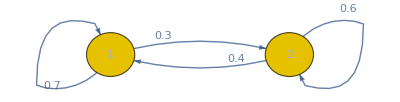

```mathematica
drawFrame[frame1]
```

We will refer to the potential experts P_i, i.e. the probability functions in the frame, as the candidates.

Notice that we can use this same structure to represent the full models of interest, where we have another function π, which may not be in the frame, and want to see whether π defers to the frame. The way to do so is just to treat world 1 as a “dummy world”, which gets assigned 0 probability by all worlds and which captures π’s credence function.  

For example, the above frame combined with a π which is 50-50 between the two candidates, ca be represented as follows:

```mathematica
frame1plus = {
{0, 0.5, 0.5},
{0, 0.7, 0.3},
{0,0.4, 0.6}
}
```

{{0,0.5,0.5},{0,0.7,0.3},{0,0.4,0.6}}

```mathematica
MatrixForm[frame1plus]
```

(0 | 0.5 | 0.5
0 | 0.7 | 0.3
0 | 0.4 | 0.6)

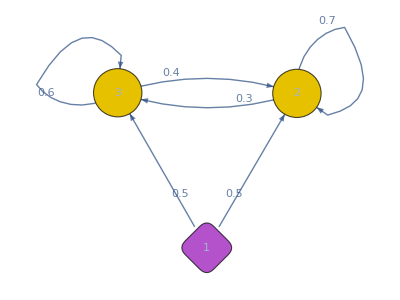

```mathematica
drawFrame[frame1plus]
```

This notebook contains special-made functions for generating, visualizing, and analyzing such frames. We will explain the functions in more detail in the sections below.

An example: we can generate a random 3-world frame:

```mathematica
frame2 = getRandFrame[3,7]
(*The second argument controls the "niceness"---how large the denominators can be*)
```

{{4/15,1/15,2/3},{0,1/2,1/2},{1/5,2/25,18/25}}

We can visualize this by looking at the frame matrix:

```mathematica
MatrixForm[frame2]
```

(4/15 | 1/15 | 2/3
0 | 1/2 | 1/2
1/5 | 2/25 | 18/25)

Or by looking at a Markov diagram of it:

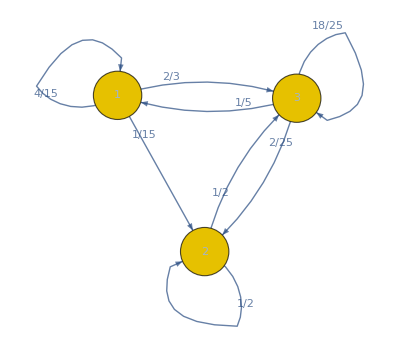

```mathematica
drawFrame[frame2]
```

Or—by far the most helpfully—by visualizing it in a barycentric plot, in which the extreme points are the probability functions that are certain of each world, and the probability functions lie within this triangle (or, more generally, simplex):

Delete::psl: Position specification none in {1,2,3} is not a machine-sized integer or a list of machine-sized integers.

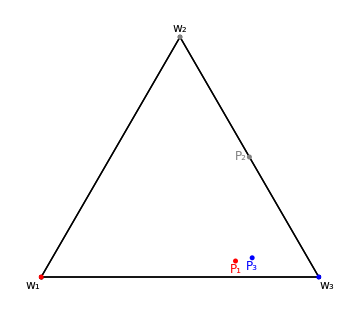

```mathematica
plot3Frame[frame2,"none"]
```

And we can check whether it satisfies various properties. For instance, such as whether it validates Simple Trust, Trust, or Total Trust:
(A frame validates a constraint if all the functions P_i in the frame obey that constraint with respect to the frame.)

```mathematica
checkSimpleTrust[frame2]
```

{False,{x[1]→4/5,x[2]→-1/5,x[3]→-1/5,t→1/5}}

```mathematica
checkTrust[frame2]
```

{False,{x[1]→0,x[2]→9/10,x[3]→-1/10,t→1/10}}

```mathematica
checkTotalTrust[frame2]
```

{False,{x[1]→-1,x[2]→-101,x[3]→21/2}}

Likewise for 4-world frames:

```mathematica
frame3 = getRandFrame[4,8]
```

{{3/28,9/28,0,4/7},{5/22,7/66,29/66,5/22},{7/66,1/6,4/11,4/11},{6/17,12/85,21/85,22/85}}

```mathematica
MatrixForm[frame3]
```

(3/28 | 9/28 | 0 | 4/7
5/22 | 7/66 | 29/66 | 5/22
7/66 | 1/6 | 4/11 | 4/11
6/17 | 12/85 | 21/85 | 22/85)

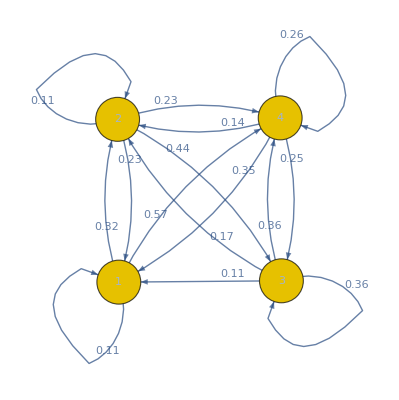

```mathematica
drawFrame[frame3//N]
```

```mathematica
plot4Frame[frame3,"none"]
(*color code: w1 and P_w1 is red; w2 and P_w2 is gray, w3 and P_w3 is blue, and w4 and P_w4 is orange *)
```

Delete::psl: Position specification none in {1,2,3,4} is not a machine-sized integer or a list of machine-sized integers.

-Graphics3D-

```mathematica
checkSimpleTrust[frame3]
```

{False,{x[1]→-4/7,x[2]→-4/7,x[3]→-4/7,x[4]→3/7,t→4/7}}

```mathematica
checkTrust[frame3]
```

{False,{x[1]→0,x[2]→0,x[3]→-1/2,x[4]→1/2,t→1/2}}

```mathematica
checkTotalTrust[frame3]
```

{False,{x[1]→-1,x[2]→-1433/309,x[3]→-410/309,x[4]→391/103}}

Such a process—especially finding frames with desired properties— can be computationally intensive. So this notebook also contains long lists of ready-made frames that have been checked to have certain properties. For example, it contains frames that validate Trust but not Total Trust (i.e. Value):

```mathematica
frame4 = trustYesValueNo[[9]]
```

{{4/13,3/13,2/13,4/13},{1/8,1/2,1/8,1/4},{1/5,3/10,3/10,1/5},{1/6,1/6,1/6,1/2}}

```mathematica
MatrixForm[frame4]
```

(4/13 | 3/13 | 2/13 | 4/13
1/8 | 1/2 | 1/8 | 1/4
1/5 | 3/10 | 3/10 | 1/5
1/6 | 1/6 | 1/6 | 1/2)

```mathematica
checkTrust[frame4]
```

True

```mathematica
checkTotalTrust[frame4]
```

{False,{x[1]→26/3,x[2]→8/3,x[3]→-1,x[4]→-67/6}}

```mathematica
plot4Frame[frame4,"none"]
```

Delete::psl: Position specification none in {1,2,3,4} is not a machine-sized integer or a list of machine-sized integers.

-Graphics3D-

For example, we can see that world 3 of this frame is not modestly informed, since it falls outside the convex hull of it’s informed self (the blue dot in the corner of the simplex) and the other functions in the frame (you have to turn it to just the right angle to notice):

```mathematica
plot4Frame[frame4,3]
```

-Graphics3D-

That gives a preview of what we’ll do; the rest of the notebook will explain the functions it contains, and give examples.  

We break it into three sections: generating frames,  visualizing frames, and analyzing frames.

NOTE: if you ever remember a function’s name, ‘FXN’, but can’t remember the inputs it requires, simply type ‘?FXN’ to receive the input (along with the code that runs it). For example:

```mathematica
?getAnyRandProbVec
```

```mathematica
?checkTotalTrust
```

In addition, the final section contains a reference list of all functions used

## Generating frames

In this section, we’ll describe the functions that go into generating probability frames, as well as the special class of them known as prior frames.

To generate a random probability frame with n worlds and a variance (amount of potential variation in probability fxn between worlds) v, use getRandFrame[n,v]:

```mathematica
frame5 = getRandFrame[3,5]
```

{{4/17,15/34,11/34},{12/31,12/31,7/31},{4/19,14/19,1/19}}

```mathematica
MatrixForm[frame5]
```

(4/17 | 15/34 | 11/34
12/31 | 12/31 | 7/31
4/19 | 14/19 | 1/19)

This function simply uses the function getAnyRandProbVec[n,v] n different times, and collects them together:

```mathematica
vec1= getAnyRandProbVec[3,5]
```

{5/14,5/28,13/28}

Given a probability vector, we might want to check it’s various properties, such as the probability it assigns to some proposition q

```mathematica
probability[vec1,{1,3}]
```

23/28

We can also condition a probability vector, and then assess it’s conditional probabilities:

```mathematica
condVec1=condition[vec1,{1,2}]
```

{2/3,1/3,0}

```mathematica
probability[condVec1,{1,3}]
```

2/3

This function is useful for generating the subframes of a frame—namely, the set of frames you can get by conditioning all the worlds in the original frame on some proposition.  (Notice, for example, that Trust is valid on a frame iff Simple Trust is valid on all of its subframes.)

```mathematica
getSubframes[frame5]
```

{{{1,0,0},{1,0,0},{1,0,0}},{{0,1,0},{0,1,0},{0,1,0}},{{0,0,1},{0,0,1},{0,0,1}},{{8/23,15/23,0},{1/2,1/2,0},{2/9,7/9,0}},{{8/19,0,11/19},{12/19,0,7/19},{4/5,0,1/5}},{{0,15/26,11/26},{0,12/19,7/19},{0,14/15,1/15}},{{4/17,15/34,11/34},{12/31,12/31,7/31},{4/19,14/19,1/19}}}

```mathematica
MatrixForm[#]&/@getSubframes[frame5]
```

{(1 | 0 | 0
1 | 0 | 0
1 | 0 | 0),(0 | 1 | 0
0 | 1 | 0
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 1
0 | 0 | 1),(8/23 | 15/23 | 0
1/2 | 1/2 | 0
2/9 | 7/9 | 0),(8/19 | 0 | 11/19
12/19 | 0 | 7/19
4/5 | 0 | 1/5),(0 | 15/26 | 11/26
0 | 12/19 | 7/19
0 | 14/15 | 1/15),(4/17 | 15/34 | 11/34
12/31 | 12/31 | 7/31
4/19 | 14/19 | 1/19)}

To get the subframe resulting from conditioning on a single proposition q, use getOneSubFrame[frame,q]:

```mathematica
getOneSubFrame[frame5,{1,2}]
```

{{8/23,15/23,0},{1/2,1/2,0},{2/9,7/9,0}}

```mathematica
MatrixForm[%]
```

(8/23 | 15/23 | 0
1/2 | 1/2 | 0
2/9 | 7/9 | 0)

Now, often we want to generate a bunch of frames that have a particular property, as a way of randomly checking frames of that kind. For example, to test a conjecture that Total Trust entails some constraint C, it is useful to randomly generate a variety of Total-Trust frames, and then check whether each of them obeys C.    If not, then you know that Total Trust does not entail that property; if so, then you get (defeasible) evidence that it does.

For example, one natural property of a frame is that it be p-reflexive, meaning that each world assigns more probability to itself than other worlds assign it: for all i,j: P_i(i) ≥ P_j(i).

Suppose we conjecture (falsely) that p-reflexivity entails Simple Trust.  One way to check this is to pull a bunch of random frames, check whether they are p-reflexive, and if so gather them up.  Then we run though the resulting list and see if Simple Trust is valid on all of them.

We have a function built in for checking p-reflexivity:

```mathematica
isPRef[frame5]
```

False

So we can use this to generate many p-reflexive frames:

```mathematica
pRefList={};
Do[frame = getRandFrame[3,3];
If[isPRef[frame]==True,AppendTo[pRefList,frame]];
,100]
```

This gives us a list of p-reflexive frames:

```mathematica
pRefList
```

{{{7/17,2/17,8/17},{4/13,4/13,5/13},{3/11,0,8/11}},{{3/7,4/7,0},{2/7,4/7,1/7},{1/4,1/8,5/8}},{{1/3,2/5,4/15},{0,4/5,1/5},{0,1/4,3/4}},{{1,0,0},{1/3,1/15,3/5},{5/13,0,8/13}},{{2/5,2/5,1/5},{1/3,1/2,1/6},{3/16,1/2,5/16}},{{9/14,5/14,0},{3/13,9/13,1/13},{0,1/2,1/2}},{{7/19,7/19,5/19},{2/17,9/17,6/17},{3/10,3/10,2/5}},{{3/5,1/5,1/5},{4/13,7/13,2/13},{7/22,7/22,4/11}},{{3/4,0,1/4},{8/19,9/19,2/19},{5/22,9/22,4/11}},{{7/12,1/6,1/4},{3/10,7/20,7/20},{0,1/3,2/3}}}

We can now check whether all of these validate Simple Trust, using the built-in function for that:

```mathematica
Do[frame = pRefList[[iter1]];
Print[{iter1,checkSimpleTrust[frame]}];
,{iter1,Length[pRefList]}]
```

{1,{False,{x[1]→-2/17,x[2]→15/17,x[3]→-2/17,t→2/17}}}

{2,{False,{x[1]→-1/7,x[2]→-1/7,x[3]→6/7,t→1/7}}}

{3,True}

{4,{False,{x[1]→8/13,x[2]→-5/13,x[3]→-5/13,t→5/13}}}

{5,{False,{x[1]→2/3,x[2]→-1/3,x[3]→-1/3,t→1/3}}}

{6,{False,{x[1]→10/13,x[2]→-3/13,x[3]→-3/13,t→3/13}}}

{7,{False,{x[1]→7/10,x[2]→-3/10,x[3]→-3/10,t→3/10}}}

{8,True}

{9,{False,{x[1]→-9/22,x[2]→13/22,x[3]→-9/22,t→9/22}}}

{10,{False,{x[1]→7/10,x[2]→-3/10,x[3]→-3/10,t→3/10}}}

So we can see that the conjecture is false, since Simple Trust is not valid on all of these frames.  (We’ll discuss more how to interpret this output below)

In fact, Simple Trust entails p-reflexivity  (suppose P_i(j) ≥ t > P_j(j).  Then P_i(j | P(j) ≥ t) = 0 < t.)  As a result, sometimes we want to generate only p-reflexive frames.  The following function (written by B.E.H.) allows us to do that efficiently. The syntax:

makePRefFrame[dim, maxIter, maxInt, seed], where

dim = the number of worlds
maxIter = the number of times the function attempts to construct a random p-reflexive frame of that size
maxInt = the “niceness” of the frame, controlling how finely the probabilities can vary
seed = an initial frame that can be used to work off of

```mathematica
frame6=makePRefFrame[3,1000,4,None]
```

{{1/2,3/8,1/8},{1/3,4/9,2/9},{1/3,1/6,1/2}}

```mathematica
makePRefFrame[3,1000,4,frame6]
```

{{4/7,1/7,2/7},{4/9,4/9,1/9},{1/6,1/6,2/3}}

```mathematica
makePRefFrame[3,1000,25,frame6]
```

{{12/23,9/23,2/23},{15/46,11/23,9/46},{9/47,22/47,16/47}}

```mathematica
makePRefFrame[3,1000,100,frame6]
```

{{48/109,37/218,85/218},{31/151,86/151,34/151},{9/115,10/23,56/115}}

We can also use this to generate a “n+1 frame”, with n worlds (n candidates for the expert) plus one probability function outside the frame (π), which we imagine deferring to it. Again, we model this by making the first world a “dummy world” that no world assigns positive probability to:
syntax: makePRefDimPlusFrame[n,niceness], where 
n = number of worlds in frame, and 
niceness = how much they can vary

```mathematica
frame7=makePRefDimPlusFrame[3,10]
```

{{0,9/23,4/23,10/23},{0,9/25,9/25,7/25},{0,1/9,5/9,1/3},{0,3/11,3/11,5/11}}

```mathematica
MatrixForm[frame7]
```

(0 | 9/23 | 4/23 | 10/23
0 | 9/25 | 9/25 | 7/25
0 | 1/9 | 5/9 | 1/3
0 | 3/11 | 3/11 | 5/11)

```mathematica
MatrixForm[frame7]//N
```

(0. | 0.391304 | 0.173913 | 0.434783
0. | 0.36 | 0.36 | 0.28
0. | 0.111111 | 0.555556 | 0.333333
0. | 0.272727 | 0.272727 | 0.454545)

### Prior frames, and trees

We can also generate a special subclass of probability frames known as prior frames (footnote 19 of the draft), in which there is a single (regular) prior, ρ, such that the probabilities at each world can be recovered by conditioning ρ on a particular proposition:  ∀w ∈ W there is a R_w ⊆ W such that P_w(•) = ρ(•|R_w).  

Such frames can be thought of as standard Kripke frames, wherein R_w is the set of worlds accessible from world w; it induces a binary relation R such that wRx iff x ∈ R_w.  
In such a frame, the R_w are called the neighborhoods. We can generate such a frame by picking a prior and some neighborhoods over a fixed set of worlds:

```mathematica
prior = getRegProbVec[4,5]
nbds = getRandNbds[5]
```

{2/5,1/10,2/5,1/10}

{{1,{2,5}},{2,{2,3,4}},{3,{1}},{4,{2}},{5,{4}}}

```mathematica
frame8=getFrame[prior,nbds]
```

{{0,1,0,0},{0,1/6,2/3,1/6},{1,0,0,0},{0,1,0,0}}

```mathematica
MatrixForm[frame8]
```

(0 | 1 | 0 | 0
0 | 1/6 | 2/3 | 1/6
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

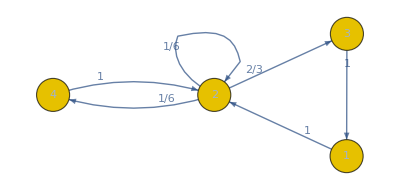

```mathematica
drawFrame[frame8]
```

Within prior frames, Value/Total Trust / Trust are each equivalent to the claim that the the neighborhoods form a tree (really, a “forest”): they are transitive (if x ∈ R_w,  then R_x ⊆ R_w), shift-reflexive (if x ∈ R_w, then x ∈ R_x), and shift-nested (if x,y ∈ R_w, then either R_x ⊆ R_y or R_x ⊇ R_y or R_x ∩ R_y = ∅).  (Geanakoplos 1989, Theorem 1; Dorst 2020, Theorem 7.4)

We can efficiently generate very large such structures using a computational trick: the neighborhoods form a forest iff each world w can be associated with a sequence f(w) such that x ∈ R_w iff f(w) is an initial segment of f(x).  (Dorst 2020, Theorem 5.8).
There are three functions involved in doing this. The first simply generates random neighborhoods for a given frame size, with two parameters to modulate the structure of the tree.

getRandTreeNbhds[frameSize, seqPoolSize, seqLength] , where

frameSize = the number of worlds in the frame
seqPoolSize = the size of the set of objects we are pulling random sequences from. The smaller the pool, the more likely it is that one world’s sequence will be an initial segment of another; the larger, the less likely this is.
seqLength = the max length of sequences we generate.  This determines the maximum depth of the trees in the frame

The output of getRandTreeNbhds is several things. First, it gives you a sequence of {w, R_w} for each world w.  Second, it assigns “nbd[w]” to R_w.  This output is then used by the graphTree function to diplay the structure:

{{1,{1}},{2,{2}},{3,{1,2,3,4,5}},{4,{1,2,3,4,5}},{5,{2,5}}}

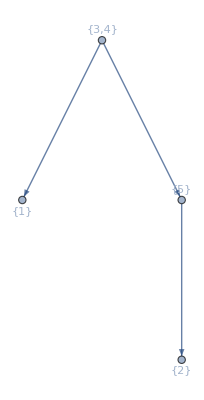

```mathematica
getRandTreeNbhds[5,2,2]
graphTree
```

{{1,{1}},{2,{2,4,6,7,9,10}},{3,{1,2,3,4,5,6,7,8,9,10}},{4,{4,9}},{5,{5,8}},{6,{2,4,6,7,9,10}},{7,{2,4,6,7,9,10}},{8,{5,8}},{9,{4,9}},{10,{2,4,6,7,9,10}}}

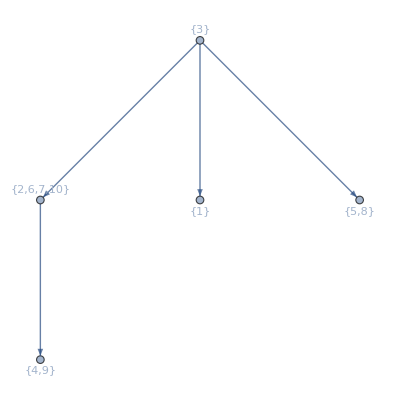

```mathematica
getRandTreeNbhds[10,2,2]
graphTree
```

{{1,{1,3,4,9,10}},{2,{1,2,3,4,5,9,10}},{3,{1,3,4,9,10}},{4,{1,3,4,9,10}},{5,{1,2,3,4,5,9,10}},{6,{1,2,3,4,5,6,7,8,9,10}},{7,{1,2,3,4,5,6,7,8,9,10}},{8,{1,2,3,4,5,8,9,10}},{9,{9}},{10,{1,3,4,9,10}}}

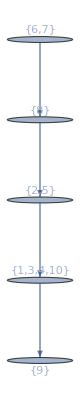

```mathematica
getRandTreeNbhds[10,1,4]
graphTree
```

{{1,{1,3}},{2,{2,8,10}},{3,{3}},{4,{4,5,9}},{5,{5}},{6,{6}},{7,{1,2,3,4,5,6,7,8,9,10}},{8,{8}},{9,{4,5,9}},{10,{10}}}

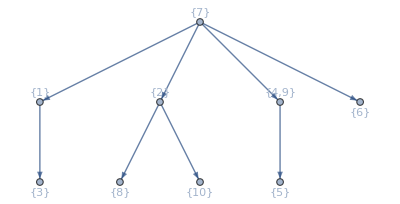

```mathematica
getRandTreeNbhds[10,4,4]
graphTree
```

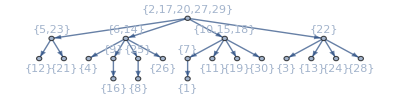

```mathematica
getRandTreeNbhds[30,4,4];
graphTree
```

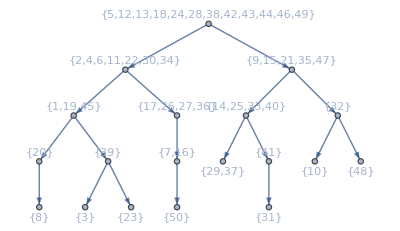

```mathematica
getRandTreeNbhds[50,2,4];
graphTree
```

This function simply gives the structure of the prior frame; we need to add a prior in order to recover the probabilities at each world.  The function 

getRandTreeFrame[frameSize, seqPoolSize, seqLength]

uses the getRandTreeNbhds function, and then lays a regular prior over it to recover the probabilities at each world:

In doing so, it assigns frame” to the resulting probability frame this generates

```mathematica
getRandTreeFrame[5,2,2]
```

(1/2 | 0 | 0 | 1/2 | 0
3/14 | 2/7 | 1/14 | 3/14 | 3/14
3/14 | 2/7 | 1/14 | 3/14 | 3/14
1/2 | 0 | 0 | 1/2 | 0
3/14 | 2/7 | 1/14 | 3/14 | 3/14)

```mathematica
frame
```

{{1/2,0,0,1/2,0},{3/14,2/7,1/14,3/14,3/14},{3/14,2/7,1/14,3/14,3/14},{1/2,0,0,1/2,0},{3/14,2/7,1/14,3/14,3/14}}

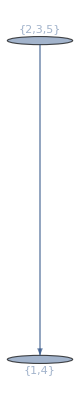

```mathematica
graphTree
```

```mathematica
getRandTreeFrame[8,2,2]
```

(1/4 | 0 | 0 | 1/4 | 0 | 0 | 1/2 | 0
0 | 2/7 | 0 | 0 | 0 | 0 | 0 | 5/7
1/22 | 1/11 | 2/11 | 1/22 | 1/11 | 5/22 | 1/11 | 5/22
1/4 | 0 | 0 | 1/4 | 0 | 0 | 1/2 | 0
1/22 | 1/11 | 2/11 | 1/22 | 1/11 | 5/22 | 1/11 | 5/22
1/22 | 1/11 | 2/11 | 1/22 | 1/11 | 5/22 | 1/11 | 5/22
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

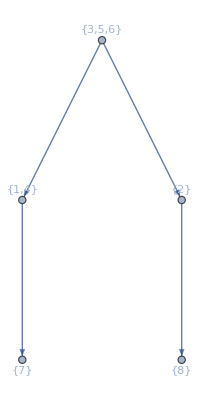

```mathematica
graphTree
```

This function can be very useful for efficiently generating and checking properties of large validating frames—with the caveat that it only looks at the subset of them that are prior frames, of course.

### Frame lists

Finally, since it can be computationally expensive to generate frames with various properties, this notebook comes pre-loaded with a variety
“priorframes” consists of a list of 100 randomly generated prior frames. None validate Trust or Total Trust

```mathematica
Length[priorFrames]
```

100

```mathematica
frame = priorFrames[[14]]
```

{{1,0,0,0},{1/2,0,1/2,0},{0,1/2,0,1/2},{0,1,0,0}}

```mathematica
checkTrust[frame]
```

{False,{x[1]→0,x[2]→0,x[3]→0,x[4]→-1,t→1}}

“priorTrees” consists of 100 randomly generated tree-shaped prior frames, which validate (Total) Trust

```mathematica
Length[priorTrees]
```

100

```mathematica
frame = priorTrees[[85]]
```

{{2/5,3/10,1/10,1/5},{0,3/4,1/4,0},{0,0,1,0},{0,0,0,1}}

```mathematica
checkTotalTrust[frame]
```

{True}

“noTrust” includes 48 frames that do not validate Trust but are p-reflexive

```mathematica
Length[noTrust]
```

48

```mathematica
frame = noTrust[[37]]
```

{{3/7,1/7,2/7,1/7},{2/11,3/11,3/11,3/11},{1/6,1/6,1/3,1/3},{1/5,1/5,1/5,2/5}}

```mathematica
isPRef[frame]
```

True

```mathematica
checkTrust[frame]
```

{False,{x[1]→0,x[2]→0,x[3]→-1/2,x[4]→1/2,t→1/2}}

trustYesValueNo includes 4-world frames that validate Trust but not Total Trust / Value

```mathematica
Length[trustYesValueNo]
```

32

```mathematica
frame = trustYesValueNo[[24]]
```

{{4/15,4/15,4/15,1/5},{1/10,2/5,3/10,1/5},{1/9,1/3,1/3,2/9},{1/12,1/3,1/4,1/3}}

```mathematica
checkTrust[frame]
```

True

```mathematica
checkTotalTrust[frame]
```

{False,{x[1]→-1,x[2]→-41,x[3]→27,x[4]→20}}

TrustYesValueYes includes 4-world frames that validate both Trust and Total Trust/Value

```mathematica
Length[trustYesValueYes]
```

69

```mathematica
frame = trustYesValueYes[[53]]
```

{{4/11,1/11,3/11,3/11},{2/11,4/11,2/11,3/11},{2/9,1/9,1/3,1/3},{1/7,1/7,1/7,4/7}}

```mathematica
checkTotalTrust[frame]
```

{True}

totalTrustFrames includes more 4-world frames that validate total-Trust

```mathematica
Length[totalTrustFrames]
```

99

```mathematica
frame = totalTrustFrames[[28]]
checkTotalTrust[frame]
```

{{3/8,1/8,3/8,1/8},{1/6,1/6,1/2,1/6},{1/7,1/7,4/7,1/7},{3/11,1/11,3/11,4/11}}

{True}

totalTrust5Frames includes a few 5-world frames that validate Total Trust  (these are computationally difficult to find—or at least they were before we knew that we could generate them using the modestly-informed constraint)

```mathematica
Length[totalTrust5Frames]
```

10

```mathematica
frame = totalTrust5Frames[[3]]
checkTotalTrust[frame]
```

{{1/3,1/9,1/3,1/9,1/9},{1/4,1/6,1/4,1/6,1/6},{1/4,1/8,3/8,1/8,1/8},{3/13,1/13,3/13,3/13,3/13},{1/4,1/12,1/4,1/6,1/4}}

{True}

allValueProbFrames collects a large list of probability frames that validate Value / Total Trust

```mathematica
Length[allValueProbFrames]
```

334

Finally, “pRefCondConvFrames” includes frames that are both p-reflexive and which are conditionally convex, which means that for each world i and proposition q, P_i(•|q) is in the convex hull of the P_j(•|q) such that j ∈ q.  (This is a generalization of the “Reaction” constraint from Dorst 2020, §5.)
All of them validate Value; so we conjecture that p-reflexivity + conditional-convexity entails Value

```mathematica
Length[pRefCondConvFrames]
frame = pRefCondConvFrames[[37]]
```

156

{{4/13,2/13,4/13,3/13},{1/8,1/2,1/8,1/4},{1/8,1/8,1/2,1/4},{1/5,1/5,1/5,2/5}}

```mathematica
checkTotalTrust[frame]
```

{True}

## Visualizing Frames

As we’ve seen with prior frames, certain frames are much easier to work with than others because they can be easily visualized.  In our experience, this has been crucial for figuring out the constraints needed to validate certain principles.

Prior frames are easy to work with because they can be drawn simply as Kripke frames, with numbers assigned to worlds in order to recover their probabilities.  That, for instance, is how I  found that Trust was equivalent to the claim that the neighborhoods formed a tree---simply by drawing examples and checking whether they satisfied it.

In order to work with general probability frames, we need similar methods for visualizing them.  The two simplest and most general are simply to draw them in stochastic-matrix of Markov-diagram notation:

```mathematica
frame9 = getRandFrame[4,5]
```

{{2/25,2/25,6/25,3/5},{0,7/32,15/32,5/16},{6/31,18/31,0,7/31},{0,2/5,2/5,1/5}}

matrix notation:

```mathematica
MatrixForm[frame9]
```

(2/25 | 2/25 | 6/25 | 3/5
0 | 7/32 | 15/32 | 5/16
6/31 | 18/31 | 0 | 7/31
0 | 2/5 | 2/5 | 1/5)

Markov diagram:

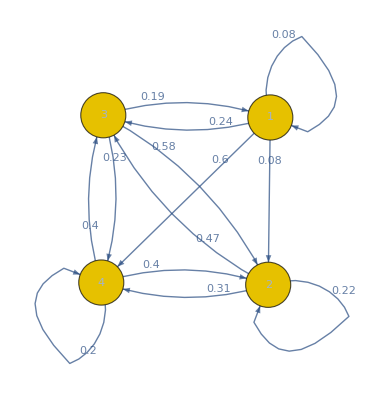

```mathematica
drawFrame[frame9//N]
```

Unfortunately, these are not particularly illuminating to stare at. (Believe me, I’ve tried.)
The best method is to visualize them geometrically, treating each probability function as a vector in Euclidean n-space, for n the number of worlds, as discussed at length in DDB.  Unfortunately, this only works up to a few dimensions; but it nevertheless makes it much easier to glob onto the necessary structures.

### Plotting 3-world frames

We visualize this in a barycentric plot, which contains n extreme points, and each probability function over those n worlds is an average between them.  In 3 dimensions this is a triangle. The command for plotting a 3-world frame is

plot3Frame[frame, cut],  where 

frame = the frame of interest, and
cut = the world i you wish to cut out to form the convex hull \hat{P_i} ∪ {P_j: P_j≠P_i},  i.e. the set that P_i must fall within in order to be modestly informed.  cut takes the values "none", 1, 2,...,n, or "all" do represent all such cuts at once.

Note that whenever each P_i is unique in the frame, then \hat{P_i} is simply the extreme point focused on world i.  (Unfortunately, the way the "cut" system is written, it only works properly when each P_i is unique, since it always replaces P_i with it's world i)

```mathematica
frame10 = {
{1/3, 1/3,1/3},
{1/4, 1/2, 1/4},
{1/4, 1/4, 1/2}
};
MatrixForm[frame10]
```

(1/3 | 1/3 | 1/3
1/4 | 1/2 | 1/4
1/4 | 1/4 | 1/2)

Plot 3-world frames with (ignore the red “Delete”—it’s just how a piece of the code reacts to the “none” input)

Delete::psl: Position specification none in {1,2,3} is not a machine-sized integer or a list of machine-sized integers.

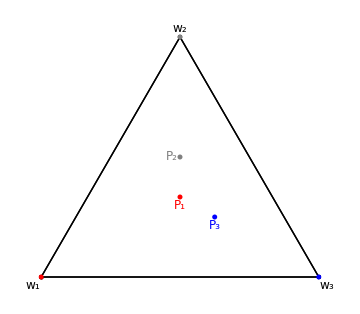

```mathematica
plot3Frame[frame10,"none"]
```

As we can see, P_1 is modestly informed, since it lies inside the yellow convex hull:

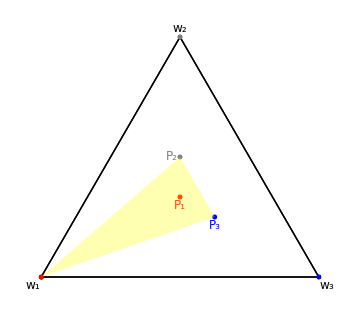

```mathematica
plot3Frame[frame10,1]
```

Likewise (just barely) for P_2:

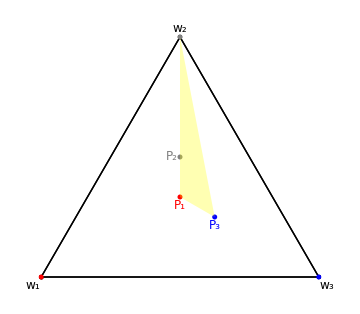

```mathematica
plot3Frame[frame10,2]
```

And P_3:

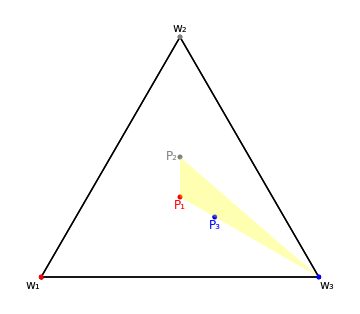

```mathematica
plot3Frame[frame10,3]
```

We can display them all together:

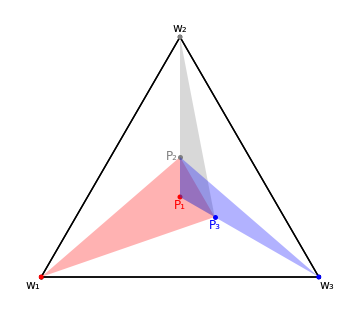

```mathematica
plot3Frame[frame10,"all"]
```

And indeed we can verify (more on this in the next section) that the frame validates Total Trust (and hence Value):

```mathematica
checkTotalTrust[frame10]
```

{True}

Suppose we alter the frame slightly by shifting P_3’s probability for P_2 slightly lower

```mathematica
frame11 ={
{1/3, 1/3,1/3},
{1/4, 1/2, 1/4},
{1/4+0.03, 1/4-0.09, 1/2+0.06}
};
```

```mathematica
MatrixForm[frame11//N]
```

(0.333333 | 0.333333 | 0.333333
0.25 | 0.5 | 0.25
0.28 | 0.16 | 0.56)

Delete::psl: Position specification none in {1,2,3} is not a machine-sized integer or a list of machine-sized integers.

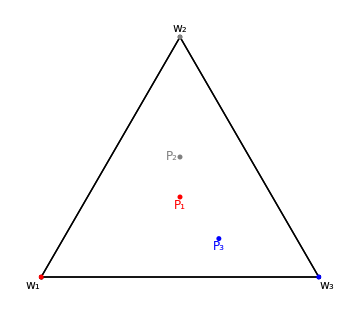

```mathematica
plot3Frame[frame11,"none"]
```

We can see that P_3 now falls outside the relevant convex hull:

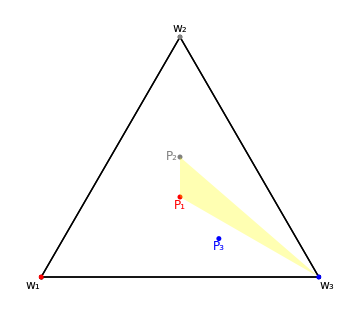

```mathematica
plot3Frame[frame11,3]
```

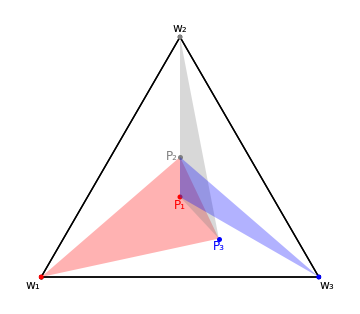

```mathematica
plot3Frame[frame11,"all"]
```

And, indeed, Total Trust now fails:

```mathematica
checkTotalTrust[frame11]
```

{False,{x[1]→-2.33333,x[2]→2.33333,x[3]→0.}}

(It was looking at pairs of frames like this and checking each for Total Trust, by the way, which allowed us to cotton on to the characterization in terms of modest-informedness.)

To manipulate a frame by hand, you can use the visualize3Frame function (don’t worry about the red):

(NOTE: sometimes—I’m not sure why—this visualization starts constantly recomputing without any input, which can slow your machine down. wrap the below command in (* *) and execture it to stop this, i.e. write
(* visualize3Frame *)
then hit shift + enter

```mathematica
visualize3Frame
```

This function displays a variety of things, with a variety of options.  The sliders allow you to control the probabilities at each world.  ‘w1’ is how self-confident P_1 is, i.e. P_1(1). ‘w1b’ is the balance P_1 gives between worlds 2 and 3, so w1b = P_1(2|2 or 3).  Similarly, w2 is P_2(2), and w2b is P_2(1| 1 or 3); and w3 is P_3(3) and w3b is P_3(1| 1 or 2).  By sliding these arround, you can move the functions aroudn the triangle (try it!)

(Confusing things:
– the color code is red = P_1, gray  = P_2, blue = P_3
– unlike our other diagrams, w1 is in the bottom right, w2 is in the bottom left, and w3 is in the top.  (One day I’ll get around to fixing this...))

The purple dot is the stationary distribution of the frame, i.e. the (unique) probability function ρ such that, where F is the frame matrix, ρF = ρ.  Equivalently, ρ expectation-matches the frame, meaning that for all q: ρ(q) = 𝔼_ρ(P(q)), where ‘P’ is a definite description for the expert probability function.  Raising the matrix F to higher and higher powers leads each of the functions in it to converge to this stationary (this is the Markov chain convergence theorem; a consequence of the Perron-Frobenius theorem).  The “power” function allow you to see this convergence in steps, with orange dots that move toward the purple one.  We’ll talk a bit more about stationaries later.

Finally, the row with the “no lines” option, and the “delete” row allow you to look at various subframes of the frame, i.e. the result of conditioning all the functions in the frame on a given proposition.  Conditioning them on ¬{1} projects each function through the line between it and the extreme point 1, for instance.

Once you do this, you may notice that the purple and orange dots come apart. The purple is the result of conditioning the original stationary distribution on the proposition in question. The orange dot is the result of first conditioning every world in the frame on that proposition, and then taking their stationary.   The fact that these can come apart is both formally and perhaps philosophically interesting—Daniel Rothschild has some cool results about this.

### 3+-frames and 4-frames

Okay enough of that rabbit hole.  Final things to show with visualization:

As demonstrated at the beginning, we can visualize a 3+1 frame which has an extra probability function over it:

```mathematica
frame13 = makePRefDimPlusFrame[3,5]
```

{{0,1/7,4/7,2/7},{0,1/2,1/3,1/6},{0,5/11,5/11,1/11},{0,4/9,1/3,2/9}}

```mathematica
MatrixForm[frame13]
```

(0 | 1/7 | 4/7 | 2/7
0 | 1/2 | 1/3 | 1/6
0 | 5/11 | 5/11 | 1/11
0 | 4/9 | 1/3 | 2/9)

Delete::psl: Position specification none in {1,2,3} is not a machine-sized integer or a list of machine-sized integers.

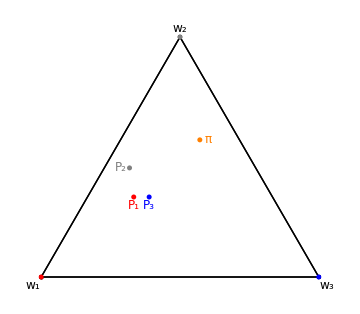

```mathematica
plot3PlusFrame[frame13,"none"]
```

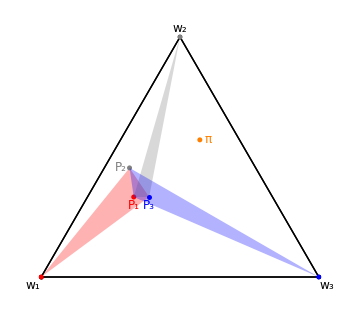

```mathematica
plot3PlusFrame[frame13,"all"]
```

We can visualize 4-world frames using a 3D barycentric plot
(color-code:  
red = w1 and P_1,  
gray = w2 and P_2
blue = w3 and P_3
orange = w4 and P_4

```mathematica
frame14 = getRandFrame[4,10]
```

{{13/77,10/77,25/77,29/77},{1/24,1/24,7/8,1/24},{8/55,23/55,9/55,3/11},{27/103,16/103,30/103,30/103}}

```mathematica
plot4Frame[frame14,"none"]
```

Delete::psl: Position specification none in {1,2,3,4} is not a machine-sized integer or a list of machine-sized integers.

-Graphics3D-

```mathematica
plot4Frame[frame14,1]
```

-Graphics3D-

For example here is a modestly-informed 4-frame:

```mathematica
frame15 = totalTrustFrames[[30]]
plot4Frame[frame15,"all"]
```

{{2/5,1/5,1/5,1/5},{1/4,1/2,1/8,1/8},{2/11,2/11,4/11,3/11},{1/8,1/8,1/4,1/2}}

-Graphics3D-

### Higher dimensions

Obviously there are hard limits on how much we can visualize in higher dimensions. But one strategy is to take various subframes of a higher-dimensional frame to see the “shadow” it casts in lower dimensions.  
So, for instance, we can take a 5-world Total Trust frame, and look at all the 4-world subframes it generates—i.e. those obtained by conditioning on the negation of a given world thus projecting away from that world in the 4D simplex that covers  this frame’s barycentric plot

```mathematica
frame16 = totalTrust5Frames[[2]]
```

{{1/4,1/4,1/4,1/8,1/8},{1/7,3/7,1/7,1/7,1/7},{1/7,1/7,3/7,1/7,1/7},{1/5,1/5,1/5,1/5,1/5},{2/9,2/9,2/9,1/9,2/9}}

```mathematica
MatrixForm[frame16]
```

(1/4 | 1/4 | 1/4 | 1/8 | 1/8
1/7 | 3/7 | 1/7 | 1/7 | 1/7
1/7 | 1/7 | 3/7 | 1/7 | 1/7
1/5 | 1/5 | 1/5 | 1/5 | 1/5
2/9 | 2/9 | 2/9 | 1/9 | 2/9)

```mathematica
subframes = Table[getOneSubFrame[frame16,Delete[{1,2,3,4,5},iter]],{iter,1,5}];
MatrixForm[#]&/@subframes
```

{(0 | 1/3 | 1/3 | 1/6 | 1/6
0 | 1/2 | 1/6 | 1/6 | 1/6
0 | 1/6 | 1/2 | 1/6 | 1/6
0 | 1/4 | 1/4 | 1/4 | 1/4
0 | 2/7 | 2/7 | 1/7 | 2/7),(1/3 | 0 | 1/3 | 1/6 | 1/6
1/4 | 0 | 1/4 | 1/4 | 1/4
1/6 | 0 | 1/2 | 1/6 | 1/6
1/4 | 0 | 1/4 | 1/4 | 1/4
2/7 | 0 | 2/7 | 1/7 | 2/7),(1/3 | 1/3 | 0 | 1/6 | 1/6
1/6 | 1/2 | 0 | 1/6 | 1/6
1/4 | 1/4 | 0 | 1/4 | 1/4
1/4 | 1/4 | 0 | 1/4 | 1/4
2/7 | 2/7 | 0 | 1/7 | 2/7),(2/7 | 2/7 | 2/7 | 0 | 1/7
1/6 | 1/2 | 1/6 | 0 | 1/6
1/6 | 1/6 | 1/2 | 0 | 1/6
1/4 | 1/4 | 1/4 | 0 | 1/4
1/4 | 1/4 | 1/4 | 0 | 1/4),(2/7 | 2/7 | 2/7 | 1/7 | 0
1/6 | 1/2 | 1/6 | 1/6 | 0
1/6 | 1/6 | 1/2 | 1/6 | 0
1/4 | 1/4 | 1/4 | 1/4 | 0
2/7 | 2/7 | 2/7 | 1/7 | 0)}

```mathematica
get4FrameShadows[fiveFrame_]:=(
subframes = Table[getOneSubFrame[fiveFrame,Delete[Range[5],iter]],{iter,5}];
Return[Table[Transpose[Delete[Transpose[Delete[subframes[[iter]],iter]],iter]],{iter,5}]]
)
```

```mathematica
shadows=get4FrameShadows[frame16]
```

{{{1/2,1/6,1/6,1/6},{1/6,1/2,1/6,1/6},{1/4,1/4,1/4,1/4},{2/7,2/7,1/7,2/7}},{{1/3,1/3,1/6,1/6},{1/6,1/2,1/6,1/6},{1/4,1/4,1/4,1/4},{2/7,2/7,1/7,2/7}},{{1/3,1/3,1/6,1/6},{1/6,1/2,1/6,1/6},{1/4,1/4,1/4,1/4},{2/7,2/7,1/7,2/7}},{{2/7,2/7,2/7,1/7},{1/6,1/2,1/6,1/6},{1/6,1/6,1/2,1/6},{1/4,1/4,1/4,1/4}},{{2/7,2/7,2/7,1/7},{1/6,1/2,1/6,1/6},{1/6,1/6,1/2,1/6},{1/4,1/4,1/4,1/4}}}

```mathematica
Do[Print[plot4Frame[shadows[[iter1]],"all"]];
,{iter1,5}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

(Unfortunately, this doesn’t (yet) have the functionality to plot the probabilities of the world that has been ruled out, so e.g. in the first shadow we’ve plotted P_2(•|¬{1}), P_3(•|¬{1}), etc., but not P_1(•|¬{1}))

## Analyzing frames

Suppose we’ve generated and/or visualized some frames.  In order to draw useful from conclusions from this, we need functions that can efficiently what properties they have.  If you’re exploring the constraints imposed by a given deference principle, the best strategy is to write a custom “frame checker” for that principle, and then to generate many frames and see what the ones that validate that principle have in common.

### An in-depth example:

To illustrate the methodology, we’ll illustrate how we discovered the modestly-informed characterization of Total Trust. First, we make a function that can check a frame for whether it validates Total Trust:

```mathematica
frame17 = totalTrustFrames[[25]]
frame18=trustYesValueNo[[17]]
```

{{1/3,1/3,1/9,2/9},{1/6,1/2,1/6,1/6},{1/8,1/4,1/2,1/8},{1/9,1/3,1/9,4/9}}

{{2/5,2/5,1/10,1/10},{1/3,4/9,1/9,1/9},{2/7,2/7,2/7,1/7},{3/13,4/13,2/13,4/13}}

```mathematica
checkTotalTrust[frame17]
checkTotalTrust[frame18]
```

{True}

{False,{x[1]→20,x[2]→-45/2,x[3]→-1,x[4]→7}}

Here’s the code for the function; the way it works is as follows. (Skip this if you don’t care about the details.)  For Total Trust , for any random variable X:

E_π(X | E(X) ≥ t) ≥ t.

Noting that X-t is also a random variable, this is equivalent to: for any random varaible Y,

E_π(Y | E(Y) ≥ 0 ) ≥ 0.

As explained in the paper, this can hold for some π iff it holds for each world in the frame, i.e. where E_i is world i’s expectation function, we have that for all i and random variables Y,

E_i(Y | E(Y)≥0) ≥ 0.

Given a frame, the function generates an algebraic expression which says what it would mean for this to fail for an arbitrary Y, and then  calls Mathematica’s (very powerful, but very computationally expensive) “FindInstance” function to see if it can find a random variable that meets those constraints.  If it finds  such, it gives the relevant random variable; if it establishes that there is no such variable, it says that Total Trust is valid.

In detail:

```mathematica
checkTotalTrust[frame_]:=(size=Length[frame]; (*determine the number of worlds*)
vec=Table[x[i],{i,size}]; (*generate a random variable X of that size*)
expVec=frame.vec; (*use frame to calculate expected values of that variable*)
possNonNeg=Subsets[Range[size]]; (*generate lise of possible sets of worlds at which X could have non-negative expectation i.e. [E(X)≥0]*)
listOfConditionals={};Do[nonNegCase=possNonNeg⟦nonNegIter⟧; (*run through possible sets, construct a series of conditonals which assert what it would mean for that instance of Total Trust to fail*)negCases=Complement[Range[size],nonNegCase];vecStar=ReplacePart[vec,(#1->0&)/@Complement[Range[size],nonNegCase]];AppendTo[listOfConditionals,And@@(expVec⟦#1⟧≥0&)/@nonNegCase&&And@@(expVec⟦#1⟧<0&)/@negCases⇒!And@@((frame.vecStar)⟦#1⟧≥0&)/@Range[size]];,{nonNegIter,Length[possNonNeg]}];vecConstraints=FullSimplify[And@@listOfConditionals]; (*combine and simplify those constraints*)
result=FindInstance[vecConstraints,vec,Reals]; (*see if it's possible to find a random variable that meets those constraints*)
If[result=={},Return[{True}],Return[{False,Flatten[result]}]];) (*Either output "{True}" if there is no X, or return {False, [example]}, where the example is the assignment of values to X at the various worlds that leads to the failure*)
```

We can then generate a variety of frames, and sort them into those that did and did not validate total trust, for example with code like the following: (this takes about a minute to run on my machine):

```mathematica
Timing[newTTFrames = {};
newNonTTFrames = {};
Do[frame = getRandFrame[3,2];
result = checkTotalTrust[frame];
If[result[[1]]==True, AppendTo[newTTFrames,frame]];
If[result[[1]]==False, AppendTo[newNonTTFrames,frame]];
,200]]
```

{65.6703,Null}

```mathematica
newTTFrames
```

{{{2/3,1/9,2/9},{6/11,3/11,2/11},{2/7,1/7,4/7}},{{1/4,1/3,5/12},{2/13,6/13,5/13},{0,0,1}},{{2/3,0,1/3},{1/3,1/2,1/6},{1/3,0,2/3}},{{3/4,1/4,0},{0,1,0},{0,3/7,4/7}},{{1/2,1/10,2/5},{2/5,1/5,2/5},{3/8,1/8,1/2}},{{5/11,3/11,3/11},{5/14,3/7,3/14},{1/4,1/4,1/2}}}

```mathematica
newNonTTFrames[[1;;10]]
```

{{{5/7,2/7,0},{3/4,1/4,0},{3/11,4/11,4/11}},{{2/5,3/5,0},{1/2,0,1/2},{5/12,5/12,1/6}},{{3/8,5/8,0},{0,1/3,2/3},{1/3,4/9,2/9}},{{6/17,6/17,5/17},{1/2,1/10,2/5},{1/4,3/4,0}},{{1/4,5/12,1/3},{5/11,4/11,2/11},{3/8,1/2,1/8}},{{4/13,6/13,3/13},{0,2/5,3/5},{1/2,1/3,1/6}},{{6/11,5/11,0},{1/2,0,1/2},{2/11,6/11,3/11}},{{1/2,1/3,1/6},{5/11,6/11,0},{0,2/3,1/3}},{{5/13,2/13,6/13},{0,1/4,3/4},{0,1/2,1/2}},{{1/5,1/2,3/10},{1/4,0,3/4},{1/2,1/6,1/3}}}

We can then try to notice differences between the two sets of frames by visualizing them

Delete::psl: Position specification none in {1,2,3} is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

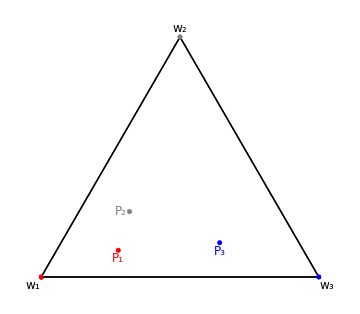
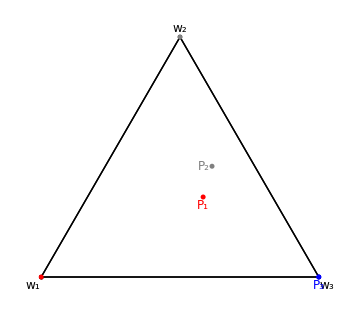
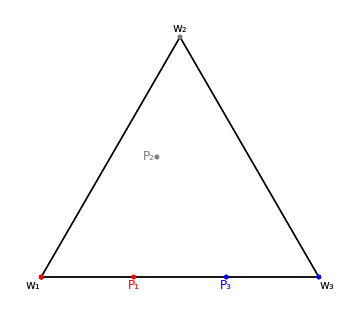
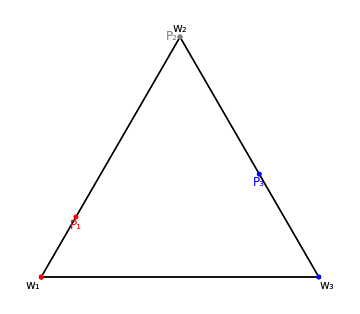
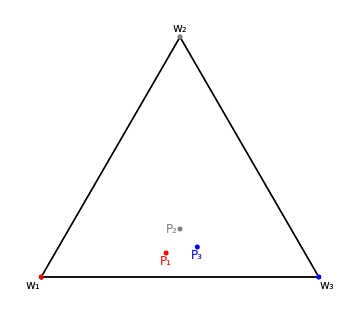
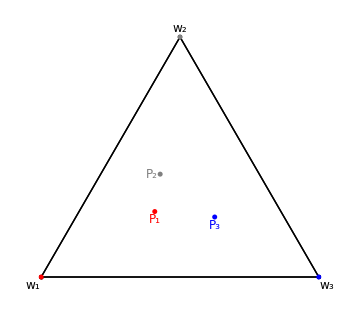

```mathematica
plot3Frame[#,"none"]&/@newTTFrames
```

Delete::psl: Position specification none in {1,2,3} is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

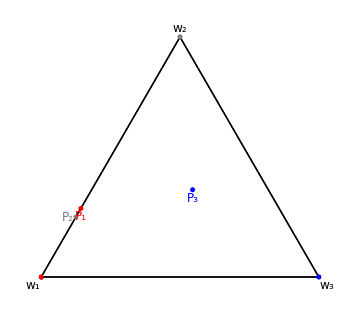
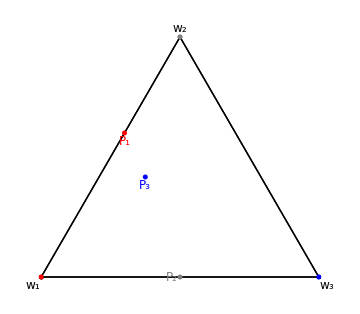
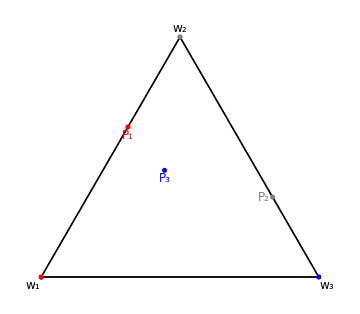
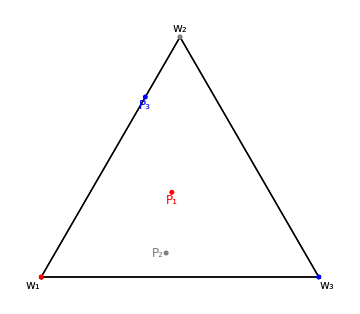
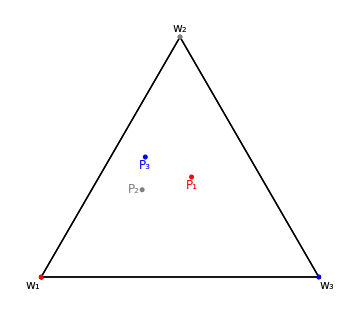

```mathematica
plot3Frame[#,"none"]&/@newNonTTFrames[[1;;5]]
```

Staring at these frames, we can see that the former are modestly informed and the latter are not

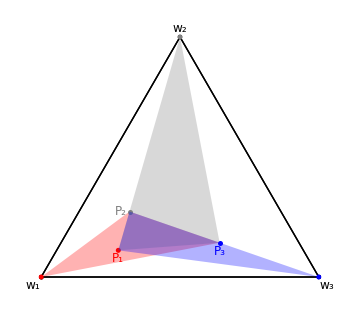
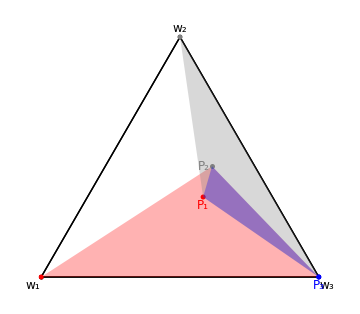
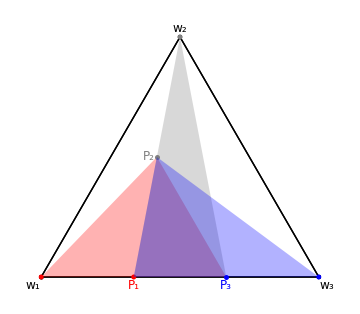
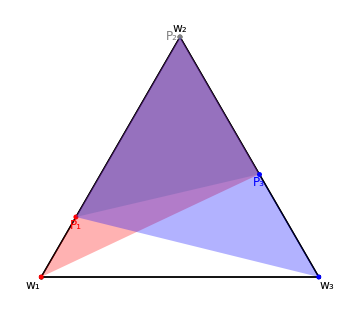
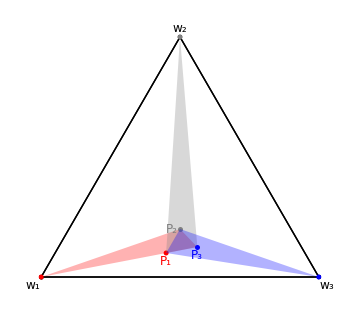
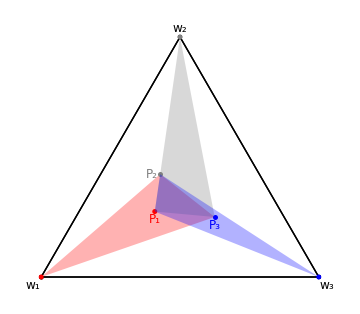

```mathematica
plot3Frame[#,"all"]&/@newTTFrames
```

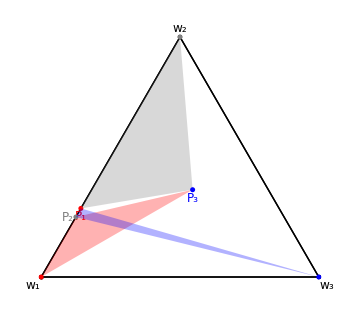
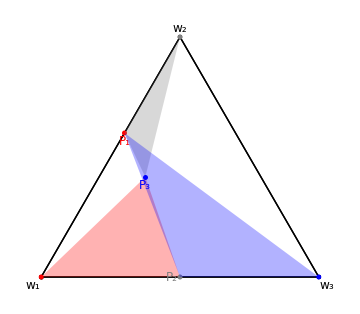
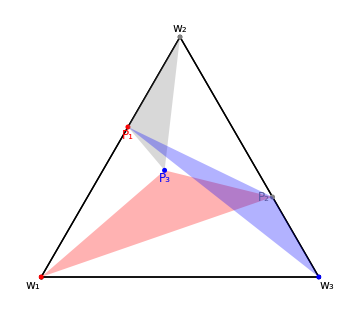
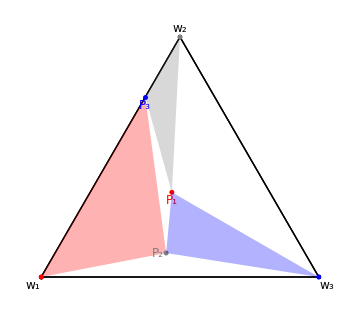
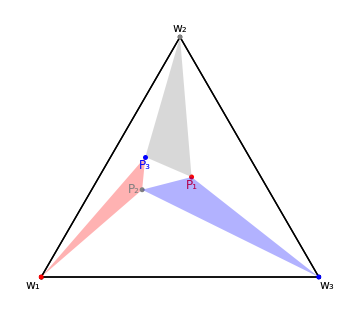

```mathematica
plot3Frame[#,"all"]&/@newNonTTFrames[[1;;5]]
```

Once we form a conjecture like this, we can make a checker for the relevant property (modest-informedness), and see whether this matches the verdicts for Total Trust across all  examples we have.  The following function checks that:

```mathematica
checkMI[newTTFrames[[1]]]
```

True

```mathematica
checkMI[newNonTTFrames[[1]]]
```

{False,{1,2,3}}

```mathematica
Do[frame = trustYesValueNo[[iter]];
Print[checkMI[frame]],
{iter,10}]
```

{False,{1}}

{False,{2,3}}

{False,{4}}

{False,{1}}

{False,{3}}

{False,{2,4}}

{False,{2}}

{False,{1,2}}

{False,{3,4}}

{False,{2}}

```mathematica
Do[frame = trustYesValueYes[[iter]];
Print[checkMI[frame]],
{iter,10}]
```

True

True

True

«7 more identical outputs»

Once we get results like these, we can go about looking for an analytic proof

### Summary of checkers

This subsection summarizes the checkers built in to the above functions.  All of them check whether the principle is valid on the frame, i.e. whether for all probability functions P_i in the frame, they obey the relevant constraint.

Total Trust/Value:    E_i(X | E(X)≥t) ≥ t,  for all X,t, for all worlds i

```mathematica
checkTotalTrust[totalTrustFrames[[2]]]
checkTotalTrust[noTrust[[31]]]
```

{True}

{False,{x[1]→-1,x[2]→-15,x[3]→2,x[4]→8}}

If false, the output gives you the random variable on which it fails. Using this, you can check where exactly it fails by making the relevant assignments:

```mathematica
var = Table[x[iter],{iter,4}]
noTrust[[31]].(var/.{x[1]->-1,x[2]->-15,x[3]->2,x[4]->8})
```

{x[1],x[2],x[3],x[4]}

{0,-4,-3/7,-3/8}

This tells us that the only world with non-negative expectation for X is world 1, yet the value of X at world 1 is -1.  Thus, for example, E_1(X | E(X)≥0) = –1, and total Trust fails.

Trust:    P_i(q | p& P(q|p) ≥ t ) ≥ t   for all q, p, t.

```mathematica
checkTrust[trustYesValueNo[[13]]]
checkTrust[noTrust[[10]]]
```

True

{False,{x[1]→0,x[2]→3/5,x[3]→-2/5,x[4]→0,t→2/5}}

This function has  strange output, due to the fact that it piggybacks off the checkTotalTrust function.  Read it as follows.  x[i] is set to 0 iff i ∉ p,  x[i] > 0 if i ∈ q; the negative assignemnts are for those i that are not in q but are in p.  
So we can read this example as saying that Trust fails for some world with the instance q = {2}, p = {2,3}, and t = 2/5.

Simple Trust:  P_i(q | P(q) ≥ t) ≥  t      for all q, t

```mathematica
checkSimpleTrust[noTrust[[1]]]
frame19 = getRandFrame[4,3]
checkSimpleTrust[frame19]
```

True

{{4/15,7/30,2/15,11/30},{7/24,1/4,7/24,1/6},{1/15,11/30,1/5,11/30},{11/30,3/10,1/5,2/15}}

{False,{x[1]→-11/30,x[2]→-11/30,x[3]→-11/30,x[4]→19/30,t→11/30}}

Read this like the output for the checkTrust checker, only no assignments will be 0 since there is no option to condition on some event

Simple Reliance (Dorst 2020, EAGU):  P_i(q | P(q) ≥ t) ≥ P_i(q)

```mathematica
checkSimpleReliance[noTrust[[1]]]
checkSimpleReliance[frame19]
```

{True}

{False,{x[1]→0,x[2]→0,x[3]→0,x[4]→1,t→11/30}}

Here let q = {4} and t = 11/30

Reliance (Dorst 2020, EAGU):  P_i(q | p& P(q|p) ≥ t) ≥ P_i(q|p)

```mathematica
checkFullReliance[noTrust[[1]]]
checkFullReliance[frame19]
```

True

{False,{{8/15,7/15,0,0},{7/13,6/13,0,0},{2/13,11/13,0,0},{11/20,9/20,0,0}},{False,{x[1]→0,x[2]→1,x[3]→0,x[4]→0,t→7/15}}}

Honestly, I don’t remember how to read this output. Take it with a grain of salt X).

Conditional Convexity:   for any q,   P_i(•|q) is in the convex hull of the P_j(•|q) such that P_i(j|q) > 0,  i.e. conditional on q, you’re in the convex hull of the candidate experts you leave open given that.  (This is a generlization of the “Reaction” principle from Dorst 2020, EAGU, used to characterize Trust. It entails, but is not entailed by, New Reflection.)

```mathematica
checkCondConv[trustYesValueNo[[11]]]
checkCondConv[{{0.1,0.9},{0.9,0.1}}]
```

{False,failures: {{{1,2,4},3}}}

{True}

The failures output tells you what to condition on ({1,2,4}), and which world fails the constraint when so conditioned (3).

New Reflection:  P_i(• | P = ρ) = ρ(• | P=ρ)

```mathematica
checkNR[noTrust[[1]]]
checkNR[{{0.1,0.9},{0.9,0.1}}]
```

True

True

```mathematica
MatrixForm[frame21 = {{0.5, 0.5,0},
{0.5,0.5,0},
{0.3,0.2,0.5}
}]
checkNR[frame21]
MatrixForm[frame22 = {{0.5, 0.5,0},
{0.5,0.5,0},
{0.25,0.25,0.5}
}]
checkNR[frame22]
```

(0.5 | 0.5 | 0
0.5 | 0.5 | 0
0.3 | 0.2 | 0.5)

{False,{3}}

(0.5 | 0.5 | 0
0.5 | 0.5 | 0
0.25 | 0.25 | 0.5)

True

p-reflexivity:  for all i,j:  P_i(i) ≥ P_j(i)

```mathematica
isPRef[noTrust[[11]]]
frame20 = getRandFrame[4,4]
isPRef[frame20]
```

True

{{3/11,0,5/11,3/11},{1/5,13/40,1/10,3/8},{0,2/7,3/14,1/2},{13/51,4/17,5/17,11/51}}

False

Reflexivity: for all i, P_i(i)>0

```mathematica
isRef[priorFrames[[14]]]
isRef[priorTrees[[13]]]
```

False

True

Shift-Reflexivity: for all i, if there is a j such that P_j(i)>0, then  P_i(i)>0

```mathematica
isShiftRef[priorTrees[[37]]]
isShiftRef[priorFrames[[37]]]
```

True

False

Transitivity: for all i,j,k, if P_i(j)>- and P_j(k)>0, then P_i(k)>0

```mathematica
isTrans[priorTrees[[22]]]
isTrans[priorFrames[[17]]]
```

True

False

Shift-Nested:  if i,j ∈ R_k, then either R_i ⊆ R_j or R_i ⊇ R_j or R_i ∩ R_j = ∅

```mathematica
isShiftNested[priorTrees[[47]]]
isShiftNested[priorFrames[[11]]]
```

True

False

Tree: is shift-reflexive, shift-nested, and transitive

```mathematica
isTree[priorTrees[[48]]]
isTree[priorFrames[[4]]]
```

True

False

Propositional p-reflexivity:  for all propositons q, if i ∈ q and j ∉ q, the P_i(q) ≥ P_j(q)
(This is a strong constraint, not entailed by Value, but also not trivializing)

```mathematica
checkPropPRef[totalTrustFrames[[4]]]
checkPropPRef[totalTrustFrames[[18]]]
```

{True}

{False,{{1,4},{2,3}}}

## Glossary of functions

### Generating frames, and manipulation utilities

getAnyRandProbVec[x, y]   generates a random probability vector of x worlds with y a parameter for how much the world probabilities can vary
getRegProbVec[x,y] generates a random regular probability vector over x worlds with y a parameter for how much the world probabilities can vary
probability[vec, prop] gives the probability that the probability vector vec assigns to the proposition prop
condition[vec,prop] conditions the probability vector vec on the proposition prop
getRandFrame[n,var] generates a random frame of n worlds with var a parameter for how much the world probabilities can vary
getSubFrames[frame] generates a list of all the subframes of frame
makePRefFRame[n, x , var, seed] generates a random p-reflexive frame of n worlds (with x attempts—set it to 1000), with variance var, using seed as a frame to work off of (can input None)
makePRefDimPlusFrame[n,var] generates a random n+-world frame, i.e. one in which world 1 is a dummy world seen by nothing, treated just as an extra probability distribution over the n remaining worlds
getRandNbds[n] generates random neighborhoods for a size n frame
getFrame[p, nbds] generates a prior frame using the prior p and the neighborhoods nbds.
getRandTreeNbhds[n, x, y] generates a random tree-shaped neighborhoods over n worlds with x and y parameters controlling the possible width and height of the tree
getRandTreeFrame[n,x,y] does the same, but also generates a random prior of n worlds and uses it to geenrate the full frame using the neighborhoods

### Visualizing frames

graphtree can be used after getRandTreeNbhds or getRandTreeFrame to display the structure of the tree
drawFrame[F] draws the markov diagram of the frame F
MatrixForm[F] puts the frame in stochastic matrix form
visualize3Frame generates a manipulatable object where you can move the probabilities in a given 3-world frame around manually
plot3Frame[F,c] displays the 3-world frame F in a barycentric plot.  c can take the values “none”, 1, 2,3, or “all”, and it says which modest-informed convex hulls to display
plot3PlusFrame[F,c] takes a 3+ frame, i.e. a 4-row square matrix where the first column is all 0s (so the first world is a dummy world), and plots both the 3-world frame and the extra probability distribution over it.  c plays the same function as above.
plot4Frame[F,c] displays the 4-world frame F in a barycentric plot.  c can take on the values “none”, 1, 2, 3, 4, “all”.

### Checking frame conditions

isRef[F] checks whether F is reflexive: for all i, P_i(i)>0
isShiftRef[F] checks whether F is shift-reflexive: for all i,j: if P_j(i)>0, then P_i(i)>0
isPRef[F] checks whether F is p-reflexive: for all i,j: P_i(i) ≥ P_j(i) 
isTrans[F] checks whether F is transitive: for all i, j, k: if P_i(j)>0 and P_j(k)>0 then P_i(k)>0
isShiftNested[F] checks whether F is shift-nested: for all i, j, k: if i,j ∈ R_k, then either R_i ⊆ R_j or R_j ⊇ R_i or R_i ∩ R_j = ∅
isTree[F] checks whether F is a tree, i.e. whether it is shift-reflexive, transitive, and shift-nested
checkPropPRef[F] checks whether F is propositionally reflexive: if i ∈ q and j ∉ q, then P_i(q) ≥ P_j(q)
checkPropPRefCase[F,prop] yields the minimum P_i(q) such that i ∈ prop and max P_j(q) such that j ∉ prop
checkSimpleTrust[F] checks whether Simple Trust is valid on F: P_i(q | P(q) ≥ t) ≥ t
checkTrust[F] checks whether Trust is valid on F: P_i(q | p & P(q|p)≥t)  ≥ t
inConvexHull[F, π] checks whether the probability vector π is in the convex hull of the frame F
checkCondConv[F] checks whether the F is conditionally convex: if P_i(•|q) is in the convex hull of the P_j(•|q) such that j ∈ q
checkSimpleReliance[F] checks whether Simple Reliance is valid on F: P_i(q | P(q) ≥ t) ≥ t
checkFullReliance[F] checks whether Reliance is valid on F: P_i(q | p & P(q|p) ≥ t) ≥ P(q|p)
checkEReliance[F] checks whether E-Reliance is valid on F: for any random variable X, E_i(X | E(X) ≥ t) ≥ E_i(X).  (Total Trust entails E-Reliance; the converse may for all we know be tue.)
checkRP[F] checks whether the ratio-preservation strengthening of Trust is valid:  for all p, q, and number t: P_i(q | P(q) ≥ t*P(p) ) ≥ t*P(p | P(q) ≥ t * P(p)).     (ratio-preservation is entailed by Total Trust, entails Trust, and is not entailed by Trust.)
checkTotalTrust[F] checks whether Total Trust is valid on F: E_i(X | E(X) ≥ t) ≥ t
checkNR[F] checks whether New Reflection is valid on F: P_i ( • | P = ρ) = ρ(• | P = ρ)